## Figure 1 complete

### NS = 10

```mathematica
Quit[]
```

NIntegrate::nlim: t1 = t is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: t1 = t is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

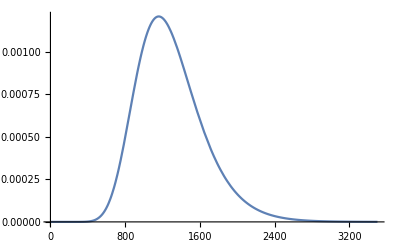

```mathematica
N1=1000;
s0=0.01;
h=0.5;
x0=1/(2 N1);


si[t_]:=s0;


taui[t_]:=taui[t]=h*NIntegrate[si[t1],{t1,0,t}];


pf1=2/(1+NIntegrate[Exp[-taui[t]],{t,0,Infinity}]);

C1=2 N1 pf1;


B[Te_]:=B[Te]=(2 N1)/NIntegrate[Exp[(1-h)/h taui[t]],{t,0,Te}];


pdfsd[Te_]:=pdfsd[Te]=(1/(2 N1)) C1 B[Te]^2 Exp[taui[Te]] 2 BesselK[0,2 Sqrt[B[Te] C1]];


pdfgenh[Te_]:=pdfgenh[Te]=h/(1-h) (C1 B[Te]^2)/(2 N1) Exp[(1-h)/h taui[Te]]*NIntegrate[q^(-(h/(1-h))) Exp[-B[Te] q] Exp[-C1 q^(-h/(1-h))],{q,0,Infinity},MaxRecursion->20];


a3=Plot[pdfgenh[t],{t,1,3500},PlotRange->All,PlotPoints->50]
```

```mathematica
timePoints=Range[1,3500,1];


weightValues=pdfgenh/@timePoints;

(*Combine time points and their corresponding weights into a single list*)
Datatfix=Transpose[{timePoints,weightValues}];
```

NIntegrate::nlim: t1 = t is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

```mathematica
Sum[Datatfix[[k,2]] k,{k,1,Length[Datatfix]}]
```

1290.32

```mathematica
Table[Datatfix[[i]]]
```

#### Datatfix

```mathematica
Datatfix={{1,4.2664932242037425*^-170},{2,8.854341584658055*^-120},{3,1.5589475782392584*^-97},{4,2.7288558908181865*^-84},{5,2.915461491608825*^-75},{6,1.332137216637624*^-68},{7,1.9847125989592127*^-63},{8,2.923504440917823*^-59},{9,8.268351378066367*^-56},{10,6.865227686626977*^-53},{11,2.2273897698551374*^-50},{12,3.4508993864334204*^-48},{13,2.9524595826262094*^-46},{14,1.5544114190320083*^-44},{15,5.469044542466939*^-43},{16,1.3711125929658334*^-41},{17,2.5767446238165255*^-40},{18,3.780730290657589*^-39},{19,4.476624277907723*^-38},{20,4.395519463195749*^-37},{21,3.6607648550084455*^-36},{22,2.635543498082266*^-35},{23,1.666751006555658*^-34},{24,9.386648284091457*^-34},{25,4.76305558551718*^-33},{26,2.1998757792900297*^-32},{27,9.329818717880907*^-32},{28,3.66144610469224*^-31},{29,1.3386616069133248*^-30},{30,4.586867770370054*^-30},{31,1.4807519134719656*^-29},{32,4.5249025946914814*^-29},{33,1.3143735557245935*^-28},{34,3.642869406183842*^-28},{35,9.666104376420475*^-28},{36,2.4630112276432637*^-27},{37,6.043464806688696*^-27},{38,1.4315177919120955*^-26},{39,3.2808533970933994*^-26},{40,7.290499074497083*^-26},{41,1.573734951638941*^-25},{42,3.3057059360976494*^-25},{43,6.767802720392431*^-25},{44,1.3524433373825614*^-24},{45,2.641590885760974*^-24},{46,5.049278463435539*^-24},{47,9.456097115518002*^-24},{48,1.7369131484605687*^-23},{49,3.132270010220099*^-23},{50,5.550807207653972*^-23},{51,9.674805046031883*^-23},{52,1.659836920769908*^-22},{53,2.8051146337391905*^-22},{54,4.67306153042178*^-22},{55,7.67895883392691*^-22},{56,1.2454305960146952*^-21},{57,1.9948168296375955*^-21},{58,3.157094668064462*^-21},{59,4.939625910713999*^-21},{60,7.644168119157899*^-21},{61,1.1705553921784614*^-20},{62,1.7744510532580253*^-20},{63,2.6639178267612137*^-20},{64,3.962116274402845*^-20},{65,5.840353442251719*^-20},{66,8.535013019875647*^-20},{67,1.2369788268692773*^-19},{68,1.7784678123639452*^-19},{69,2.537355427611486*^-19},{70,3.593252399267904*^-19},{71,5.052181114381464*^-19},{72,7.054446899320621*^-19},{73,9.784593676244302*^-19},{74,1.34839273419138*^-18},{75,1.8466186376236193*^-18},{76,2.513705126663752*^-18},{77,3.401831440931209*^-18},{78,4.577768249273207*^-18},{79,6.126535645708922*^-18},{80,8.15587326401917*^-18},{81,1.080167955683479*^-17},{82,1.4234603115768758*^-17},{83,1.866799822173696*^-17},{84,2.4367489968931176*^-17},{85,3.1662431686150895*^-17},{86,4.0959579394407574*^-17},{87,5.2759355124118215*^-17},{88,6.767512352862193*^-17},{89,8.645596485865459*^-17},{90,1.1001349251620811*^-16},{91,1.394533356231232*^-16},{92,1.7611198688286327*^-16},{93,2.215998040719757*^-16},{94,2.7785105038469815*^-16},{95,3.471819652093761*^-16},{96,4.323579734021171*^-16},{97,5.366712684294202*^-16},{98,6.640301435879468*^-16},{99,8.190615966100168*^-16},{100,1.0072288970826137*^-15},{101,1.234965984021953*^-15},{102,1.5098307534502875*^-15},{103,1.840679503731251*^-15},{104,2.2378650305654404*^-15},{105,2.713461104776863*^-15},{106,3.2815163252003533*^-15},{107,3.958340616969935*^-15},{108,4.762827943221777*^-15},{109,5.7168191165334066*^-15},{110,6.845508936246543*^-15},{111,8.177902240064646*^-15},{112,9.747323843920514*^-15},{113,1.1591987753938568*^-14},{114,1.3755631469377665*^-14},{115,1.6288221656567254*^-14},{116,1.9246737962026095*^-14},{117,2.2696042249055356*^-14},{118,2.6709841087055257*^-14},{119,3.137174989751504*^-14},{120,3.6776467765965133*^-14},{121,4.3031072566030024*^-14},{122,5.02564467109588*^-14},{123,5.858884455038039*^-14},{124,6.818161316675781*^-14},{125,7.920707909697099*^-14},{126,9.185861431194061*^-14},{127,1.0635289563002114*^-13},{128,1.2293237263146366*^-13},{129,1.4186795998917733*^-13},{130,1.6346197128957423*^-13},{131,1.880513120904892*^-13},{132,2.1601095130962648*^-13},{133,2.4775769093352143*^-13},{134,2.837542552116352*^-13},{135,3.2451372165099604*^-13},{136,3.706043173263223*^-13},{137,4.226546052638307*^-13},{138,4.813590869409854*^-13},{139,5.474842482735528*^-13},{140,6.218750778314817*^-13},{141,7.054620874402967*^-13},{142,7.992688667828046*^-13},{143,9.044202051177236*^-13},{144,1.0221508147778895*^-12},{145,1.1538146926999928*^-12},{146,1.3008951578715033*^-12},{147,1.465015604257344*^-12},{148,1.6479510104898235*^-12},{149,1.851640249369141*^-12},{150,2.078199242029344*^-12},{151,2.3299350034742373*^-12},{152,2.6093606280805253*^-12},{153,2.919211265600258*^-12},{154,3.2624611401684464*^-12},{155,3.642341666842687*^-12},{156,4.062360722254514*^-12},{157,4.526323128052647*^-12},{158,5.038352407950089*^-12},{159,5.6029138813661555*^-12},{160,6.224839158861012*^-12},{161,6.909352106810446*^-12},{162,7.662096351050593*^-12},{163,8.489164391539754*^-12},{164,9.397128402434882*^-12},{165,1.0393072794362962*^-11},{166,1.148462861808041*^-11},{167,1.2680009891156907*^-11},{168,1.3988051931791538*^-11},{169,1.5418251786365778*^-11},{170,1.698081083986276*^-11},{171,1.868667970082844*^-11},{172,2.0547605455119526*^-11},{173,2.257618138527543*^-11},{174,2.4785899254955182*^-11},{175,2.7191204260514542*^-11},{176,2.980755275443342*^-11},{177,3.265147284796312*^-11},{178,3.57406278101009*^-11},{179,3.909388372609902*^-11},{180,4.273137747942519*^-11},{181,4.667459192773119*^-11},{182,5.094643164114562*^-11},{183,5.557130337785194*^-11},{184,6.057520007263307*^-11},{185,6.598578866018164*^-11},{186,7.183250186473128*^-11},{187,7.814663409024979*^-11},{188,8.496144154810476*^-11},{189,9.231224676177332*^-11},{190,1.0023654759081067*^-10},{191,1.0877413091895927*^-10},{192,1.1796719115366836*^-10},{193,1.278604536875291*^-10},{194,1.3850130347362805*^-10},{195,1.4993991887043202*^-10},{196,1.6222941091367636*^-10},{197,1.754259681753886*^-10},{198,1.895890073727636*^-10},{199,2.0478132989169664*^-10},{200,2.210692843924783*^-10},{201,2.3852293566728305*^-10},{202,2.572162399214411*^-10},{203,2.7722722665269185*^-10},{204,2.9863818730483155*^-10},{205,3.215358708742711*^-10},{206,3.4601168665013416*^-10},{207,3.7216191427051194*^-10},{208,4.0008792127949884*^-10},{209,4.2989638836835324*^-10},{210,4.616995425078915*^-10},{211,4.956153981154075*^-10},{212,5.317680065102125*^-10},{213,5.702877138046139*^-10},{214,6.113114274438729*^-10},{215,6.549828915885715*^-10},{216,7.014529715371457*^-10},{217,7.508799473878279*^-10},{218,8.034298171402798*^-10},{219,8.592766094385115*^-10},{220,9.186027061576017*^-10},{221,9.815991750377043*^-10},{222,1.0484661125698045*^-9},{223,1.1194129973382584*^-9},{224,1.19465905402913*^-9},{225,1.2744336282886404*^-9},{226,1.3589765727041887*^-9},{227,1.448538644009416*^-9},{228,1.54338191181145*^-9},{229,1.6437801790237315*^-9},{230,1.7500194141905416*^-9},{231,1.8623981959155545*^-9},{232,1.9812281696313133*^-9},{233,2.1068345168838838*^-9},{234,2.239556437353618*^-9},{235,2.379747643815603*^-9},{236,2.527776870244838*^-9},{237,2.6840283932708475*^-9},{238,2.8489025671865946*^-9},{239,3.022816372704215*^-9},{240,3.2062039796843598*^-9},{241,3.399517324004379*^-9},{242,3.6032266987901466*^-9},{243,3.817821360196744*^-9},{244,4.043810147940727*^-9},{245,4.2817221207624325*^-9},{246,4.532107207029853*^-9},{247,4.795536870657452*^-9},{248,5.0726047925335865*^-9},{249,5.363927567639397*^-9},{250,5.670145418041105*^-9},{251,5.991922921936316*^-9},{252,6.329949758927385*^-9},{253,6.684941471699098*^-9},{254,7.057640244268465*^-9},{255,7.448815696974456*^-9},{256,7.859265698372661*^-9},{257,8.289817194186555*^-9},{258,8.741327053492182*^-9},{259,9.214682932262155*^-9},{260,9.71080415443722*^-9},{261,1.023064261066199*^-8},{262,1.0775183674826579*^-8},{263,1.1345447138549571*^-8},{264,1.1942488163733992*^-8},{265,1.2567398253322792*^-8},{266,1.322130624037511*^-8},{267,1.3905379295581067*^-8},{268,1.462082395332559*^-8},{269,1.5368887156409005*^-8},{270,1.615085731952422*^-8},{271,1.6968065411587107*^-8},{272,1.7821886057009198*^-8},{273,1.8713738656017698*^-8},{274,1.9645088523979587*^-8},{275,2.06174480501023*^-8},{276,2.163237787515761*^-8},{277,2.2691488088717795*^-8},{278,2.379643944550528*^-8},{279,2.4948944601366925*^-8},{280,2.6150769368580054*^-8},{281,2.7403733990656823*^-8},{282,2.8709714436649136*^-8},{283,3.00706437149758*^-8},{284,3.1488513206781956*^-8},{285,3.2965374018835867*^-8},{286,3.4503338355961556*^-8},{287,3.610458091299513*^-8},{288,3.7771340286248885*^-8},{289,3.9505920404455755*^-8},{290,4.131069197916306*^-8},{291,4.318809397453194*^-8},{292,4.514063509649429*^-8},{293,4.7170895301210364*^-8},{294,4.928152732276018*^-8},{295,5.1475258219995194*^-8},{296,5.3754890942468797*^-8},{297,5.6123305915353394*^-8},{298,5.8583462643246605*^-8},{299,6.113840133275613*^-8},{300,6.379124453374928*^-8},{301,6.654519879913994*^-8},{302,6.940355636308006*^-8},{303,7.23696968374105*^-8},{304,7.544708892622244*^-8},{305,7.86392921583636*^-8},{306,8.194995863772423*^-8},{307,8.538283481111956*^-8},{308,8.894176325358184*^-8},{309,9.263068447086491*^-8},{310,9.645363871895167*^-8},{311,1.0041476784035271*^-7},{312,1.0451831711696467*^-7},{313,1.0876863713925944*^-7},{314,1.1317018569155553*^-7},{315,1.1772752965311895*^-7},{316,1.2244534691483255*^-7},{317,1.273284283111582*^-7},{318,1.3238167956711177*^-7},{319,1.376101232599598*^-7},{320,1.430189007953335*^-7},{321,1.4861327439745793*^-7},{322,1.5439862911316417*^-7},{323,1.6038047482380096*^-7},{324,1.6656444829757945*^-7},{325,1.7295631520113108*^-7},{326,1.7956197217597303*^-7},{327,1.8638744890131262*^-7},{328,1.9343891017356368*^-7},{329,2.0072265799714944*^-7},{330,2.0824513368623325*^-7},{331,2.160129199768176*^-7},{332,2.2403274314912515*^-7},{333,2.3231147515946872*^-7},{334,2.4085613578132305*^-7},{335,2.4967389475561245*^-7},{336,2.587720739484923*^-7},{337,2.6815814951781866*^-7},{338,2.778397540866477*^-7},{339,2.878246789237435*^-7},{340,2.9812087613054443*^-7},{341,3.0873646083409173*^-7},{342,3.1967971338542464*^-7},{343,3.3095908156292015*^-7},{344,3.4258318278008515*^-7},{345,3.5456080629724623*^-7},{346,3.669009154366272*^-7},{347,3.796126498002631*^-7},{348,3.927053274901992*^-7},{349,4.061884473304335*^-7},{350,4.2007169107682856*^-7},{351,4.34364925706749*^-7},{352,4.490782055109147*^-7},{353,4.642217744484259*^-7},{354,4.798060683028168*^-7},{355,4.958417169154805*^-7},{356,5.123395464035375*^-7},{357,5.293105813747206*^-7},{358,5.467660471386692*^-7},{359,5.64717371913989*^-7},{360,5.831761890304644*^-7},{361,6.021543391257692*^-7},{362,6.216638723360465*^-7},{363,6.41717050479691*^-7},{364,6.623263492336971*^-7},{365,6.835044603019051*^-7},{366,7.05264293574471*^-7},{367,7.276189792779084*^-7},{368,7.505818701150146*^-7},{369,7.741665433940019*^-7},{370,7.983868031461597*^-7},{371,8.232566822313428*^-7},{372,8.487904444306187*^-7},{373,8.750025865253507*^-7},{374,9.019078403620435*^-7},{375,9.295211749022185*^-7},{376,9.578577982566518*^-7},{377,9.869331597032245*^-7},{378,1.0167629516877193*^-6},{379,1.0473631118067905*^-6},{380,1.078749825163417*^-6},{381,1.1109395248040685*^-6},{382,1.1439488958241004*^-6},{383,1.1777948753096165*^-6},{384,1.2124946567489911*^-6},{385,1.248065688612112*^-6},{386,1.2845256785983228*^-6},{387,1.3218925944421436*^-6},{388,1.3601846660408484*^-6},{389,1.3994203871354277*^-6},{390,1.439618517050233*^-6},{391,1.480798082406132*^-6},{392,1.5229783788064662*^-6},{393,1.566178972495078*^-6},{394,1.6104197019856629*^-6},{395,1.6557206796617718*^-6},{396,1.7021022933466761*^-6},{397,1.749585207842436*^-6},{398,1.7981903664373892*^-6},{399,1.8479389924554675*^-6},{400,1.8988525904015278*^-6},{401,1.9509529477428476*^-6},{402,2.0042621362798655*^-6},{403,2.0588025131165303*^-6},{404,2.1145967222599457*^-6},{405,2.1716676958833636*^-6},{406,2.230038655203881*^-6},{407,2.2897331123759523*^-6},{408,2.350774870944378*^-6},{409,2.4131880273071493*^-6},{410,2.476996971719654*^-6},{411,2.542226389327819*^-6},{412,2.6089012611600294*^-6},{413,2.677046865077002*^-6},{414,2.7466887766791276*^-6},{415,2.817852870170435*^-6},{416,2.8905653191787477*^-6},{417,2.964852597531174*^-6},{418,3.040741479984495*^-6},{419,3.1182590429096233*^-6},{420,3.1974326649297355*^-6},{421,3.278290027511257*^-6},{422,3.3608591155072397*^-6},{423,3.4451682176524325*^-6},{424,3.5312459270095626*^-6},{425,3.6191211413661238*^-6},{426,3.708823063581189*^-6},{427,3.8003812018816664*^-6},{428,3.8938253701073735*^-6},{429,3.989185687904511*^-6},{430,4.086492580866857*^-6},{431,4.1857767806242276*^-6},{432,4.2870693248777295*^-6},{433,4.390401557381163*^-6},{434,4.495805127868211*^-6},{435,4.603311991924813*^-6},{436,4.712954410806346*^-6},{437,4.82476495119905*^-6},{438,4.938776484925334*^-6},{439,5.0550221885923855*^-6},{440,5.173535543183823*^-6},{441,5.294350333593758*^-6},{442,5.417500648103085*^-6},{443,5.5430208777973675*^-6},{444,5.670945715926066*^-6},{445,5.801310157202766*^-6},{446,5.934149497045889*^-6},{447,6.069499330759645*^-6},{448,6.207395552654853*^-6},{449,6.347874355109331*^-6},{450,6.49097222756747*^-6},{451,6.636725955478756*^-6},{452,6.785172619174889*^-6},{453,6.936349592685284*^-6},{454,7.090294542490648*^-6},{455,7.247045426214393*^-6},{456,7.4066404912516314*^-6},{457,7.569118273335563*^-6},{458,7.73451759504099*^-6},{459,7.902877564224859*^-6},{460,8.07423757240349*^-6},{461,8.248637293066516*^-6},{462,8.426116679927195*^-6},{463,8.606715965109118*^-6},{464,8.790475657269022*^-6},{465,8.977436539655726*^-6},{466,9.167639668105084*^-6},{467,9.361126368970747*^-6},{468,9.557938236990778*^-6},{469,9.758117133090144*^-6},{470,9.961705182118804*^-6},{471,0.000010168744770525552},{472,0.00001037927854396761},{473,0.000010593349404855882},{474,0.000010811000509835938},{475,0.00001103227526720477},{476,0.000011257217334263392},{477,0.000011485870614605225},{478,0.000011718279255340593},{479,0.000011954487644257115},{480,0.000012194540406916377},{481,0.000012438482403686869},{482,0.000012686358726713285},{483,0.000012938214696822587},{484,0.000013194095860366527},{485,0.00001345404798600162},{486,0.000013718117061405765},{487,0.00001398634928993243},{488,0.000014258791087202496},{489,0.000014535489077633883},{490,0.000014816490090909343},{491,0.00001510184115838252},{492,0.00001539158950942291},{493,0.000015685782567699546},{494,0.000015984467947404263},{495,0.000016287693449414402},{496,0.000016595507057395582},{497,0.000016907956933844982},{498,0.000017225091416075114},{499,0.000017546959012138973},{500,0.0000178736083966967},{501,0.00001820508840682639},{502,0.000018541448037766075},{503,0.00001888273643860542},{504,0.000019229002907976884},{505,0.000019580296889545225},{506,0.000019936667967595227},{507,0.000020298165862486385},{508,0.000020664840426068725},{509,0.000021036741637044247},{510,0.00002141391959627503},{511,0.000021796424522038185},{512,0.00002218430674524583},{513,0.000022577616704527032},{514,0.000022976404941430615},{515,0.000023380722095405737},{516,0.000023790618898817806},{517,0.00002420614617189877},{518,0.00002462735481764804},{519,0.00002505429581668577},{520,0.00002548702022205882},{521,0.000025925579154000192},{522,0.000026370023794642353},{523,0.00002682040538268575},{524,0.0000272767752080224},{525,0.00002773918460631634},{526,0.00002820768495354068},{527,0.000028682327660472818},{528,0.000029163164167147973},{529,0.000029650245937272283},{530,0.0000301436244525961},{531,0.000030643351207248204},{532,0.00003114947770203173},{533,0.00003166205543868313},{534,0.00003218113591409402},{535,0.000032706770614497956},{536,0.000033239011009621964},{537,0.00003377790854680428},{538,0.000034323514645696816},{539,0.00003487588069005337},{540,0.000035435058024858215},{541,0.000036001097948424256},{542,0.00003657405170678603},{543,0.000037153970487632295},{544,0.000037740905414211366},{545,0.00003833490753920937},{546,0.00003893602783860293},{547,0.000039544317205487306},{548,0.000040159826443880114},{549,0.00004078260626250249},{550,0.000041412707268538674},{551,0.000042050179961373886},{552,0.000042695074726313106},{553,0.00004334744182828014},{554,0.000044007331405499296},{555,0.00004467479346315965},{556,0.00004534987786706386},{557,0.00004603263433726133},{558,0.00004672311244166827},{559,0.000047421361589674115},{560,0.000048127431025736494},{561,0.000048841369822965304},{562,0.00004956322687669655},{563,0.00005029305089805803},{564,0.00005103089040752679},{565,0.00005177679372848004},{566,0.00005253080898074046},{567,0.00005329298407411673},{568,0.00005406336670194063},{569,0.00005484200433460155},{570,0.000055628944213082094},{571,0.00005642423334248153},{572,0.000057227918485562244},{573,0.00005804004615627663},{574,0.00005886066261330687},{575,0.000059689813853606216},{576,0.00006052754560594621},{577,0.0000613739033244689},{578,0.00006222892966567669},{579,0.00006309267380452391},{580,0.00006396518256392055},{581,0.00006484649297076798},{582,0.00006573665226995735},{583,0.00006663570413292525},{584,0.00006754369191160322},{585,0.00006846065863205552},{586,0.00006938664698813358},{587,0.00007032169933514633},{588,0.000071265857683548},{589,0.00007221916369264547},{590,0.00007318165866432411},{591,0.00007415338353679521},{592,0.00007513437887836491},{593,0.0000761246848812259},{594,0.00007712434135527285},{595,0.00007813338772194315},{596,0.00007915186300808275},{597,0.00008017980583983977},{598,0.00008121725443658553},{599,0.00008226424660486448},{600,0.00008332081983726609},{601,0.00008438701089176787},{602,0.00008546285640010444},{603,0.00008654839233901799},{604,0.00008764365459455188},{605,0.00008874867825662351},{606,0.00008986349807728785},{607,0.0000909881483432843},{608,0.00009212266287996104},{609,0.0000932670750399256},{610,0.0000944214176986012},{611,0.00009558572324860117},{612,0.00009676002359414365},{613,0.00009794435014551016},{614,0.00009913873381354607},{615,0.00010034320500420643},{616,0.00010155779361314656},{617,0.00010278252902035861},{618,0.00010401744008485517},{619,0.00010526255513940082},{620,0.00010651790198529189},{621,0.00010778350788718657},{622,0.00010905939956798411},{623,0.0001103456032037566},{624,0.00011164214441873218},{625,0.00011294904828033082},{626,0.00011426633929425401},{627,0.00011559404139962954},{628,0.00011693217796420987},{629,0.00011828077177962868},{630,0.00011963984505671251},{631,0.00012100941942085065},{632,0.00012238951590742335},{633,0.00012378015495728887},{634,0.00012518135641233037},{635,0.0001265931395110635},{636,0.00012801552288430423},{637,0.00012944852455090035},{638,0.00013089216191352362},{639,0.00013234645175452583},{640,0.00013381141023185972},{641,0.0001352870528750627},{642,0.00013677339458130697},{643,0.00013827044961151484},{644,0.00013977823158654073},{645,0.00014129675348342006},{646,0.00014282602763168582},{647,0.00014436606570975263},{648,0.00014591687874137077},{649,0.00014747847709214838},{650,0.00014905087046614363},{651,0.00015063406790252767},{652,0.0001522280777723182},{653,0.00015383290777518395},{654,0.00015544856493632185},{655,0.00015707505560340552},{656,0.00015871238544360697},{657,0.00016036055948285944},{658,0.00016201958194746557},{659,0.00016368945647594885},{660,0.0001653701859851609},{661,0.0001670617726976607},{662,0.00016876421813918135},{663,0.00017047752300147106},{664,0.00017220168766016246},{665,0.00017393671141910028},{666,0.00017568259299294387},{667,0.00017743933038800975},{668,0.00017920692090019739},{669,0.00018098536111299326},{670,0.00018277464689555177},{671,0.00018457477340085403},{672,0.00018638573506394652},{673,0.00018820752560025635},{674,0.00019004013800398724},{675,0.00019188356454659264},{676,0.0001937377967753288},{677,0.00019560282551188868},{678,0.00019747864085111275},{679,0.00019936523215978075},{680,0.00020126258807548472},{681,0.00020317069650557906},{682,0.00020508954462621328},{683,0.0002070191188814434},{684,0.00020895940498242402},{685,0.00021091038790668138},{686,0.00021287205189746562},{687,0.0002148443804631847},{688,0.00021682735637691835},{689,0.00021882096167601174},{690,0.00022082517766175118},{691,0.00022283998489911895},{692,0.00022486536321663},{693,0.00022690129170624775},{694,0.00022894774872338116},{695,0.0002310047118869619},{696,0.0002330721580796024},{697,0.00023515006344783306},{698,0.00023723840340242013},{699,0.0002393371526187644},{700,0.00024144628503737817},{701,0.0002435657738644436},{702,0.00024569559157244965},{703,0.000247835709900909},{704,0.00024998609985715363},{705,0.0002521467317172115},{706,0.0002543175750267586},{707,0.0002564985986021538},{708,0.00025868977053155733},{709,0.000260891058176087},{710,0.0002631024281711382},{711,0.0002653238464276926},{712,0.0002675552781337526},{713,0.0002697966877558407},{714,0.0002720480390405759},{715,0.00027430929501632943},{716,0.0002765804179949533},{717,0.00027886136957358857},{718,0.0002811521106365464},{719,0.0002834526013572654},{720,0.00028576280120034533},{721,0.0002880826689236538},{722,0.0002904121625805072},{723,0.00029275123952192736},{724,0.0002950998563989689},{725,0.0002974579691651236},{726,0.00029982553307879306},{727,0.00030220250270583644},{728,0.00030458883192219027},{729,0.00030698447391655774},{730,0.00030938938119317},{731,0.00031180350557461845},{732,0.0003142267982047562},{733,0.00031665920955166894},{734,0.00031910068941071613},{735,0.0003215511869076387},{736,0.0003240106487281677},{737,0.000326479027989116},{738,0.00032895626650599304},{739,0.00033144231253207985},{740,0.00033393711189402413},{741,0.00033644060976891876},{742,0.0003389527506878767},{743,0.00034147347853966846},{744,0.00034400273657442335},{745,0.00034654046740739545},{746,0.0003490866130227914},{747,0.00035164111477765746},{748,0.0003542039134058327},{749,0.00035677494902195875},{750,0.0003593541611255516},{751,0.00036194148860513195},{752,0.00036453686974241583},{753,0.0003671402422165618},{754,0.0003697515431084755},{755,0.0003723707089051731},{756,0.0003749976755041986},{757,0.0003776323782180987},{758,0.00038027475177895137},{759,0.00038292473034294816},{760,0.0003855822474950314},{761,0.00038824723625358477},{762,0.0003909196290751724},{763,0.0003935993578593346},{764,0.0003962863539534291},{765,0.00039898054815752724},{766,0.00040168187072935643},{767,0.0004043902513892913},{768,0.00040710561932539446},{769,0.00040982790319850284},{770,0.0004125570311473627},{771,0.0004152929307938065},{772,0.00041803552924797854},{773,0.00042078475311360403},{774,0.00042354052849330004},{775,0.0004263027809939301},{776,0.0004290714357320024},{777,0.00043184641733910696},{778,0.00043462764996739445},{779,0.0004374150572950952},{780,0.0004402085625320752},{781,0.0004430080884254337},{782,0.0004458135572651353},{783,0.0004486248908896797},{784,0.0004514419367464128},{785,0.00045426483762424526},{786,0.00045709329220547173},{787,0.0004599272945255373},{788,0.000462766764251899},{789,0.00046561162063529755},{790,0.00046846178251566255},{791,0.00047131716832804656},{792,0.0004741776961085942},{793,0.0004770432835005323},{794,0.00047991384776019635},{795,0.00048278930576307915},{796,0.0004856695740099072},{797,0.0004885545686327443},{798,0.000491444205401119},{799,0.0004943383997281761},{800,0.0004972370666768526},{801,0.0005001401209660749},{802,0.000503047476976981},{803,0.0005059590487591589},{804,0.00050887475003691},{805,0.0005117944942155301},{806,0.0005147181943876082},{807,0.0005176457633393454},{808,0.0005205771135568901},{809,0.0005235121572326893},{810,0.0005264508062718554},{811,0.0005293929722985492},{812,0.0005323385666623772},{813,0.0005352875004447976},{814,0.0005382396844655467},{815,0.0005411950292890707},{816,0.0005441534452309723},{817,0.0005471148423644648},{818,0.0005500791305268373},{819,0.0005530462193259298},{820,0.000556016018146613},{821,0.0005589884361572802},{822,0.0005619633823163384},{823,0.0005649407653787142},{824,0.000567920493902357},{825,0.0005709024762547525},{826,0.0005738866206194337},{827,0.0005768728350024996},{828,0.0005798610272391348},{829,0.0005828511050001268},{830,0.0005858429757983908},{831,0.0005888365469954892},{832,0.000591831725808149},{833,0.0005948284193147842},{834,0.0005978265344620093},{835,0.0006008259780711533},{836,0.0006038266568447687},{837,0.0006068284773731385},{838,0.0006098313461407718},{839,0.0006128351695329034},{840,0.0006158398538419781},{841,0.0006188453052741317},{842,0.0006218514299556658},{843,0.0006248581339395095},{844,0.0006278653232116762},{845,0.0006308729036977067},{846,0.0006338807812691082},{847,0.000636888861749773},{848,0.0006398970509223942},{849,0.0006429052545348618},{850,0.0006459133783066522},{851,0.0006489213279351978},{852,0.0006519290091022467},{853,0.0006549363274802071},{854,0.0006579431887384701},{855,0.0006609494985497271},{856,0.00066395516259626},{857,0.0006669600865762199},{858,0.0006699641762098865},{859,0.0006729673372459064},{860,0.0006759694754675179},{861,0.0006789704966987457},{862,0.0006819703068105911},{863,0.0006849688117271837},{864,0.0006879659174319244},{865,0.0006909615299735998},{866,0.0006939555554724773},{867,0.0006969479001263751},{868,0.0006999384702167071},{869,0.00070292717211451},{870,0.0007059139122864355},{871,0.0007088985973007265},{872,0.0007118811338331633},{873,0.0007148614286729831},{874,0.0007178393887287723},{875,0.0007208149210343351},{876,0.0007237879327545309},{877,0.0007267583311910807},{878,0.0007297260237883542},{879,0.000732690918139117},{880,0.0007356529219902546},{881,0.0007386119432484633},{882,0.0007415678899859123},{883,0.0007445206704458716},{884,0.0007474701930483142},{885,0.0007504163663954789},{886,0.0007533590992774052},{887,0.0007562983006774362},{888,0.0007592338797776842},{889,0.0007621657459644676},{890,0.0007650938088337068},{891,0.0007680179781962953},{892,0.000770938164083427},{893,0.0007738542767518891},{894,0.0007767662266893304},{895,0.0007796739246194765},{896,0.0007825772815073229},{897,0.0007854762085642832},{898,0.0007883706172533032},{899,0.000791260419293938},{900,0.0007941455266673903},{901,0.0007970258516215113},{902,0.00079990130667576},{903,0.0008027718046261313},{904,0.0008056372585500376},{905,0.000808497581811152},{906,0.0008113526880642188},{907,0.0008142024912598125},{908,0.00081704690564907},{909,0.0008198858457883672},{910,0.0008227192265439707},{911,0.0008255469630966363},{912,0.0008283689709461712},{913,0.0008311851659159541},{914,0.0008339954641574154},{915,0.0008367997821544707},{916,0.0008395980367279161},{917,0.0008423901450397799},{918,0.0008451760245976295},{919,0.0008479555932588401},{920,0.0008507287692348164},{921,0.0008534954710951706},{922,0.0008562556177718596},{923,0.0008590091285632778},{924,0.0008617559231383038},{925,0.0008644959215403032},{926,0.000867229044191095},{927,0.0008699552118948579},{928,0.00087267434584201},{929,0.0008753863676130296},{930,0.0008780911991822375},{931,0.000880788762921536},{932,0.0008834789816040963},{933,0.0008861617784080098},{934,0.0008888370769198814},{935,0.0008915048011383928},{936,0.0008941648754778074},{937,0.0008968172247714329},{938,0.0008994617742759891},{939,0.0009020984496712992},{940,0.0009047271770689778},{941,0.0009073478830122416},{942,0.0009099604944786714},{943,0.0009125649388885804},{944,0.000915161144100509},{945,0.0009177490384193291},{946,0.0009203285505980652},{947,0.0009228996098408983},{948,0.0009254621458061181},{949,0.0009280160886090385},{950,0.0009305613688248531},{951,0.0009330979174914625},{952,0.0009356256661122345},{953,0.0009381445466587356},{954,0.0009406544915734025},{955,0.0009431554337721767},{956,0.0009456473066470879},{957,0.0009481300440687894},{958,0.0009506035803890515},{959,0.000953067850443207},{960,0.0009555227895525471},{961,0.0009579683335266753},{962,0.0009604044186658095},{963,0.0009628309817630453},{964,0.0009652479601065659},{965,0.0009676552914818103},{966,0.0009700529141735906},{967,0.0009724407669681686},{968,0.0009748187891552858},{969,0.0009771869205301407},{970,0.0009795451013953273},{971,0.0009818932725627267},{972,0.0009842313753553498},{973,0.000986559351609134},{974,0.0009888771436747021},{975,0.0009911846944190646},{976,0.000993481947227285},{977,0.0009957688460040966},{978,0.0009980453351754717},{979,0.0010003113596901527},{980,0.0010025668650211288},{981,0.0010048117971636578},{982,0.0010070461026502077},{983,0.0010092697285316906},{984,0.0010114826223920203},{985,0.0010136847323460984},{986,0.0010158760070410305},{987,0.0010180563956572952},{988,0.0010202258479098754},{989,0.0010223843140493313},{990,0.0010245317448628543},{991,0.0010266680916752506},{992,0.0010287923496643762},{993,0.0010309073412896716},{994,0.0010330101494377736},{995,0.0010351016842785957},{996,0.0010371818998409367},{997,0.0010392507506886194},{998,0.0010413081919368055},{999,0.001043354179241978},{1000,0.0010453886688052798},{1001,0.001047411617373084},{1002,0.0010494229822375302},{1003,0.0010514227212370109},{1004,0.001053410792756619},{1005,0.0010553871557285545},{1006,0.0010573517696324925},{1007,0.0010593045944959118},{1008,0.0010612455908943779},{1009,0.0010631747199517884},{1010,0.0010650919433405836},{1011,0.0010669972232819098},{1012,0.0010688905225457491},{1013,0.0010707718044510074},{1014,0.0010726410328655617},{1015,0.0010744981722062767},{1016,0.001076343187438973},{1017,0.0010781760440783637},{1018,0.0010799967081879505},{1019,0.001081805146379884},{1020,0.001083601325814783},{1021,0.0010853852142015206},{1022,0.0010871567797969739},{1023,0.0010889159914057305},{1024,0.0010906628183797661},{1025,0.0010923972306180832},{1026,0.001094119198566311},{1027,0.0010958286932162748},{1028,0.0010975256861055242},{1029,0.0010992101493168358},{1030,0.001100882055477664},{1031,0.0011025413777595798},{1032,0.0011041880898776542},{1033,0.0011058221660954948},{1034,0.0011074435812013165},{1035,0.001109052310542891},{1036,0.0011106483300025516},{1037,0.0011122316160025927},{1038,0.0011138021455044595},{1039,0.0011153598960079109},{1040,0.001116904845550144},{1041,0.0011184369727048897},{1042,0.0011199562565814781},{1043,0.0011214626768238695},{1044,0.0011229562136096565},{1045,0.001124436847649037},{1046,0.0011259045601837467},{1047,0.0011273593329859796},{1048,0.0011288011483572605},{1049,0.0011302299891272985},{1050,0.001131645838652806},{1051,0.0011330486808162933},{1052,0.0011344385000248306},{1053,0.001135815281208779},{1054,0.001137179009820505},{1055,0.001138529671833051},{1056,0.0011398672537387914},{1057,0.0011411917425480534},{1058,0.0011425031257877142},{1059,0.0011438013914997732},{1060,0.0011450865282398904},{1061,0.001146358525075909},{1062,0.0011476173715863393},{1063,0.0011488630578588342},{1064,0.0011500955744886212},{1065,0.0011513149125769223},{1066,0.0011525210637293422},{1067,0.001153714020054235},{1068,0.0011548937741610516},{1069,0.001156060319158644},{1070,0.0011572136486535784},{1071,0.001158353756748393},{1072,0.001159480638039852},{1073,0.0011605942876171701},{1074,0.0011616947010602183},{1075,0.0011627818744377025},{1076,0.0011638558043053238},{1077,0.0011649164877039193},{1078,0.0011659639221575744},{1079,0.0011669981056717231},{1080,0.0011680190367312237},{1081,0.001169026714296855},{1082,0.0011700211378078238},{1083,0.0011710023071756696},{1084,0.0011719702227833057},{1085,0.0011729248854831448},{1086,0.0011738662965950601},{1087,0.0011747944579043282},{1088,0.0011757093716595422},{1089,0.0011766110405705202},{1090,0.0011774994678061912},{1091,0.0011783746569924587},{1092,0.001179236612210055},{1093,0.001180085337992378},{1094,0.0011809208393232982},{1095,0.0011817431216349739},{1096,0.0011825521908056245},{1097,0.0011833480531573091},{1098,0.0011841307154536742},{1099,0.0011849001849263234},{1100,0.00118565646915858},{1101,0.001186399576253137},{1102,0.0011871295147172388},{1103,0.0011878462934882643},{1104,0.0011885499219313994},{1105,0.001189240409837294},{1106,0.0011899177674196979},{1107,0.0011905820053130917},{1108,0.0011912331345702992},{1109,0.0011918711666600967},{1110,0.0011924961134647941},{1111,0.0011931079872778238},{1112,0.0011937068008012984},{1113,0.0011942925671435776},{1114,0.0011948652998168031},{1115,0.0011954250127344395},{1116,0.0011959717202087957},{1117,0.001196505436948537},{1118,0.001197026178056191},{1119,0.001197533959025641},{1120,0.00119802879573961},{1121,0.0011985107044671368},{1122,0.0011989797018610389},{1123,0.0011994358049553751},{1124,0.0011998790311628915},{1125,0.0012003093982724624},{1126,0.0012007269244465229},{1127,0.0012011316282184961},{1128,0.0012015235284902096},{1129,0.0012019026445293094},{1130,0.0012022689959666564},{1131,0.001202622602793732},{1132,0.0012029634853600241},{1133,0.0012032916643704072},{1134,0.0012036071608825325},{1135,0.001203909996304191},{1136,0.0012042001923906831},{1137,0.0012044777712421832},{1138,0.0012047427553010918},{1139,0.0012049951673493923},{1140,0.001205235030505997},{1141,0.0012054623682240906},{1142,0.0012056772042884658},{1143,0.0012058795628128649},{1144,0.0012060694682373063},{1145,0.0012062469453254184},{1146,0.0012064120191617575},{1147,0.0012065647151491333},{1148,0.0012067050590059336},{1149,0.0012068330767634281},{1150,0.0012069487947630952},{1151,0.0012070522396539305},{1152,0.0012071434383897535},{1153,0.0012072224182265224},{1154,0.0012072892067196347},{1155,0.001207343831721242},{1156,0.0012073863213775445},{1157,0.0012074167041261046},{1158,0.0012074350086931417},{1159,0.0012074412640908428},{1160,0.0012074354996146628},{1161,0.0012074177448447348},{1162,0.0012073880296215025},{1163,0.0012073463840832478},{1164,0.0012072928386315483},{1165,0.001207227423937767},{1166,0.0012071501709403575},{1167,0.0012070611108421709},{1168,0.0012069602751077586},{1169,0.0012068476954606889},{1170,0.001206723403880849},{1171,0.0012065874326017646},{1172,0.0012064398141634243},{1173,0.001206280581192482},{1174,0.0012061097667176136},{1175,0.0012059274039600174},{1176,0.0012057335263811267},{1177,0.0012055281676799318},{1178,0.0012053113617903146},{1179,0.0012050831428783782},{1180,0.001204843545339785},{1181,0.0012045926037970978},{1182,0.0012043303530971218},{1183,0.001204056828308259},{1184,0.0012037720647178512},{1185,0.001203476097829543},{1186,0.0012031689633606377},{1187,0.001202850697239466},{1188,0.0012025213356027533},{1189,0.0012021809147929974},{1190,0.0012018294713558402},{1191,0.0012014670420374622},{1192,0.001201093663781965},{1193,0.0012007093737287703},{1194,0.0012003142092100174},{1195,0.0011999082077479727},{1196,0.0011994914070524382},{1197,0.0011990638450181709},{1198,0.001198625559722309},{1199,0.0011981765894218007},{1200,0.0011977169725508384},{1201,0.0011972467477176182},{1202,0.0011967659537045331},{1203,0.0011962746294615172},{1204,0.001195772814106244},{1205,0.001195260546920522},{1206,0.0011947378673494117},{1207,0.0011942048149971025},{1208,0.001193661429622315},{1209,0.0011931077511412233},{1210,0.0011925438196209778},{1211,0.00119196967527823},{1212,0.0011913853584766567},{1213,0.0011907909097244867},{1214,0.0011901863696720456},{1215,0.0011895717791092935},{1216,0.0011889471789633846},{1217,0.0011883126102962302},{1218,0.001187668114302068},{1219,0.00118701373230504},{1220,0.0011863495057567862},{1221,0.001185675476234036},{1222,0.0011849916854362152},{1223,0.0011842981751830637},{1224,0.0011835949874122568},{1225,0.0011828821641770375},{1226,0.0011821597476438597},{1227,0.0011814277800900389},{1228,0.0011806863039014136},{1229,0.0011799353615700103},{1230,0.0011791749956917294},{1231,0.0011784052489640336},{1232,0.001177626164183643},{1233,0.001176837784244246},{1234,0.0011760401521342168},{1235,0.0011752333109343433},{1236,0.0011744173038155676},{1237,0.001173592174036734},{1238,0.00117275796494234},{1239,0.001171914719960318},{1240,0.001171062482599804},{1241,0.0011702012964489295},{1242,0.0011693312051726243},{1243,0.001168452252573911},{1244,0.001167564482325583},{1245,0.0011666679383850014},{1246,0.0011657626647025414},{1247,0.0011648487052945346},{1248,0.00116392610424113},{1249,0.00116299490568417},{1250,0.0011620551538560667},{1251,0.0011611068929683619},{1252,0.0011601501673517607},{1253,0.0011591850213737587},{1254,0.0011582114994530734},{1255,0.0011572296460575914},{1256,0.0011562395057023122},{1257,0.0011552411229473162},{1258,0.0011542345423957367},{1259,0.0011532198086917447},{1260,0.0011521969665185465},{1261,0.001151166060596389},{1262,0.0011501271356805821},{1263,0.001149080236559531},{1264,0.0011480254080527726},{1265,0.0011469626950090332},{1266,0.0011458921423042952},{1267,0.0011448137948398723},{1268,0.001143727697540496},{1269,0.0011426338953524234},{1270,0.001141532433241536},{1271,0.00114042335619148},{1272,0.0011393067092017898},{1273,0.0011381825372860392},{1274,0.0011370508854699997},{1275,0.0011359117987898143},{1276,0.0011347653222901774},{1277,0.0011336115010225285},{1278,0.0011324503800432633},{1279,0.0011312820044119458},{1280,0.0011301064191895462},{1281,0.0011289236694366777},{1282,0.0011277338002118513},{1283,0.0011265368565697457},{1284,0.0011253328835594807},{1285,0.0011241219262229133},{1286,0.0011229040295929315},{1287,0.001121679238691778},{1288,0.0011204475985293707},{1289,0.0011192091541016441},{1290,0.0011179639503888959},{1291,0.0011167120323541545},{1292,0.0011154534449415512},{1293,0.0011141882330747014},{1294,0.0011129164416551181},{1295,0.001111638115560605},{1296,0.0011103532996436913},{1297,0.0011090620387300635},{1298,0.001107764377617009},{1299,0.001106460361071882},{1300,0.001105150033830567},{1301,0.00110383344059597},{1302,0.001102510626036506},{1303,0.0011011816347846115},{1304,0.001099846511435262},{1305,0.0010985053005445056},{1306,0.0010971580466280068},{1307,0.001095804794159593},{1308,0.0010944455875698386},{1309,0.0010930804712446294},{1310,0.0010917094895237609},{1311,0.0010903326866995445},{1312,0.0010889501070154186},{1313,0.0010875617946645769},{1314,0.00108616779378861},{1315,0.0010847681484761557},{1316,0.0010833629027615622},{1317,0.0010819521006235648},{1318,0.0010805357859839685},{1319,0.0010791140027063574},{1320,0.001077686794594795},{1321,0.0010762542053925528},{1322,0.0010748162787808423},{1323,0.0010733730583775654},{1324,0.0010719245877360679},{1325,0.001070470910343913},{1326,0.0010690120696216626},{1327,0.0010675481089216698},{1328,0.0010660790718162818},{1329,0.0010646050009180993},{1330,0.0010631259396764467},{1331,0.0010616419311590926},{1332,0.00106015301816382},{1333,0.0010586592440280762},{1334,0.0010571606513723457},{1335,0.0010556572829612898},{1336,0.0010541491814810182},{1337,0.0010526363895380138},{1338,0.0010511189496580466},{1339,0.0010495969042851048},{1340,0.0010480702957803446},{1341,0.001046539166421037},{1342,0.0010450035583995413},{1343,0.001043463513822278},{1344,0.0010419190747087217},{1345,0.0010403702829903981},{1346,0.0010388171805098961},{1347,0.00103725980901989},{1348,0.0010356982101821753},{1349,0.0010341324255667122},{1350,0.001032562496650675},{1351,0.0010309884648175306},{1352,0.0010294103713561075},{1353,0.001027828257459688},{1354,0.0010262421642251065},{1355,0.0010246521326518587},{1356,0.0010230582036412279},{1357,0.0010214604179954081},{1358,0.0010198588164166565},{1359,0.0010182534395064404},{1360,0.0010166443277646042},{1361,0.001015031521588543},{1362,0.0010134150612723892},{1363,0.0010117949870062089},{1364,0.0010101713388752048},{1365,0.0010085441568589363},{1366,0.0010069134808305463},{1367,0.001005279350555998},{1368,0.0010036418056933248},{1369,0.0010020008857918876},{1370,0.0010003566302916424},{1371,0.0009987090785224227},{1372,0.0009970582697032217},{1373,0.0009954042429415003},{1374,0.0009937470372324885},{1375,0.0009920866914585108},{1376,0.0009904232443883102},{1377,0.000988756734676394},{1378,0.0009870872008623758},{1379,0.000985414681370337},{1380,0.0009837392145082013},{1381,0.000982060838467103},{1382,0.0009803795913207827},{1383,0.0009786955110249848},{1384,0.000977008635416863},{1385,0.0009753190022143984},{1386,0.0009736266490158255},{1387,0.0009719316132990694},{1388,0.0009702339324211931},{1389,0.0009685336436178465},{1390,0.000966830784002741},{1391,0.000965125390567112},{1392,0.0009634175001792118},{1393,0.0009617071495837947},{1394,0.0009599943754016211},{1395,0.0009582792141289697},{1396,0.0009565617021371537},{1397,0.0009548418756720529},{1398,0.0009531197708536459},{1399,0.0009513954236755633},{1400,0.0009496688700046368},{1401,0.0009479401455804698},{1402,0.0009462092860150033},{1403,0.0009444763267921018},{1404,0.0009427413032671424},{1405,0.0009410042506666139},{1406,0.0009392652040877244},{1407,0.0009375241984980174},{1408,0.000935781268734994},{1409,0.0009340364495057489},{1410,0.0009322897753866105},{1411,0.0009305412808227873},{1412,0.0009287910001280338},{1413,0.0009270389674843056},{1414,0.0009252852169414421},{1415,0.0009235297824168446},{1416,0.0009217726976951662},{1417,0.0009200139972635896},{1418,0.0009182537129461655},{1419,0.0009164918789823518},{1420,0.000914728527867949},{1421,0.0009129636942638864},{1422,0.0009111974103666507},{1423,0.0009094297090236653},{1424,0.0009076606229474117},{1425,0.0009058901847151925},{1426,0.0009041184267688987},{1427,0.0009023453814147861},{1428,0.0009005710808232554},{1429,0.0008987955570286476},{1430,0.0008970188419290351},{1431,0.0008952409672860353},{1432,0.0008934619647246147},{1433,0.0008916818657329135},{1434,0.0008899007016620708},{1435,0.0008881185037260588},{1436,0.0008863353030015235},{1437,0.0008845511304276291},{1438,0.000882766016805919},{1439,0.0008809799928001735},{1440,0.0008791930889362784},{1441,0.0008774053356021012},{1442,0.0008756167630498086},{1443,0.0008738274013835746},{1444,0.0008720372805838382},{1445,0.0008702464304828427},{1446,0.0008684548807767226},{1447,0.0008666626610229879},{1448,0.0008648698006404409},{1449,0.0008630763289091056},{1450,0.0008612822749701626},{1451,0.0008594876678258867},{1452,0.0008576925363395962},{1453,0.0008558969092356016},{1454,0.0008541008150991737},{1455,0.0008523042823764948},{1456,0.0008505073393746429},{1457,0.0008487100142615598},{1458,0.0008469123350660383},{1459,0.0008451143296777093},{1460,0.0008433160258470372},{1461,0.0008415174511853207},{1462,0.0008397186331646956},{1463,0.0008379195991181526},{1464,0.0008361203762395492},{1465,0.0008343209915836363},{1466,0.0008325214720660846},{1467,0.0008307218444635214},{1468,0.0008289221354135669},{1469,0.0008271223714148793},{1470,0.0008253225788272089},{1471,0.0008235227838714512},{1472,0.0008217230126297058},{1473,0.0008199232910453451},{1474,0.0008181236449230843},{1475,0.0008163240999290608},{1476,0.00081452468159091},{1477,0.0008127254152978569},{1478,0.000810926326300803},{1479,0.0008091274397124255},{1480,0.0008073287805072792},{1481,0.000805530373521899},{1482,0.0008037322434549151},{1483,0.0008019344148671625},{1484,0.0008001369121818095},{1485,0.000798339759684473},{1486,0.0007965429815233563},{1487,0.0007947466017093775},{1488,0.0007929506441163108},{1489,0.0007911551324809286},{1490,0.0007893600904031496},{1491,0.0007875655413461891},{1492,0.0007857715086367157},{1493,0.0007839780154650121},{1494,0.0007821850848851392},{1495,0.0007803927398151049},{1496,0.0007786010030370362},{1497,0.0007768098971973594},{1498,0.0007750194448069774},{1499,0.0007732296682414578},{1500,0.0007714405897412189},{1501,0.0007696522314117231},{1502,0.000767864615223678},{1503,0.0007660777630132326},{1504,0.0007642916964821836},{1505,0.0007625064371981836},{1506,0.0007607220065949527},{1507,0.0007589384259724936},{1508,0.0007571557164973139},{1509,0.0007553738992026457},{1510,0.0007535929967856355},{1511,0.0007518130264220677},{1512,0.00075003400873969},{1513,0.0007482559678418975},{1514,0.0007464789222997093},{1515,0.0007447028923515876},{1516,0.0007429278981043784},{1517,0.0007411539595335607},{1518,0.0007393810964835},{1519,0.0007376093286677053},{1520,0.0007358386756690884},{1521,0.0007340691569402254},{1522,0.0007323007918036261},{1523,0.0007305335994562363},{1524,0.0007287675989534663},{1525,0.0007270028092327742},{1526,0.0007252392490991074},{1527,0.0007234769372287214},{1528,0.0007217158921694586},{1529,0.0007199561323410384},{1530,0.0007181976760353413},{1531,0.0007164405414167052},{1532,0.0007146847465222193},{1533,0.0007129303092620165},{1534,0.0007111772474195797},{1535,0.0007094255786404975},{1536,0.0007076753204785437},{1537,0.0007059264903279673},{1538,0.0007041791054686876},{1539,0.0007024331830555058},{1540,0.0007006887401184238},{1541,0.0006989457935629547},{1542,0.0006972043601704445},{1543,0.0006954644565983959},{1544,0.0006937260993807891},{1545,0.0006919893049284098},{1546,0.0006902540895291739},{1547,0.0006885204693484638},{1548,0.000686788460429455},{1549,0.0006850580786934519},{1550,0.0006833293399402266},{1551,0.0006816022598483563},{1552,0.0006798768539755621},{1553,0.0006781531377590542},{1554,0.0006764311265158731},{1555,0.0006747108354432413},{1556,0.0006729922796189038},{1557,0.0006712754740014843},{1558,0.0006695604334308333},{1559,0.0006678471726283828},{1560,0.0006661357061975032},{1561,0.0006644260486238562},{1562,0.0006627182142757588},{1563,0.0006610122174045361},{1564,0.0006593080721448908},{1565,0.0006576057925152594},{1566,0.0006559053924181838},{1567,0.0006542068856406735},{1568,0.000652510285854573},{1569,0.0006508156066169329},{1570,0.0006491228613703828},{1571,0.0006474320634434953},{1572,0.0006457432260511707},{1573,0.0006440563622950032},{1574,0.0006423714851636577},{1575,0.0006406886075332524},{1576,0.0006390077421677322},{1577,0.0006373289017192525},{1578,0.000635652098728556},{1579,0.0006339773456253589},{1580,0.0006323046547287306},{1581,0.00063063403824748},{1582,0.0006289655082805429},{1583,0.0006272990768173637},{1584,0.0006256347557382886},{1585,0.0006239725568149492},{1586,0.0006223124917106544},{1587,0.0006206545719807812},{1588,0.0006189988090731656},{1589,0.000617345214328495},{1590,0.0006156937989807003},{1591,0.000614044574157352},{1592,0.0006123975508800539},{1593,0.0006107527400648372},{1594,0.0006091101525225605},{1595,0.000607469798959304},{1596,0.0006058316899767692},{1597,0.0006041958360726748},{1598,0.0006025622476411602},{1599,0.0006009309349731801},{1600,0.000599301908256911},{1601,0.0005976751775781481},{1602,0.0005960507529207066},{1603,0.0005944286441668291},{1604,0.0005928088610975808},{1605,0.0005911914133932612},{1606,0.0005895763106338003},{1607,0.0005879635622991695},{1608,0.0005863531807405179},{1609,0.0005847451663268922},{1610,0.0005831395371530212},{1611,0.0005815362993323409},{1612,0.0005799354618510922},{1613,0.0005783370335979862},{1614,0.0005767410233646172},{1615,0.0005751474398458628},{1616,0.0005735562916402984},{1617,0.0005719675872506007},{1618,0.0005703813350839532},{1619,0.0005687975434524636},{1620,0.0005672162205735626},{1621,0.0005656373745704203},{1622,0.0005640610134723471},{1623,0.00056248714521521},{1624,0.0005609157776418382},{1625,0.0005593469185024309},{1626,0.0005577805754549716},{1627,0.0005562167560656299},{1628,0.0005546554678091802},{1629,0.0005530967180694006},{1630,0.0005515405141394931},{1631,0.0005499868632224834},{1632,0.0005484357724316371},{1633,0.000546887248790866},{1634,0.0005453412992351361},{1635,0.0005437979306108831},{1636,0.000542257149676412},{1637,0.0005407189631023146},{1638,0.0005391833774718722},{1639,0.000537650399281471},{1640,0.0005361200349410018},{1641,0.0005345922907742786},{1642,0.0005330671730194382},{1643,0.0005315446878293514},{1644,0.0005300248412720336},{1645,0.0005285076393310473},{1646,0.0005269930879059147},{1647,0.0005254811928125175},{1648,0.000523971959783513},{1649,0.0005224653944687327},{1650,0.0005209615024355915},{1651,0.0005194602891694953},{1652,0.000517961760074241},{1653,0.0005164659204724303},{1654,0.0005149727756058638},{1655,0.0005134823306359565},{1656,0.000511994590644132},{1657,0.0005105095606322295},{1658,0.0005090272455229133},{1659,0.000507547650160064},{1660,0.0005060707793091908},{1661,0.0005045966376578261},{1662,0.0005031252298159323},{1663,0.0005016565603162982},{1664,0.0005001906336149442},{1665,0.0004987274540915158},{1666,0.0004972670260496873},{1667,0.0004958093537175617},{1668,0.0004943544412480634},{1669,0.0004929022927193441},{1670,0.0004914529121351697},{1671,0.0004900063034253254},{1672,0.000488562470446007},{1673,0.0004871214169802192},{1674,0.0004856831467381662},{1675,0.0004842476633576485},{1676,0.00048281497040445805},{1677,0.0004813850713727661},{1678,0.0004799579696855212},{1679,0.00047853366869483335},{1680,0.00047711217168237277},{1681,0.00047569348185975394},{1682,0.00047427760236892644},{1683,0.00047286453628256716},{1684,0.0004714542866044613},{1685,0.00047004685626989755},{1686,0.0004686422481460468},{1687,0.00046724046503235437},{1688,0.0004658415096609209},{1689,0.0004644453846968854},{1690,0.00046305209273881704},{1691,0.0004616616363190846},{1692,0.000460274017904251},{1693,0.0004588892398954448},{1694,0.00045750730462874753},{1695,0.00045612821437556627},{1696,0.00045475197134301913},{1697,0.0004533785776743072},{1698,0.00045200803544909483},{1699,0.00045064034668388547},{1700,0.000449275513332394},{1701,0.0004479135372859247},{1702,0.00044655442037374113},{1703,0.00044519816436344424},{1704,0.0004438447709613357},{1705,0.00044249424181279704},{1706,0.00044114657850265367},{1707,0.0004398017825555449},{1708,0.00043845985543629795},{1709,0.00043712079855028307},{1710,0.0004357846132437935},{1711,0.00043445130450999505},{1712,0.0004331208624613143},{1713,0.00043179329938577055},{1714,0.0004304686126913613},{1715,0.0004291468034344199},{1716,0.00042782787261436877},{1717,0.00042651182117408573},{1718,0.00042519865000025686},{1719,0.00042388835992374134},{1720,0.00042258095171992025},{1721,0.00042127642610905575},{1722,0.00041997478375664806},{1723,0.00041867602527378257},{1724,0.0004173801512174906},{1725,0.0004160871620910915},{1726,0.00041479705834455245},{1727,0.0004135098403748303},{1728,0.0004122255085262255},{1729,0.00041094406309072535},{1730,0.0004096655043083518},{1731,0.00040838983236750977},{1732,0.0004071170474053264},{1733,0.000405847149507997},{1734,0.00040458013871112633},{1735,0.0004033160150000717},{1736,0.00040205477831027885},{1737,0.00040079642852762525},{1738,0.0003995409654887556},{1739,0.0003982883889814182},{1740,0.0003970386987448028},{1741,0.0003957918944698719},{1742,0.0003945479757996999},{1743,0.0003933069423297969},{1744,0.00039206879360845047},{1745,0.00039083352913704553},{1746,0.00038960114837040033},{1747,0.00038837165071709467},{1748,0.00038714503553979114},{1749,0.0003859213021555671},{1750,0.000384700449836235},{1751,0.00038348247780866854},{1752,0.0003822673852551256},{1753,0.0003810551713135642},{1754,0.0003798458350779716},{1755,0.00037863937559867505},{1756,0.00037743579188266623},{1757,0.00037623508289391227},{1758,0.00037503724755367634},{1759,0.0003738422847408276},{1760,0.000372650193292161},{1761,0.00037146097200270196},{1762,0.00037027461962602337},{1763,0.00036909113487455385},{1764,0.0003679105164198834},{1765,0.00036673276289307704},{1766,0.00036555787288497635},{1767,0.00036438584494650854},{1768,0.0003632166775889857},{1769,0.0003620503692844145},{1770,0.0003608869184657933},{1771,0.0003597263235274131},{1772,0.00035856858282516094},{1773,0.0003574136946768124},{1774,0.0003562616573623367},{1775,0.0003551124691241839},{1776,0.0003539661281675887},{1777,0.00035282263266085657},{1778,0.00035168198073566055},{1779,0.000350544170487334},{1780,0.0003494091999751562},{1781,0.0003482770672226468},{1782,0.0003471477702178484},{1783,0.00034602130691361926},{1784,0.00034489767522791345},{1785,0.00034377687304406864},{1786,0.0003426588982110896},{1787,0.00034154374854392637},{1788,0.00034043142182376226},{1789,0.0003393219157982861},{1790,0.00033821522818197695},{1791,0.00033711135665637584},{1792,0.0003360102988703687},{1793,0.0003349120524404557},{1794,0.00033381661495102686},{1795,0.00033272398395463857},{1796,0.000331634156972279},{1797,0.0003305471314936433},{1798,0.0003294629049774002},{1799,0.00032838147485146277},{1800,0.0003273028385132515},{1801,0.0003262269933299643},{1802,0.000325153936638837},{1803,0.00032408366574741083},{1804,0.00032301617793379235},{1805,0.00032195147044691407},{1806,0.000320889540506796},{1807,0.0003198303853048029},{1808,0.0003187740020039042},{1809,0.000317720387738927},{1810,0.0003166695396168144},{1811,0.0003156214547168787},{1812,0.0003145761300910525},{1813,0.0003135335627641448},{1814,0.000312493749734086},{1815,0.00031145668797218307},{1816,0.0003104223744233632},{1817,0.0003093908060064221},{1818,0.00030836197961427484},{1819,0.0003073358921141918},{1820,0.00030631254355455026},{1821,0.00030529192113257426},{1822,0.0003042740312595729},{1823,0.0003032588674961853},{1824,0.0003022464265851186},{1825,0.0003012367052448827},{1826,0.00030022970017003057},{1827,0.0002992254080313938},{1828,0.0002982238254763143},{1829,0.00029722494912888216},{1830,0.00029622877559016116},{1831,0.0002952353014384283},{1832,0.00029424452322939594},{1833,0.00029325643749644737},{1834,0.0002922710407508589},{1835,0.00029128832948202896},{1836,0.0002903083001577048},{1837,0.0002893309492242039},{1838,0.0002883562731066409},{1839,0.00028738426820914436},{1840,0.0002864149309150835},{1841,0.0002854482575872851},{1842,0.0002844842445682502},{1843,0.0002835228881803774},{1844,0.000282564184726172},{1845,0.00028160813048846983},{1846,0.00028065472173064305},{1847,0.0002797039546968203},{1848,0.0002787558256120935},{1849,0.0002778103306827311},{1850,0.00027686746609639046},{1851,0.00027592722802232013},{1852,0.00027498961261157557},{1853,0.0002740546159972174},{1854,0.0002731222342945245},{1855,0.00027219246360119263},{1856,0.0002712652999975415},{1857,0.00027034073954671417},{1858,0.00026941877829487993},{1859,0.00026849941227143477},{1860,0.00026758263748919743},{1861,0.000266668449944612},{1862,0.00026575684561793984},{1863,0.0002648478204734593},{1864,0.00026394137045965705},{1865,0.00026303749150942445},{1866,0.00026213617954024877},{1867,0.00026123743045440367},{1868,0.0002603412401391436},{1869,0.00025944760446688795},{1870,0.0002585565192954137},{1871,0.00025766798046803803},{1872,0.0002567819838138109},{1873,0.0002558985251476946},{1874,0.00025501760027075006},{1875,0.0002541392049703215},{1876,0.0002532633350202147},{1877,0.00025238998618088245},{1878,0.0002515191541996002},{1879,0.00025065083481065007},{1880,0.0002497850237354928},{1881,0.0002489217166829497},{1882,0.0002480609093493764},{1883,0.0002472025974188375},{1884,0.0002463467765632824},{1885,0.00024549344244271425},{1886,0.0002446425907053673},{1887,0.00024379421698787204},{1888,0.00024294831691542998},{1889,0.00024210488610197894},{1890,0.00024126392015036194},{1891,0.00024042541465249632},{1892,0.00023958936518953525},{1893,0.0002387557675428539},{1894,0.00023792461686633032},{1895,0.00023709590890617563},{1896,0.0002362696392021783},{1897,0.00023544580328418207},{1898,0.00023462439667224318},{1899,0.00023380541487679147},{1900,0.00023298885339878854},{1901,0.00023217470772988197},{1902,0.00023136297335256574},{1903,0.00023055364574033047},{1904,0.00022974672035782262},{1905,0.00022894219266099316},{1906,0.0002281400580972525},{1907,0.00022734031210562162},{1908,0.00022654295011688012},{1909,0.00022574796755371945},{1910,0.00022495535983088762},{1911,0.00022416512235533988},{1912,0.00022337725052638168},{1913,0.00022259173973581707},{1914,0.00022180858457720643},{1915,0.00022102778196460323},{1916,0.00022024932652026314},{1917,0.00021947321360736864},{1918,0.0002186994385823161},{1919,0.0002179279967948545},{1920,0.00021715888358822687},{1921,0.00021639209429930584},{1922,0.00021562762425873382},{1923,0.0002148654687910584},{1924,0.0002141056232148689},{1925,0.00021334808284293036},{1926,0.0002125928429823174},{1927,0.0002118398989345499},{1928,0.0002110892459957204},{1929,0.00021034087945663127},{1930,0.0002095947946029204},{1931,0.0002088509867151932},{1932,0.0002081094510691518},{1933,0.0002073701829357207},{1934,0.00020663317758117674},{1935,0.0002058984302672723},{1936,0.00020516593625136338},{1937,0.00020443569078653238},{1938,0.0002037076891217114},{1939,0.00020298192650180776},{1940,0.00020225839816782187},{1941,0.00020153709935697242},{1942,0.0002008180253028137},{1943,0.00020010117123535698},{1944,0.00019938653238118774},{1945,0.00019867410396358395},{1946,0.00019796388120263452},{1947,0.00019725585931535265},{1948,0.0001965500335157944},{1949,0.00019584639901516987},{1950,0.00019514495102196036},{1951,0.00019444568474202847},{1952,0.00019374859537873242},{1953,0.0001930536781330358},{1954,0.00019236092820361833},{1955,0.00019167034078698821},{1956,0.00019098191107758597},{1957,0.00019029563426789905},{1958,0.00018961150554856252},{1959,0.00018892952010847192},{1960,0.0001882496731348844},{1961,0.00018757195981352714},{1962,0.00018689637532869898},{1963,0.00018622291486337575},{1964,0.00018555157359931364},{1965,0.00018488234671714855},{1966,0.00018421522939650044},{1967,0.0001835502168160715},{1968,0.00018288730415374804},{1969,0.00018222648658669781},{1970,0.0001815677592914686},{1971,0.0001809111174440878},{1972,0.00018025655622015533},{1973,0.00017960407079494438},{1974,0.00017895365634349266},{1975,0.00017830530804070066},{1976,0.00017765902106142248},{1977,0.00017701479058056024},{1978,0.00017637261177315825},{1979,0.00017573247981449196},{1980,0.00017509438988016148},{1981,0.00017445833714617947},{1982,0.00017382431678906386},{1983,0.00017319232398592367},{1984,0.0001725623539145503},{1985,0.0001719344017535025},{1986,0.0001713084626821946},{1987,0.00017068453188098348},{1988,0.00017006260453125206},{1989,0.00016944267581549602},{1990,0.0001688247409174066},{1991,0.00016820879502195586},{1992,0.00016759483331547668},{1993,0.0001669828509857484},{1994,0.00016637284322207555},{1995,0.0001657648052153695},{1996,0.00016515873215823},{1997,0.00016455461924502223},{1998,0.00016395246167195824},{1999,0.00016335225463717296},{2000,0.00016275399334080357},{2001,0.0001621576729850653},{2002,0.0001615632887743276},{2003,0.00016097083591519164},{2004,0.00016038030961656237},{2005,0.0001597917050897262},{2006,0.00015920501754842212},{2007,0.000158620242208916},{2008,0.00015803737429007366},{2009,0.00015745640901343105},{2010,0.00015687734160326803},{2011,0.0001563001672866765},{2012,0.00015572488129363298},{2013,0.00015515147885706505},{2014,0.00015457995521292388},{2015,0.0001540103056002492},{2016,0.00015344252526123959},{2017,0.0001528766094413177},{2018,0.00015231255338919684},{2019,0.00015175035235694937},{2020,0.00015119000160006805},{2021,0.00015063149637753492},{2022,0.00015007483195188178},{2023,0.000149520003589257},{2024,0.0001489670065594857},{2025,0.00014841583613613472},{2026,0.0001478664875965724},{2027,0.00014731895622203158},{2028,0.00014677323729766958},{2029,0.00014622932611262784},{2030,0.00014568721796009344},{2031,0.00014514690813735568},{2032,0.00014460839194586756},{2033,0.0001440716646913006},{2034,0.00014353672168360487},{2035,0.0001430035582370649},{2036,0.000142472169670356},{2037,0.00014194255130660095},{2038,0.00014141469847342314},{2039,0.00014088860650300497},{2040,0.00014036427073213883},{2041,0.00013984168650180853},{2042,0.00013932084915961067},{2043,0.0001388017540550716},{2044,0.00013828439654443536},{2045,0.00013776877198834621},{2046,0.000137254875752376},{2047,0.0001367427032070722},{2048,0.00013623224972800975},{2049,0.0001357235106958402},{2050,0.00013521648149634024},{2051,0.00013471115752046258},{2052,0.00013420753416438106},{2053,0.0001337056068295411},{2054,0.0001332053709227052},{2055,0.00013270682185600053},{2056,0.00013220995504696439},{2057,0.00013171476591859177},{2058,0.00013122124989937785},{2059,0.00013072940242336536},{2060,0.00013023921893018836},{2061,0.00012975069486511454},{2062,0.0001292638256790914},{2063,0.00012877860682878621},{2064,0.0001282950337766317},{2065,0.00012781310199086492},{2066,0.00012733280694557085},{2067,0.00012685414412072412},{2068,0.0001263771090022271},{2069,0.00012590169708195334},{2070,0.00012542790385778417},{2071,0.00012495572483365124},{2072,0.00012448515551957318},{2073,0.00012401619143169443},{2074,0.00012354882809232484},{2075,0.00012308306102997525},{2076,0.00012261888577939632},{2077,0.00012215629788161388},{2078,0.00012169529288396737},{2079,0.00012123586634014283},{2080,0.00012077801381021186},{2081,0.00012032173086066339},{2082,0.00011986701306444065},{2083,0.00011941385600097512},{2084,0.00011896225525621902},{2085,0.00011851220642268135},{2086,0.0001180637050994575},{2087,0.00011761674689226573},{2088,0.00011717132741347617},{2089,0.00011672744228214494},{2090,0.00011628508712404442},{2091,0.00011584425757169457},{2092,0.00011540494926439419},{2093,0.00011496715784825061},{2094,0.00011453087897620998},{2095,0.00011409610830808636},{2096,0.00011366284151059177},{2097,0.00011323107425736398},{2098,0.00011280080222899541},{2099,0.0001123720211130621},{2100,0.00011194472660414905},{2101,0.00011151891440388021},{2102,0.00011109458022094341},{2103,0.00011067171977111825},{2104,0.00011025032877730164},{2105,0.0001098304029695337},{2106,0.00010941193808502405},{2107,0.00010899492986817551},{2108,0.00010857937407061046},{2109,0.00010816526645119446},{2110,0.00010775260277606029},{2111,0.0001073413788186322},{2112,0.00010693159035964941},{2113,0.00010652323318718836},{2114,0.00010611630309668605},{2115,0.00010571079589096333},{2116,0.00010530670738024457},{2117,0.00010490403338218239},{2118,0.00010450276972187685},{2119,0.00010410291223189762},{2120,0.00010370445675230431},{2121,0.00010330739913066722},{2122,0.00010291173522208734},{2123,0.0001025174608892161},{2124,0.00010212457200227505},{2125,0.00010173306443907479},{2126,0.00010134293408503453},{2127,0.00010095417683319915},{2128,0.00010056678858425959},{2129,0.00010018076524656859},{2130,0.00009979610273616008},{2131,0.00009941279697676575},{2132,0.00009903084389983175},{2133,0.00009865023944453673},{2134,0.00009827097955780654},{2135,0.00009789306019433196},{2136,0.0000975164773165837},{2137,0.0000971412268948279},{2138,0.00009676730490714245},{2139,0.00009639470733943033},{2140,0.00009602343018543643},{2141,0.00009565346944675947},{2142,0.00009528482113286883},{2143,0.00009491748126111626},{2144,0.00009455144585675123},{2145,0.00009418671095293239},{2146,0.00009382327259074231},{2147,0.0000934611268191997},{2148,0.00009310026969527165},{2149,0.00009274069728388617},{2150,0.000092382405657944},{2151,0.00009202539089833094},{2152,0.00009166964909392827},{2153,0.00009131517634162521},{2154,0.00009096196874632868},{2155,0.00009061002242097473},{2156,0.00009025933348653944},{2157,0.00008990989807204742},{2158,0.00008956171231458388},{2159,0.00008921477235930263},{2160,0.00008886907435943696},{2161,0.00008852461447630737},{2162,0.00008818138887933154},{2163,0.00008783939374603323},{2164,0.00008749862526204979},{2165,0.00008715907962114164},{2166,0.00008682075302519911},{2167,0.00008648364168425116},{2168,0.00008614774181647251},{2169,0.00008581304964819045},{2170,0.00008547956141389352},{2171,0.00008514727335623664},{2172,0.00008481618172604876},{2173,0.0000844862827823391},{2174,0.00008415757279230316},{2175,0.00008383004803132858},{2176,0.00008350370478300198},{2177,0.0000831785393391127},{2178,0.00008285454799965983},{2179,0.00008253172707285624},{2180,0.00008221007287513412},{2181,0.00008188958173114964},{2182,0.00008157024997378636},{2183,0.00008125207394416175},{2184,0.00008093504999162859},{2185,0.00008061917447378132},{2186,0.00008030444375645791},{2187,0.00007999085421374416},{2188,0.00007967840222797721},{2189,0.00007936708418974736},{2190,0.00007905689649790305},{2191,0.00007874783555955134},{2192,0.00007843989779006207},{2193,0.0000781330796130691},{2194,0.00007782737746047298},{2195,0.00007752278777244296},{2196,0.0000772193069974182},{2197,0.00007691693159211011},{2198,0.00007661565802150245},{2199,0.00007631548275885443},{2200,0.0000760164022856998},{2201,0.00007571841309184886},{2202,0.00007542151167538885},{2203,0.00007512569454268404},{2204,0.0000748309582083769},{2205,0.00007453729919538705},{2206,0.0000742447140349127},{2207,0.00007395319926642853},{2208,0.00007366275143768759},{2209,0.00007337336710471882},{2210,0.00007308504283182691},{2211,0.00007279777519159229},{2212,0.00007251156076486876},{2213,0.00007222639614078372},{2214,0.00007194227791673486},{2215,0.00007165920269839099},{2216,0.00007137716709968828},{2217,0.00007109616774282981},{2218,0.00007081620125828291},{2219,0.00007053726428477713},{2220,0.00007025935346930216},{2221,0.00006998246546710499},{2222,0.00006970659694168804},{2223,0.00006943174456480524},{2224,0.00006915790501646023},{2225,0.00006888507498490282},{2226,0.00006861325116662591},{2227,0.0000683424302663621},{2228,0.00006807260899708004},{2229,0.00006780378407998181},{2230,0.00006753595224449714},{2231,0.00006726911022828223},{2232,0.00006700325477721295},{2233,0.00006673838264538262},{2234,0.00006647449059509734},{2235,0.00006621157539687046},{2236,0.00006594963382941986},{2237,0.0000656886626796614},{2238,0.00006542865874270551},{2239,0.00006516961882185135},{2240,0.00006491153972858221},{2241,0.00006465441828256017},{2242,0.00006439825131162028},{2243,0.00006414303565176623},{2244,0.0000638887681471637},{2245,0.00006363544565013505},{2246,0.00006338306502115353},{2247,0.00006313162312883757},{2248,0.00006288111684994385},{2249,0.00006263154306936232},{2250,0.00006238289868010908},{2251,0.00006213518058331997},{2252,0.00006188838568824462},{2253,0.00006164251091223921},{2254,0.00006139755318076031},{2255,0.00006115350942735692},{2256,0.00006091037659366527},{2257,0.00006066815162940006},{2258,0.00006042683149234802},{2259,0.00006018641314836075},{2260,0.00005994689357134693},{2261,0.00005970826974326507},{2262,0.00005947053865411593},{2263,0.000059233697301934605},{2264,0.00005899774269278286},{2265,0.00005876267184074088},{2266,0.0000585284817679004},{2267,0.00005829516950435479},{2268,0.00005806273208819255},{2269,0.00005783116656548778},{2270,0.00005760046999029276},{2271,0.00005737063942462858},{2272,0.0000571416719384775},{2273,0.00005691356460977297},{2274,0.00005668631452439229},{2275,0.0000564599187761469},{2276,0.00005623437446677351},{2277,0.00005600967870592545},{2278,0.000055785828611162956},{2279,0.000055562821307944723},{2280,0.00005534065392961764},{2281,0.00005511932361740852},{2282,0.00005489882752041367},{2283,0.00005467916279558968},{2284,0.00005446032660774446},{2285,0.00005424231612952604},{2286,0.000054025128541414585},{2287,0.000053808761031664916},{2288,0.0000535932107964772},{2289,0.00005337847503977804},{2290,0.00005316455097316777},{2291,0.00005295143581618305},{2292,0.000052739126796080835},{2293,0.000052527621147878765},{2294,0.000052316916114344295},{2295,0.00005210700894598507},{2296,0.00005189789690103731},{2297,0.000051689577245456024},{2298,0.00005148204725290385},{2299,0.00005127530420474065},{2300,0.00005106934539001249},{2301,0.00005086416810544044},{2302,0.00005065976965541064},{2303,0.00005045614735196168},{2304,0.00005025329851477536},{2305,0.00005005122047116382},{2306,0.000049849910556059524},{2307,0.00004964936611200356},{2308,0.000049449584489134034},{2309,0.000049250563045175355},{2310,0.00004905229914542581},{2311,0.00004885479016274715},{2312,0.00004865803347755203},{2313,0.00004846202647779311},{2314,0.000048266766558950825},{2315,0.00004807225112402178},{2316,0.00004787847758350727},{2317,0.00004768544335540107},{2318,0.00004749314586517747},{2319,0.00004730158254577949},{2320,0.000047110750837606974},{2321,0.000046920648188504076},{2322,0.00004673127205374756},{2323,0.00004654261989603454},{2324,0.00004635468918546986},{2325,0.000046167477399554554},{2326,0.00004598098202317257},{2327,0.000045795200548579565},{2328,0.00004561013047538917},{2329,0.000045425769310561496},{2330,0.00004524211456839043},{2331,0.00004505916377049058},{2332,0.00004487691444578543},{2333,0.00004469536413049394},{2334,0.000044514510368118435},{2335,0.000044334350709431466},{2336,0.00004415488271246346},{2337,0.000043976103942489355},{2338,0.000043798011972015965},{2339,0.000043620604380769605},{2340,0.000043443878755682056},{2341,0.000043267832690878934},{2342,0.00004309246378766508},{2343,0.00004291776965451305},{2344,0.000042743747907048915},{2345,0.000042570396168082884},{2346,0.00004239771206742562},{2347,0.00004222569324212671},{2348,0.00004205433733629651},{2349,0.00004188364200113332},{2350,0.00004171360489490995},{2351,0.0000415442236829605},{2352,0.00004137549603766718},{2353,0.00004120741963844643},{2354,0.00004103999217173589},{2355,0.000040873211330981},{2356,0.00004070707481662085},{2357,0.00004054158033607574},{2358,0.000040376725604285405},{2359,0.000040212508341476376},{2360,0.0000400489262764899},{2361,0.00003988597714453244},{2362,0.000039723658687723254},{2363,0.00003956196865507996},{2364,0.00003940090480250583},{2365,0.00003924046489277506},{2366,0.000039080646695519935},{2367,0.00003892144798721602},{2368,0.00003876286655116928},{2369,0.00003860490017750174},{2370,0.000038447546663137534},{2371,0.00003829080381178965},{2372,0.00003813466943394505},{2373,0.0000379791413468517},{2374,0.00003782421737450398},{2375,0.00003766989534762902},{2376,0.00003751617310332916},{2377,0.00003736304848645342},{2378,0.00003721051934748718},{2379,0.00003705858354394784},{2380,0.00003690723894001575},{2381,0.00003675648340651914},{2382,0.00003660631482092105},{2383,0.00003645673106730439},{2384,0.000036307730036358374},{2385,0.000036159309625364136},{2386,0.00003601146773818028},{2387,0.000035864202285229455},{2388,0.00003571751118348326},{2389,0.00003557139235644879},{2390,0.00003542584373415388},{2391,0.00003528086325313322},{2392,0.000035136448856413996},{2393,0.00003499259849350132},{2394,0.00003484931012036474},{2395,0.000034706581699422954},{2396,0.00003456441119953041},{2397,0.00003442279659596217},{2398,0.00003428173587040062},{2399,0.000034141227010919906},{2400,0.000034001268011972826},{2401,0.00003386185687437548},{2402,0.000033722991605293475},{2403,0.000033584670218227456},{2404,0.00003344689073299859},{2405,0.00003330965117573455},{2406,0.00003317294957885454},{2407,0.00003303678398105556},{2408,0.00003290115242729737},{2409,0.00003276605296878867},{2410,0.00003263148366297224},{2411,0.00003249744257351065},{2412,0.000032363927770272197},{2413,0.0000322309373293158},{2414,0.000032098469332877185},{2415,0.0000319665218693541},{2416,0.00003183509303329204},{2417,0.000031704180925369515},{2418,0.00003157378365238418},{2419,0.000031443899327237806},{2420,0.000031314526068922154},{2421,0.00003118566200250436},{2422,0.00003105730525911256},{2423,0.000030929453975921533},{2424,0.000030802106296138044},{2425,0.00003067526036898649},{2426,0.00003054891434969438},{2427,0.000030423066399478062},{2428,0.000030297714685528143},{2429,0.000030172857380994823},{2430,0.000030048492664973932},{2431,0.00002992461872249185},{2432,0.000029801233744491798},{2433,0.00002967833592781857},{2434,0.000029555923475204686},{2435,0.00002943399459525597},{2436,0.000029312547502436427},{2437,0.000029191580417054712},{2438,0.00002907109156524891},{2439,0.00002895107917897272},{2440,0.000028831541495980456},{2441,0.00002871247675981325},{2442,0.000028593883219784024},{2443,0.000028475759130963376},{2444,0.000028358102754165333},{2445,0.00002824091235593242},{2446,0.000028124186208521933},{2447,0.000028007922589890912},{2448,0.000027892119783682258},{2449,0.000027776776079209933},{2450,0.00002766188977144486},{2451,0.00002754745916100061},{2452,0.000027433482554118598},{2453,0.000027319958262654347},{2454,0.000027206884604062503},{2455,0.000027094259901383244},{2456,0.000026982082483227012},{2457,0.000026870350683761054},{2458,0.000026759062842694707},{2459,0.000026648217305264908},{2460,0.00002653781242222245},{2461,0.00002642784654981704},{2462,0.000026318318049783576},{2463,0.000026209225289327523},{2464,0.00002610056664111089},{2465,0.000025992340483237746},{2466,0.00002588454519924003},{2467,0.000025777179178063646},{2468,0.000025670240814053753},{2469,0.000025563728506940935},{2470,0.000025457640661826708},{2471,0.00002535197568916975},{2472,0.000025246732004771155},{2473,0.000025141908029760837},{2474,0.000025037502190582973},{2475,0.00002493351291898204},{2476,0.000024829938651988742},{2477,0.000024726777831905656},{2478,0.000024624028906293642},{2479,0.00002452169032795696},{2480,0.00002441976055493001},{2481,0.000024318238050462755},{2482,0.000024217121283006728},{2483,0.00002411640872620141},{2484,0.00002401609885885948},{2485,0.000023916190164953702},{2486,0.000023816681133602002},{2487,0.000023717570259054235},{2488,0.000023618856040677932},{2489,0.000023520536982944115},{2490,0.00002342261159541395},{2491,0.00002332507839272416},{2492,0.00002322793589457374},{2493,0.000023131182625709497},{2494,0.000023034817115912774},{2495,0.00002293883789998492},{2496,0.000022843243517734092},{2497,0.00002274803251396109},{2498,0.000022653203438445487},{2499,0.00002255875484593218},{2500,0.000022464685296117176},{2501,0.00002237099335363424},{2502,0.000022277677588040784},{2503,0.000022184736573804564},{2504,0.000022092168890289535},{2505,0.000021999973121742506},{2506,0.00002190814785727927},{2507,0.00002181669169087096},{2508,0.00002172560322133069},{2509,0.000021634881052299355},{2510,0.000021544523792232748},{2511,0.000021454530054387364},{2512,0.000021364898456807285},{2513,0.000021275627622310272},{2514,0.00002118671617847456},{2515,0.000021098162757625083},{2516,0.00002100996599682011},{2517,0.0000209221245378379},{2518,0.000020834637027162968},{2519,0.0000207475021159729},{2520,0.000020660718460124847},{2521,0.000020574284720142055},{2522,0.000020488199561200573},{2523,0.000020402461653115982},{2524,0.000020317069670329973},{2525,0.000020232022291896917},{2526,0.000020147318201470858},{2527,0.00002006295608729189},{2528,0.000019978934642173285},{2529,0.000019895252563487873},{2530,0.000019811908553155074},{2531,0.000019728901317627807},{2532,0.00001964622956787892},{2533,0.000019563892019388448},{2534,0.000019481887392064438},{2535,0.000019400214410481452},{2536,0.00001931887180350814},{2537,0.000019237858304521588},{2538,0.000019157172651340405},{2539,0.000019076813586211766},{2540,0.000018996779855798485},{2541,0.000018917070211304204},{2542,0.000018837683407915114},{2543,0.00001875861820559249},{2544,0.000018679873368531713},{2545,0.000018601447665278975},{2546,0.00001852333986871847},{2547,0.00001844554875605969},{2548,0.0000183680731088242},{2549,0.000018290911712833335},{2550,0.000018214063358194954},{2551,0.00001813752683929112},{2552,0.000018061300954764926},{2553,0.000017985384507508076},{2554,0.00001790977630464808},{2555,0.00001783447515753567},{2556,0.000017759479881732066},{2557,0.00001768478929699625},{2558,0.000017610402227272708},{2559,0.00001753631750067843},{2560,0.000017462533948003037},{2561,0.000017389050408679207},{2562,0.0000173158657217484},{2563,0.00001724297873189319},{2564,0.000017170388287906077},{2565,0.000017098093243986047},{2566,0.00001702609245445132},{2567,0.00001695438478169808},{2568,0.00001688296909083545},{2569,0.00001681184425102088},{2570,0.00001674100913544756},{2571,0.000016670462621332377},{2572,0.000016600203589903434},{2573,0.00001653023092638789},{2574,0.000016460543519999822},{2575,0.000016391140263927686},{2576,0.000016322020055322675},{2577,0.000016253181795286085},{2578,0.000016184624388857366},{2579,0.000016116346745002082},{2580,0.00001604834777659971},{2581,0.00001598062640043173},{2582,0.000015913181537169342},{2583,0.000015846012111361736},{2584,0.000015779117051423925},{2585,0.000015712495289624795},{2586,0.00001564614576207536},{2587,0.000015580067408716575},{2588,0.000015514259173307626},{2589,0.000015448720003414005},{2590,0.00001538344885039571},{2591,0.000015318444669395362},{2592,0.000015253706419326573},{2593,0.00001518923306286196},{2594,0.000015125023566421572},{2595,0.000015061076900161163},{2596,0.000014997392037960349},{2597,0.000014933967957411241},{2598,0.000014870803639993424},{2599,0.000014807898070308018},{2600,0.000014745250237206855},{2601,0.000014682859133015216},{2602,0.000014620723753712624},{2603,0.000014558843098921422},{2604,0.000014497216171895519},{2605,0.000014435841979508504},{2606,0.000014374719532242682},{2607,0.000014313847844177174},{2608,0.00001425322593297699},{2609,0.000014192852819881321},{2610,0.00001413272752969229},{2611,0.000014072849090763835},{2612,0.000014013216534990104},{2613,0.00001395381019911366},{2614,0.000013894685218118216},{2615,0.000013835784538409137},{2616,0.000013777125904610538},{2617,0.000013718708366150113},{2618,0.000013660530975928759},{2619,0.000013602592790309305},{2620,0.000013544892869105719},{2621,0.00001348743027557182},{2622,0.00001343020407639032},{2623,0.000013373213341661795},{2624,0.000013316457144893857},{2625,0.000013259934562989897},{2626,0.000013203644676238405},{2627,0.000013147586568302015},{2628,0.000013091759326206488},{2629,0.000013036162040330076},{2630,0.000012980793804392472},{2631,0.000012925653715444199},{2632,0.000012870740873855667},{2633,0.00001281605438330656},{2634,0.000012761593350775043},{2635,0.000012707356886526962},{2636,0.000012653344104105404},{2637,0.000012599554120551045},{2638,0.000012545986055463861},{2639,0.00001249263903238727},{2640,0.000012439512177866514},{2641,0.00001238660462167093},{2642,0.00001233391549678333},{2643,0.00001228144393938986},{2644,0.000012229189088869063},{2645,0.000012177150087781788},{2646,0.00001212532608186059},{2647,0.0000120737162199994},{2648,0.000012022319654243146},{2649,0.000011971135539777342},{2650,0.000011920163034917978},{2651,0.000011869401301100864},{2652,0.000011818849502871784},{2653,0.000011768506807875899},{2654,0.000011718372386847773},{2655,0.000011668445413601026},{2656,0.000011618725065018308},{2657,0.000011569210521040991},{2658,0.000011519900964659148},{2659,0.000011470795581901584},{2660,0.000011421893561825484},{2661,0.0000113731940965067},{2662,0.000011324696381029419},{2663,0.000011276399613476483},{2664,0.000011228302994919165},{2665,0.00001118040572940746},{2666,0.00001113270702395995},{2667,0.000011085206088554069},{2668,0.00001103790213611626},{2669,0.000010990794382512037},{2670,0.000010943882046536222},{2671,0.000010897164349903174},{2672,0.000010850640517237064},{2673,0.000010804309776062},{2674,0.000010758171357042241},{2675,0.000010712224492978882},{2676,0.000010666468420281043},{2677,0.000010620902377976216},{2678,0.000010575525607943577},{2679,0.000010530337354904571},{2680,0.00001048533686641316},{2681,0.000010440523392846462},{2682,0.000010395896187395178},{2683,0.00001035145450605407},{2684,0.000010307197607612637},{2685,0.00001026312475364546},{2686,0.00001021923520850309},{2687,0.000010175528239302396},{2688,0.000010132003115917394},{2689,0.000010088659110969788},{2690,0.000010045495499819778},{2691,0.000010002511560556741},{2692,9.9597065739899*^-6},{2693,9.917079823639216*^-6},{2694,9.874630595726097*^-6},{2695,9.832358179164268*^-6},{2696,9.79026186555055*^-6},{2697,9.748340949155865*^-6},{2698,9.706594726915926*^-6},{2699,9.66502249842234*^-6},{2700,9.623623565913505*^-6},{2701,9.582397234265457*^-6},{2702,9.54134281098306*^-6},{2703,9.500459606190875*^-6},{2704,9.459746932624303*^-6},{2705,9.419204105620537*^-6},{2706,9.37883044310975*^-6},{2707,9.338625265606214*^-6},{2708,9.298587896199358*^-6},{2709,9.258717660545052*^-6},{2710,9.219013886856652*^-6},{2711,9.17947590589636*^-6},{2712,9.14010305096637*^-6},{2713,9.100894657900138*^-6},{2714,9.061850065053777*^-6},{2715,9.022968613297125*^-6},{2716,8.984249646005437*^-6},{2717,8.945692509050367*^-6},{2718,8.907296550791694*^-6},{2719,8.869061122068426*^-6},{2720,8.830985576190533*^-6},{2721,8.793069268930136*^-6},{2722,8.755311558513126*^-6},{2723,8.717711805610717*^-6},{2724,8.680269373330802*^-6},{2725,8.642983627209742*^-6},{2726,8.605853935203697*^-6},{2727,8.568879667962655*^-6},{2728,8.532060197685906*^-6},{2729,8.495394899827102*^-6},{2730,8.458883151938447*^-6},{2731,8.422524333950256*^-6},{2732,8.386317828162862*^-6},{2733,8.350263019238118*^-6},{2734,8.31435929419141*^-6},{2735,8.278606042383223*^-6},{2736,8.24300265551114*^-6},{2737,8.207548527601575*^-6},{2738,8.172243055001629*^-6},{2739,8.137085636371106*^-6},{2740,8.102075672674242*^-6},{2741,8.067212567171822*^-6},{2742,8.032495725412934*^-6},{2743,7.997924555227152*^-6},{2744,7.963498466716428*^-6},{2745,7.929216872247101*^-6},{2746,7.895079186442044*^-6},{2747,7.861084826172612*^-6},{2748,7.82723321055091*^-6},{2749,7.793523760921706*^-6},{2750,7.759955900854771*^-6},{2751,7.726529056136867*^-6},{2752,7.693242654764132*^-6},{2753,7.660096126934108*^-6},{2754,7.627088905237352*^-6},{2755,7.594220423870122*^-6},{2756,7.561490119768644*^-6},{2757,7.528897431858967*^-6},{2758,7.496441801229956*^-6},{2759,7.464122671125801*^-6},{2760,7.431939486938238*^-6},{2761,7.399891696199082*^-6},{2762,7.367978748572562*^-6},{2763,7.336200095847761*^-6},{2764,7.304555191931167*^-6},{2765,7.273043492839028*^-6},{2766,7.241664456690022*^-6},{2767,7.210417543697616*^-6},{2768,7.179302216162745*^-6},{2769,7.148317938466366*^-6},{2770,7.117464177061995*^-6},{2771,7.086740400468418*^-6},{2772,7.056146079262239*^-6},{2773,7.025680686070692*^-6},{2774,6.995343695564116*^-6},{2775,6.965134584448886*^-6},{2776,6.935052831459994*^-6},{2777,6.905097917353867*^-6},{2778,6.875269324901112*^-6},{2779,6.845566538879367*^-6},{2780,6.815989046066115*^-6},{2781,6.786536335231408*^-6},{2782,6.757207897130919*^-6},{2783,6.728003224498695*^-6},{2784,6.698921812040109*^-6},{2785,6.669963156424762*^-6},{2786,6.641126756279496*^-6},{2787,6.612412112181346*^-6},{2788,6.583818726650461*^-6},{2789,6.555346104143221*^-6},{2790,6.5269937510452005*^-6},{2791,6.498761175664312*^-6},{2792,6.470647888223777*^-6},{2793,6.4426534008553564*^-6},{2794,6.414777227592331*^-6},{2795,6.387018884362764*^-6},{2796,6.359377888982616*^-6},{2797,6.331853761148945*^-6},{2798,6.304446022433112*^-6},{2799,6.277154196273995*^-6},{2800,6.249977807971287*^-6},{2801,6.222916384678706*^-6},{2802,6.195969455397311*^-6},{2803,6.169136550968883*^-6},{2804,6.142417204069129*^-6},{2805,6.115810949201174*^-6},{2806,6.089317322688813*^-6},{2807,6.062935862670021*^-6},{2808,6.036666109090317*^-6},{2809,6.01050760369615*^-6},{2810,5.9844598900284874*^-6},{2811,5.958522513416163*^-6},{2812,5.932695020969499*^-6},{2813,5.906976961573699*^-6},{2814,5.881367885882526*^-6},{2815,5.85586734631174*^-6},{2816,5.83047489703277*^-6},{2817,5.805190094315036*^-6},{2818,5.7800124951162475*^-6},{2819,5.75494165919183*^-6},{2820,5.72997714767202*^-6},{2821,5.7051185234109204*^-6},{2822,5.6803653509801846*^-6},{2823,5.655717196662783*^-6},{2824,5.631173628446677*^-6},{2825,5.606734216018668*^-6},{2826,5.582398530758141*^-6},{2827,5.558166145730807*^-6},{2828,5.534036635682678*^-6},{2829,5.510009577033712*^-6},{2830,5.486084547871883*^-6},{2831,5.46226112794688*^-6},{2832,5.438538898664164*^-6},{2833,5.41491744307877*^-6},{2834,5.3913963458893*^-6},{2835,5.367975193431909*^-6},{2836,5.344653573674241*^-6},{2837,5.321431076257824*^-6},{2838,5.298307292324548*^-6},{2839,5.275281814722832*^-6},{2840,5.252354237886381*^-6},{2841,5.229524157850635*^-6},{2842,5.206791172246853*^-6},{2843,5.184154880296175*^-6},{2844,5.1616148828038294*^-6},{2845,5.13917078215318*^-6},{2846,5.116822182300064*^-6},{2847,5.094568688766794*^-6},{2848,5.072409908636541*^-6},{2849,5.050345450547457*^-6},{2850,5.028374924686925*^-6},{2851,5.006497942785908*^-6},{2852,4.984714118113157*^-6},{2853,4.963023065469565*^-6},{2854,4.941424401182436*^-6},{2855,4.9199177430999116*^-6},{2856,4.898502710585227*^-6},{2857,4.877178924511203*^-6},{2858,4.855946007254565*^-6},{2859,4.834803582690355*^-6},{2860,4.813751276186447*^-6},{2861,4.7927887145979074*^-6},{2862,4.77191552626155*^-6},{2863,4.751131340990337*^-6},{2864,4.730435790067968*^-6},{2865,4.709828506243371*^-6},{2866,4.689309123713963*^-6},{2867,4.668877278165347*^-6},{2868,4.648532606698209*^-6},{2869,4.628274747868056*^-6},{2870,4.608103341668451*^-6},{2871,4.588018029525808*^-6},{2872,4.568018454293898*^-6},{2873,4.548104260248619*^-6},{2874,4.5282750930826404*^-6},{2875,4.508530599909846*^-6},{2876,4.488870429220793*^-6},{2877,4.469294230936819*^-6},{2878,4.449801656364969*^-6},{2879,4.430392358202731*^-6},{2880,4.411065990532891*^-6},{2881,4.3918222088183415*^-6},{2882,4.372660669896824*^-6},{2883,4.353581031975942*^-6},{2884,4.334582954627833*^-6},{2885,4.315666098784208*^-6},{2886,4.296830126731135*^-6},{2887,4.278074702104036*^-6},{2888,4.25939948988255*^-6},{2889,4.240804156385556*^-6},{2890,4.22228836926606*^-6},{2891,4.203851797506219*^-6},{2892,4.1854941114123665*^-6},{2893,4.167214982609979*^-6},{2894,4.1490140840387275*^-6},{2895,4.1308910899475435*^-6},{2896,4.112845675892418*^-6},{2897,4.09487751872122*^-6},{2898,4.076986296583093*^-6},{2899,4.059171688909982*^-6},{2900,4.041433376432378*^-6},{2901,4.023771041147558*^-6},{2902,4.0061843663320015*^-6},{2903,3.988673036532429*^-6},{2904,3.971236737561035*^-6},{2905,3.953875156490643*^-6},{2906,3.936587981650044*^-6},{2907,3.919374902619099*^-6},{2908,3.9022356102241324*^-6},{2909,3.8851697969560755*^-6},{2910,3.868177155265987*^-6},{2911,3.8512573797296955*^-6},{2912,3.834410166905418*^-6},{2913,3.817635213380202*^-6},{2914,3.8009322173602755*^-6},{2915,3.7843008782656354*^-6},{2916,3.767740896725338*^-6},{2917,3.7512519745729823*^-6},{2918,3.734833814842101*^-6},{2919,3.7184861217616368*^-6},{2920,3.7022086007513336*^-6},{2921,3.6860009584172783*^-6},{2922,3.6698629025473558*^-6},{2923,3.653794142106715*^-6},{2924,3.63779438723339*^-6},{2925,3.621863349233708*^-6},{2926,3.6060007405779535*^-6},{2927,3.590206274895835*^-6},{2928,3.5744796669721507*^-6},{2929,3.558820632742309*^-6},{2930,3.5432288892879847*^-6},{2931,3.527704154832754*^-6},{2932,3.512246148737689*^-6},{2933,3.496854591497054*^-6},{2934,3.481529204733969*^-6},{2935,3.4662697111960747*^-6},{2936,3.4510758347512616*^-6},{2937,3.4359473003833587*^-6},{2938,3.4208838341879072*^-6},{2939,3.405885163367848*^-6},{2940,3.3909510162293566*^-6},{2941,3.3760811221775276*^-6},{2942,3.3612752117122686*^-6},{2943,3.34653301642398*^-6},{2944,3.3318542689895318*^-6},{2945,3.317238703167928*^-6},{2946,3.302686053796304*^-6},{2947,3.2881960567856974*^-6},{2948,3.273768449116954*^-6},{2949,3.259402968836642*^-6},{2950,3.245099355052899*^-6},{2951,3.2308573479314375*^-6},{2952,3.216676688691402*^-6},{2953,3.2025571196013778*^-6},{2954,3.188498383975307*^-6},{2955,3.174500226168497*^-6},{2956,3.1605623915736187*^-6},{2957,3.1466846266166707*^-6},{2958,3.1328666787530717*^-6},{2959,3.1191082964636086*^-6},{2960,3.1054092292929183*^-6},{2961,3.09176922767724*^-6},{2962,3.078188043191034*^-6},{2963,3.064665428377385*^-6},{2964,3.051201136785153*^-6},{2965,3.037794922965123*^-6},{2966,3.0244465424661293*^-6},{2967,3.011155751831188*^-6},{2968,2.9979223085936716*^-6},{2969,2.984745971273462*^-6},{2970,2.971626499373169*^-6},{2971,2.9585636533742913*^-6},{2972,2.9455571947334778*^-6},{2973,2.932606885878702*^-6},{2974,2.919712490205542*^-6},{2975,2.906873772073402*^-6},{2976,2.8940904968018287*^-6},{2977,2.8813624306667246*^-6},{2978,2.868689340896683*^-6},{2979,2.856070995669319*^-6},{2980,2.843507164107519*^-6},{2981,2.8309976162758527*^-6},{2982,2.818542123176841*^-6},{2983,2.806140456747387*^-6},{2984,2.7937923898550963*^-6},{2985,2.7814976962946972*^-6},{2986,2.7692561507844125*^-6},{2987,2.7570675289623867*^-6},{2988,2.7449316073831047*^-6},{2989,2.7328481635138307*^-6},{2990,2.7208169757310594*^-6},{2991,2.708837823316965*^-6},{2992,2.696910486455896*^-6},{2993,2.68503474623086*^-6},{2994,2.6732103846199918*^-6},{2995,2.6614371844931352*^-6},{2996,2.649714929608267*^-6},{2997,2.638043404608157*^-6},{2998,2.626422395016804*^-6},{2999,2.6148516872360883*^-6},{3000,2.603331068542273*^-6},{3001,2.591860327082655*^-6},{3002,2.5804392523757413*^-6},{3003,2.569067633289561*^-6},{3004,2.5577452610694176*^-6},{3005,2.546471927312769*^-6},{3006,2.5352474244711993*^-6},{3007,2.5240715458470983*^-6},{3008,2.5129440855903314*^-6},{3009,2.501864838694912*^-6},{3010,2.4908336009956943*^-6},{3011,2.479850169165134*^-6},{3012,2.468914340709919*^-6},{3013,2.4580259139677914*^-6},{3014,2.447184687777412*^-6},{3015,2.436390462808383*^-6},{3016,2.4256430395205277*^-6},{3017,2.4149422195430806*^-6},{3018,2.4042878053201362*^-6},{3019,2.393679600107423*^-6},{3020,2.3831174079691593*^-6},{3021,2.37260103377484*^-6},{3022,2.3621302831961115*^-6},{3023,2.351704962703587*^-6},{3024,2.3413248795637357*^-6},{3025,2.330989841835745*^-6},{3026,2.320699658368387*^-6},{3027,2.3104541387969623*^-6},{3028,2.3002530935401387*^-6},{3029,2.2900963337969543*^-6},{3030,2.279983671543646*^-6},{3031,2.269914919530688*^-6},{3032,2.259889891279685*^-6},{3033,2.2499084010803374*^-6},{3034,2.239970263987452*^-6},{3035,2.230075295817885*^-6},{3036,2.220223313147574*^-6},{3037,2.210414133308514*^-6},{3038,2.2006475743858076*^-6},{3039,2.1909234552146603*^-6},{3040,2.1812415953774597*^-6},{3041,2.1716018152007803*^-6},{3042,2.1620039357524924*^-6},{3043,2.15244777883881*^-6},{3044,2.1429331670013646*^-6},{3045,2.1334599235143366*^-6},{3046,2.1240278723815157*^-6},{3047,2.1146368383334502*^-6},{3048,2.10528664682456*^-6},{3049,2.0959771240302738*^-6},{3050,2.086708096844184*^-6},{3051,2.0774793928751805*^-6},{3052,2.0682908404446694*^-6},{3053,2.0591422685836852*^-6},{3054,2.050033507030147*^-6},{3055,2.0409643862260187*^-6},{3056,2.0319347373145183*^-6},{3057,2.0229443921373555*^-6},{3058,2.013993183231956*^-6},{3059,2.0050809438287016*^-6},{3060,1.996207507848189*^-6},{3061,1.987372709898476*^-6},{3062,1.9785763852723687*^-6},{3063,1.9698183699446914*^-6},{3064,1.961098500569596*^-6},{3065,1.952416614477836*^-6},{3066,1.9437725496741126*^-6},{3067,1.935166144834366*^-6},{3068,1.9265972393031363*^-6},{3069,1.9180656730908746*^-6},{3070,1.9095712868713213*^-6},{3071,1.901113921978851*^-6},{3072,1.8926934204058638*^-6},{3073,1.8843096248001339*^-6},{3074,1.875962378462232*^-6},{3075,1.867651525342923*^-6},{3076,1.8593769100405488*^-6},{3077,1.8511383777984843*^-6},{3078,1.8429357745025516*^-6},{3079,1.8347689466784446*^-6},{3080,1.8266377414892092*^-6},{3081,1.8185420067326798*^-6},{3082,1.810481590838956*^-6},{3083,1.802456342867861*^-6},{3084,1.7944661125064755*^-6},{3085,1.7865107500665844*^-6},{3086,1.7785901064822047*^-6},{3087,1.7707040333070985*^-6},{3088,1.762852382712309*^-6},{3089,1.7550350074836704*^-6},{3090,1.7472517610193704*^-6},{3091,1.739502497327488*^-6},{3092,1.731787071023574*^-6},{3093,1.7241053373282095*^-6},{3094,1.7164571520645723*^-6},{3095,1.7088423716560716*^-6},{3096,1.7012608531238787*^-6},{3097,1.6937124540845928*^-6},{3098,1.6861970333152167*^-6},{3099,1.6787144484820734*^-6},{3100,1.6712645595380091*^-6},{3101,1.663847226457487*^-6},{3102,1.6564623097985705*^-6},{3103,1.6491096707005534*^-6},{3104,1.6417891708816577*^-6},{3105,1.6345006726366942*^-6},{3106,1.6272440388347469*^-6},{3107,1.620019132422017*^-6},{3108,1.612825818417639*^-6},{3109,1.6056639608881512*^-6},{3110,1.5985334249767202*^-6},{3111,1.5914340763893654*^-6},{3112,1.5843657813926706*^-6},{3113,1.5773284068115523*^-6},{3114,1.5703218200270008*^-6},{3115,1.5633458889738553*^-6},{3116,1.5564004821385728*^-6},{3117,1.5494854685570071*^-6},{3118,1.5426007178122119*^-6},{3119,1.5357461000322172*^-6},{3120,1.5289214858878582*^-6},{3121,1.5221267465905772*^-6},{3122,1.5153617538902416*^-6},{3123,1.5086263800730018*^-6},{3124,1.501920497959094*^-6},{3125,1.49524398090073*^-6},{3126,1.488596702779906*^-6},{3127,1.4819785380063187*^-6},{3128,1.4753893615151967*^-6},{3129,1.4688290487651936*^-6},{3130,1.4622974757362914*^-6},{3131,1.4557945189276774*^-6},{3132,1.4493200553556618*^-6},{3133,1.4428739625515821*^-6},{3134,1.4364561185597319*^-6},{3135,1.4300664019352852*^-6},{3136,1.4237046917422279*^-6},{3137,1.417370867551315*^-6},{3138,1.411064809438013*^-6},{3139,1.4047863979804705*^-6},{3140,1.3985355142574596*^-6},{3141,1.3923120398464008*^-6},{3142,1.3861158568212858*^-6},{3143,1.3799468477507254*^-6},{3144,1.3738048956959049*^-6},{3145,1.3676898842086202*^-6},{3146,1.3616016973292766*^-6},{3147,1.3555402195849108*^-6},{3148,1.3495053359872418*^-6},{3149,1.3434969320306592*^-6},{3150,1.3375148936903296*^-6},{3151,1.3315591074202057*^-6},{3152,1.3256294601510956*^-6},{3153,1.3197258392887424*^-6},{3154,1.3138481327118742*^-6},{3155,1.3079962287703156*^-6},{3156,1.3021700162830505*^-6},{3157,1.2963693845363384*^-6},{3158,1.2905942232818056*^-6},{3159,1.2848444227345624*^-6},{3160,1.279119873571321*^-6},{3161,1.2734204669285153*^-6},{3162,1.2677460944004457*^-6},{3163,1.2620966480374019*^-6},{3164,1.2564720203438364*^-6},{3165,1.2508721042764855*^-6},{3166,1.2452967932425609*^-6},{3167,1.2397459810978994*^-6},{3168,1.2342195621451503*^-6},{3169,1.2287174311319497*^-6},{3170,1.2232394832491083*^-6},{3171,1.217785614128825*^-6},{3172,1.2123557198428673*^-6},{3173,1.2069496969008016*^-6},{3174,1.2015674422482026*^-6},{3175,1.1962088532648724*^-6},{3176,1.1908738277630832*^-6},{3177,1.1855622639858084*^-6},{3178,1.1802740606049677*^-6},{3179,1.1750091167196765*^-6},{3180,1.1697673318545207*^-6},{3181,1.164548605957797*^-6},{3182,1.1593528393998063*^-6},{3183,1.154179932971119*^-6},{3184,1.149029787880869*^-6},{3185,1.1439023057550384*^-6},{3186,1.13879738863476*^-6},{3187,1.1337149389746285*^-6},{3188,1.128654859641001*^-6},{3189,1.123617053910324*^-6},{3190,1.1186014254674535*^-6},{3191,1.1136078784039928*^-6},{3192,1.1086363172166213*^-6},{3193,1.103686646805442*^-6},{3194,1.0987587724723495*^-6},{3195,1.0938525999193508*^-6},{3196,1.0889680358486964*^-6},{3197,1.0841049855622214*^-6},{3198,1.0792633565440942*^-6},{3199,1.0744430560805397*^-6},{3200,1.0696439918498217*^-6},{3201,1.0648660719206168*^-6},{3202,1.0601092047504248*^-6},{3203,1.055373299183972*^-6},{3204,1.0506582638511943*^-6},{3205,1.0459640095779117*^-6},{3206,1.041290445752335*^-6},{3207,1.0366374827522648*^-6},{3208,1.0320050313348664*^-6},{3209,1.0273930026350821*^-6},{3210,1.0228013081641428*^-6},{3211,1.018229859807953*^-6},{3212,1.0136785698255907*^-6},{3213,1.0091473507693598*^-6},{3214,1.0046361158203877*^-6},{3215,1.0001447782465888*^-6},{3216,9.95673251784401*^-7},{3217,9.912214505358362*^-7},{3218,9.867892889669638*^-7},{3219,9.823766819064444*^-7},{3220,9.779835445440251*^-7},{3221,9.736097923139653*^-7},{3222,9.692553413297043*^-7},{3223,9.649201077647723*^-7},{3224,9.60604008238524*^-7},{3225,9.563069597240999*^-7},{3226,9.520288795469032*^-7},{3227,9.477696853831564*^-7},{3228,9.435292952584546*^-7},{3229,9.3930762754635*^-7},{3230,9.351046009668995*^-7},{3231,9.309201345852467*^-7},{3232,9.267541478101909*^-7},{3233,9.226065603927935*^-7},{3234,9.184772924249499*^-7},{3235,9.143662643379839*^-7},{3236,9.102733969012662*^-7},{3237,9.06198611220808*^-7},{3238,9.021418287378759*^-7},{3239,8.981029712276092*^-7},{3240,8.940819607976478*^-7},{3241,8.900787198867585*^-7},{3242,8.860931712634628*^-7},{3243,8.821252380246913*^-7},{3244,8.781748435944168*^-7},{3245,8.742419117223079*^-7},{3246,8.70326366482379*^-7},{3247,8.66428132271666*^-7},{3248,8.625471338088768*^-7},{3249,8.586832961330754*^-7},{3250,8.54836544602345*^-7},{3251,8.510068048924896*^-7},{3252,8.471940029957016*^-7},{3253,8.433980652192587*^-7},{3254,8.396189181842337*^-7},{3255,8.35856488824186*^-7},{3256,8.321107043838733*^-7},{3257,8.283814924179568*^-7},{3258,8.246687807897343*^-7},{3259,8.209724976698552*^-7},{3260,8.172925715350404*^-7},{3261,8.136289311668335*^-7},{3262,8.099815056503212*^-7},{3263,8.063502243729007*^-7},{3264,8.027350170229928*^-7},{3265,7.991358135888241*^-7},{3266,7.955525443571825*^-7},{3267,7.919851399121625*^-7},{3268,7.884335311339492*^-7},{3269,7.848976491975917*^-7},{3270,7.813774255717739*^-7},{3271,7.778727920175925*^-7},{3272,7.743836805873598*^-7},{3273,7.709100236233876*^-7},{3274,7.674517537567786*^-7},{3275,7.6400880390624*^-7},{3276,7.605811072768831*^-7},{3277,7.571685973590403*^-7},{3278,7.537712079270681*^-7},{3279,7.503888730381877*^-7},{3280,7.470215270312923*^-7},{3281,7.436691045257964*^-7},{3282,7.403315404204449*^-7},{3283,7.370087698921793*^-7},{3284,7.337007283949715*^-7},{3285,7.304073516586606*^-7},{3286,7.27128575687827*^-7},{3287,7.238643367606398*^-7},{3288,7.2061457142772*^-7},{3289,7.173792165110016*^-7},{3290,7.141582091026216*^-7},{3291,7.109514865637768*^-7},{3292,7.077589865236132*^-7},{3293,7.045806468781085*^-7},{3294,7.014164057889686*^-7},{3295,6.982662016825146*^-7},{3296,6.951299732485797*^-7},{3297,6.920076600389333*^-7},{3298,6.888992000827841*^-7},{3299,6.858045334366287*^-7},{3300,6.827235998333932*^-7},{3301,6.796563392640864*^-7},{3302,6.766026919767225*^-7},{3303,6.735625978211357*^-7},{3304,6.705359988632498*^-7},{3305,6.675228354650169*^-7},{3306,6.645230488917978*^-7},{3307,6.61536580660649*^-7},{3308,6.585633725392579*^-7},{3309,6.556033665449084*^-7},{3310,6.526565049434263*^-7},{3311,6.49722730248156*^-7},{3312,6.468019852189186*^-7},{3313,6.438942128609582*^-7},{3314,6.409993564240471*^-7},{3315,6.381173594012157*^-7},{3316,6.352481655279812*^-7},{3317,6.323917187812074*^-7},{3318,6.295479633781311*^-7},{3319,6.267168437753535*^-7},{3320,6.238983046678392*^-7},{3321,6.210922909879154*^-7},{3322,6.182987479042884*^-7},{3323,6.155176208210533*^-7},{3324,6.127488553767025*^-7},{3325,6.099923974431569*^-7},{3326,6.072481931247777*^-7},{3327,6.045161887574106*^-7},{3328,6.017963309073915*^-7},{3329,5.990885663706073*^-7},{3330,5.963928421715277*^-7},{3331,5.937091055622348*^-7},{3332,5.910373040214932*^-7},{3333,5.88377385253779*^-7},{3334,5.857292971883553*^-7},{3335,5.830929879783072*^-7},{3336,5.804684059996283*^-7},{3337,5.7785549985027*^-7},{3338,5.752542183492167*^-7},{3339,5.726645105355613*^-7},{3340,5.700863256675829*^-7},{3341,5.675196132218262*^-7},{3342,5.649643228921786*^-7},{3343,5.624204045889746*^-7},{3344,5.598878084380787*^-7},{3345,5.573664847799841*^-7},{3346,5.548563841689029*^-7},{3347,5.523574573718866*^-7},{3348,5.498696553679201*^-7},{3349,5.47392929347032*^-7},{3350,5.449272307094192*^-7},{3351,5.42472511064551*^-7},{3352,5.400287222303056*^-7},{3353,5.375958162320763*^-7},{3354,5.35173745301917*^-7},{3355,5.327624618776649*^-7},{3356,5.303619186020778*^-7},{3357,5.279720683219712*^-7},{3358,5.255928640873691*^-7},{3359,5.232242591506373*^-7},{3360,5.20866206965642*^-7},{3361,5.18518661186898*^-7},{3362,5.161815756687302*^-7},{3363,5.13854904464423*^-7},{3364,5.115386018253952*^-7},{3365,5.092326222003607*^-7},{3366,5.069369202344997*^-7},{3367,5.046514507686274*^-7},{3368,5.023761688383765*^-7},{3369,5.001110296733775*^-7},{3370,4.978559886964361*^-7},{3371,4.956110015227244*^-7},{3372,4.933760239589713*^-7},{3373,4.911510120026526*^-7},{3374,4.889359218411875*^-7},{3375,4.867307098511422*^-7},{3376,4.845353325974325*^-7},{3377,4.823497468325216*^-7},{3378,4.801739094956408*^-7},{3379,4.780077777120001*^-7},{3380,4.7585130879199677*^-7},{3381,4.737044602304405*^-7},{3382,4.7156718970577543*^-7},{3383,4.694394550793064*^-7},{3384,4.673212143944237*^-7},{3385,4.652124258758364*^-7},{3386,4.6311304792880864*^-7},{3387,4.610230391384016*^-7},{3388,4.5894235826870223*^-7},{3389,4.5687096426207977*^-7},{3390,4.548088162384304*^-7},{3391,4.5275587349442605*^-7},{3392,4.507120955027591*^-7},{3393,4.4867744191141926*^-7},{3394,4.4665187254293616*^-7},{3395,4.4463534739364474*^-7},{3396,4.42627826632957*^-7},{3397,4.4062927060262894*^-7},{3398,4.386396398160264*^-7},{3399,4.36658894957402*^-7},{3400,4.346869968811785*^-7},{3401,4.3272390717153403*^-7},{3402,4.3076958592096237*^-7},{3403,4.2882399502792004*^-7},{3404,4.2688709602026397*^-7},{3405,4.249588499620062*^-7},{3406,4.2303921996202564*^-7},{3407,4.211281674299673*^-7},{3408,4.1922565455592036*^-7},{3409,4.1733164369377485*^-7},{3410,4.1544609736051555*^-7},{3411,4.1356897823554595*^-7},{3412,4.1170024915998855*^-7},{3413,4.098398731360053*^-7},{3414,4.0798781332611435*^-7},{3415,4.0614403305251517*^-7},{3416,4.043084957964043*^-7},{3417,4.02481165197306*^-7},{3418,4.006620050523999*^-7},{3419,3.9885097931585864*^-7},{3420,3.9704805209816895*^-7},{3421,3.952531876654831*^-7},{3422,3.934663504389538*^-7},{3423,3.916875049940755*^-7},{3424,3.899166160600246*^-7},{3425,3.8815364851902086*^-7},{3426,3.8639856740566923*^-7},{3427,3.84651337906311*^-7},{3428,3.8291192535838713*^-7},{3429,3.811802952497942*^-7},{3430,3.7945641321824396*^-7},{3431,3.777402450506254*^-7},{3432,3.760317566823797*^-7},{3433,3.743309141968645*^-7},{3434,3.726376838247186*^-7},{3435,3.7095203194324973*^-7},{3436,3.692739250758058*^-7},{3437,3.6760332989115086*^-7},{3438,3.6594021320284807*^-7},{3439,3.6428454196865193*^-7},{3440,3.626362832898888*^-7},{3441,3.609954044108426*^-7},{3442,3.593618727181596*^-7},{3443,3.577356557402321*^-7},{3444,3.561167211466014*^-7},{3445,3.545050367473521*^-7},{3446,3.529005704925224*^-7},{3447,3.5130329047150105*^-7},{3448,3.4971316491244185*^-7},{3449,3.481301621816616*^-7},{3450,3.4655425078306767*^-7},{3451,3.4498539935756173*^-7},{3452,3.434235766824559*^-7},{3453,3.4186875167090044*^-7},{3454,3.403208933712972*^-7},{3455,3.387799709667301*^-7},{3456,3.3724595377438475*^-7},{3457,3.357188112449833*^-7},{3458,3.341985129622145*^-7},{3459,3.326850286421619*^-7},{3460,3.311783281327476*^-7},{3461,3.296783814131647*^-7},{3462,3.281851585933236*^-7},{3463,3.2669862991328557*^-7},{3464,3.2521876574271773*^-7},{3465,3.2374553658033534*^-7},{3466,3.222789130533508*^-7},{3467,3.208188659169297*^-7},{3468,3.193653660536426*^-7},{3469,3.1791838447292104*^-7},{3470,3.1647789231051605*^-7},{3471,3.15043860827962*^-7},{3472,3.136162614120388*^-7},{3473,3.121950655742365*^-7},{3474,3.107802449502198*^-7},{3475,3.093717712993055*^-7},{3476,3.0796961650393157*^-7},{3477,3.065737525691256*^-7},{3478,3.051841516219902*^-7},{3479,3.038007859111771*^-7},{3480,3.0242362780637*^-7},{3481,3.010526497977605*^-7},{3482,2.9968782449554625*^-7},{3483,2.9832912462940805*^-7},{3484,2.969765230479993*^-7},{3485,2.956299927184443*^-7},{3486,2.9428950672582775*^-7},{3487,2.929550382726898*^-7},{3488,2.9162656067852367*^-7},{3489,2.9030404737927876*^-7},{3490,2.889874719268608*^-7},{3491,2.8767680798863267*^-7},{3492,2.863720293469281*^-7},{3493,2.8507310989855383*^-7},{3494,2.8378002365430155*^-7},{3495,2.824927447384572*^-7},{3496,2.8121124738832314*^-7},{3497,2.799355059537281*^-7},{3498,2.786654948965452*^-7},{3499,2.774011887902152*^-7},{3500,2.761425623192678*^-7}};
```

### Diffusion resumed

```mathematica
Quit[]
```

```mathematica
Length[Datatfix]
```

3500

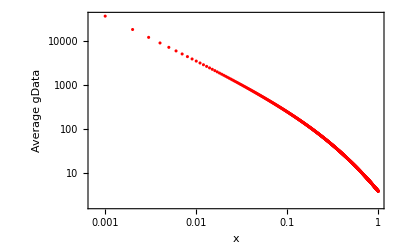

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
N1=1000;s=0.01;h=0.5;x0=1/(2 2 s h N1);
x1=NDSolveValue[{D[x2a[t],t]==h s*x2a[t]*(1-x2a[t]),x2a[0]==x0},x2a,{t,0,4500}];

averageGData={};

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,3500},{x,0,1}];
gData=Table[Sum[Datatfix[[j,2]] G[x,Datatfix[[j,1]]]/(x*(1-x)),{j,1,Length[Datatfix]}],{x,0.001,0.999,0.001}];
AppendTo[averageGData,gData];

averageGData1=Mean[averageGData];

xaxis=Table[x,{x,0.001,.999,0.001}];

ListLogLogPlot[Transpose[{xaxis,averageGData1}],Frame->True,FrameLabel->{"x","Average gData"},FrameStyle->Directive[Thickness[0.005],Black], PlotStyle->Red]
```

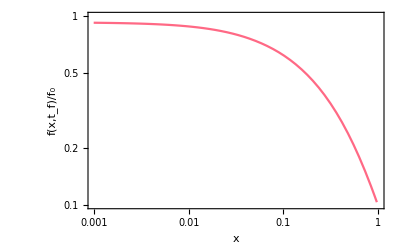

```mathematica
Data1s=Transpose[{xaxis,xaxis averageGData1/theta}];
(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.0001;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];
(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];
a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},PlotStyle->{RGBColor[1,0.41,0.52] },Frame->True,FrameLabel->{"x","f(x,t_f)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotRange->{{0.001,1},{0.1,1}}];
a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_f)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.8"},PlotRange->{{0.001,1},{0.1,1}}(*, PlotMarkers->"●"*), Joined->{True, Dashed}];

(*Show both plots*)
Show[a1sInterpolated]
```

```mathematica
Quit[]
```

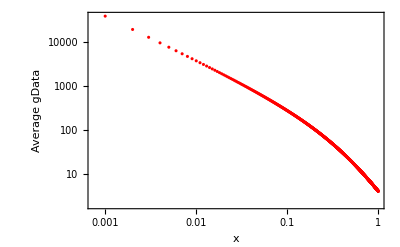

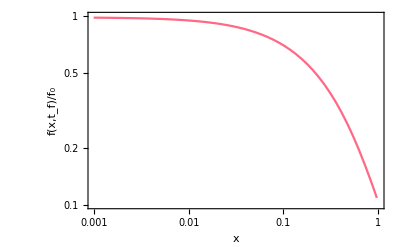

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
N1=1000;s=0.01;h=0.5;x0=1/(2 2 s h N1);
x1=NDSolveValue[{D[x2a[t],t]==h s*x2a[t]*(1-x2a[t]),x2a[0]==x0},x2a,{t,0,4500}];

averageGData={};
h=0.5;
Tfix=Log[2 2 N1 s  ]/(h  s (1-h))+ (EulerGamma+ (2- 3 h)Log[h] + (3 h-1) Log[1-h])/(h  s (1-h));
G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,3500},{x,0,1}];
gData=Table[G[x,Tfix]/(x*(1-x)),{x,0.001,0.999,0.001}];
AppendTo[averageGData,gData];

averageGData1=Mean[averageGData];

xaxis=Table[x,{x,0.001,.999,0.001}];

ListLogLogPlot[Transpose[{xaxis,averageGData1}],Frame->True,FrameLabel->{"x","Average gData"},FrameStyle->Directive[Thickness[0.005],Black], PlotStyle->Red]

Data1s=Transpose[{xaxis,xaxis averageGData1/theta}];
(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.0001;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];
(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];
a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},PlotStyle->{RGBColor[1,0.41,0.52] },Frame->True,FrameLabel->{"x","f(x,t_f)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotRange->{{0.001,1},{0.1,1}}];
a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_f)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.8"},PlotRange->{{0.001,1},{0.1,1}}(*, PlotMarkers->"●"*), Joined->{True, Dashed}];

(*Show both plots*)
Show[a1sInterpolated]
```

```mathematica
a3=-Graphics-;
```

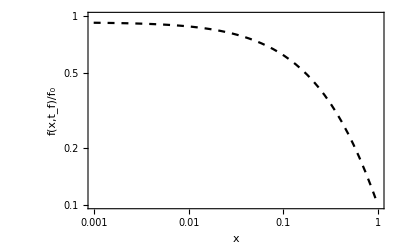
```mathematica
a3=-Graphics-;
```

### simulations and has main figure

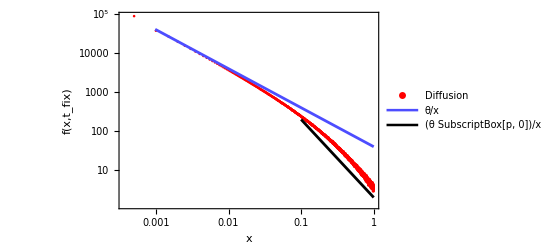

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L; (* theta= 2 N mu *)
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/N_1000_s_0.01_h_0.5/dist_txt_files/Ns_10_sfs.txt"];
(*e1:1 t:5000000 and theta is 0.100000 *)
datas1s=ReadList[s1s,{Number,Number}];

Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];


Data1s=Transpose@{x11s, x21s};

a1s=ListLogLogPlot[{Data1s}, Frame->True, FrameLabel->{"x","f(x,t_fix)"},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"Diffusion"}];
(*a2s=LogLogPlot[{theta/x, theta/(x^2 2 N1 0.01 0.5)},{x,0,1},Frame->True, FrameLabel->{"x","distribution"},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"θ/x","(θ SubscriptBox[p, 0])/x^2"}]; *)
a2s=LogLogPlot[theta/x,{x,0,1},PlotStyle->{Lighter[Blue,0.3],Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\), \(x\)]\)",Large]}];

a3s=LogLogPlot[theta/(20 x^2),{x,0.1,1},PlotStyle->{Black,Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\\\ 
   \*SubscriptBox[\(p\), \(0\)]\), SuperscriptBox[\(x\), \(2\)]]\)",Large]}];

Show[a1s,a2s,a3s]
```

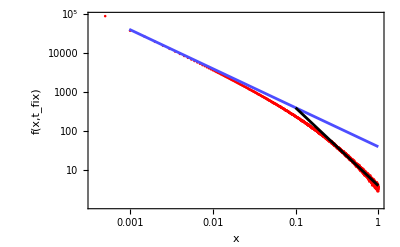

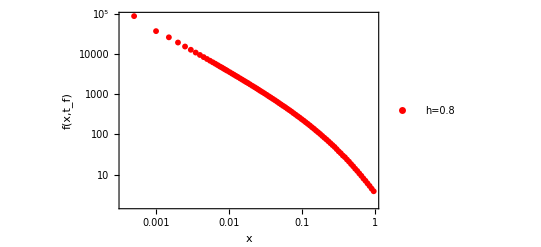

```mathematica
Data1s=Transpose@{x11s, x21s};
(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.001;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_f)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_f)"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.8"},PlotRange->All, PlotMarkers->{"●",6}];

(*Show both plots*)
Show[a1sCombined]
```

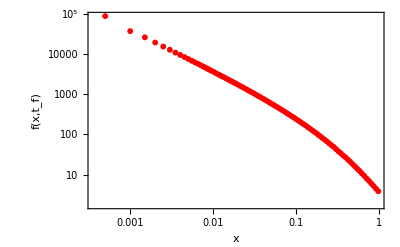
```mathematica
a1=-Graphics-;
```

```mathematica
Quit[]
```

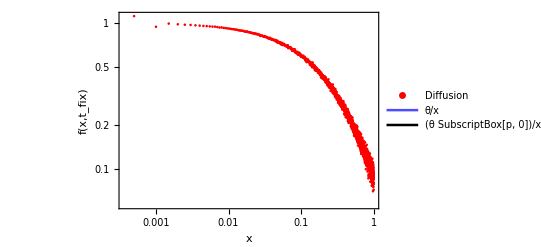

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L; (* theta= 2 N mu *)
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/N_1000_s_0.01_h_0.5/dist_txt_files/Ns_10_sfs.txt"];
(*e1:1 t:5000000 and theta is 0.100000 *)
datas1s=ReadList[s1s,{Number,Number}];

Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];


Data1s=Transpose@{x11s,x11s x21s/theta};

a1s=ListLogLogPlot[{Data1s}, Frame->True, FrameLabel->{"x","f(x,t_fix)"},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"Diffusion"}];
(*a2s=LogLogPlot[{theta/x, theta/(x^2 2 N1 0.01 0.5)},{x,0,1},Frame->True, FrameLabel->{"x","distribution"},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"θ/x","(θ SubscriptBox[p, 0])/x^2"}]; *)
a2s=LogLogPlot[theta/x,{x,0,1},PlotStyle->{Lighter[Blue,0.3],Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\), \(x\)]\)",Large]}];

a3s=LogLogPlot[theta/(10 x^2),{x,0.1,1},PlotStyle->{Black,Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\\\ 
   \*SubscriptBox[\(p\), \(0\)]\), SuperscriptBox[\(x\), \(2\)]]\)",Large]}];

Show[a1s,a2s,a3s]
```

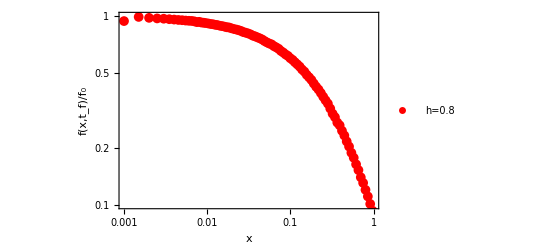

```mathematica
Data1s=Transpose@{x11s,x11s x21s/theta};
(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.001;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f(x,t_f)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_f)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.8"},PlotRange->{{0.001,1},{0.1,1}}, PlotMarkers->{"●",10}];

(*Show both plots*)
Show[a1sCombined]
```

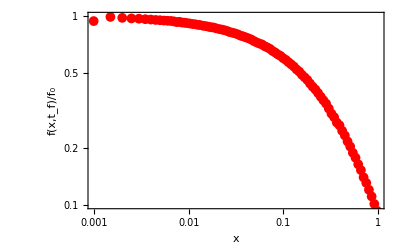
```mathematica
a4=-Graphics-;
```

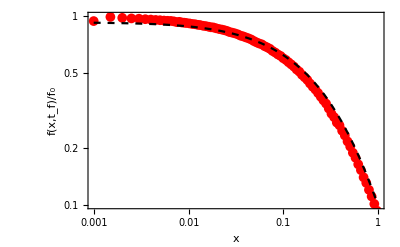

```mathematica
Show[a4,a3]
```

```mathematica
Show[a2,a1,a4,a3]
```

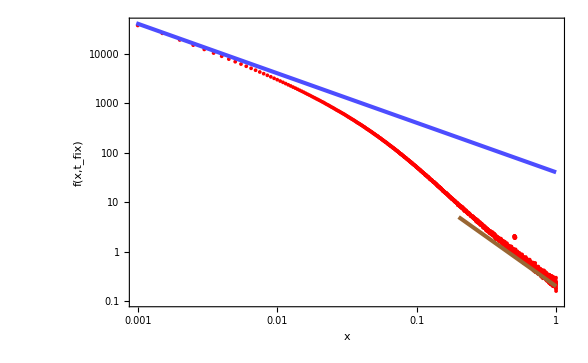

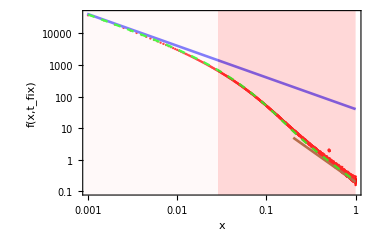

```mathematica
Show[a1,a2,a3,a4]
```

```mathematica
a=-Graphics-;
Show[a, ImageSize->700]
```

-Graphics-

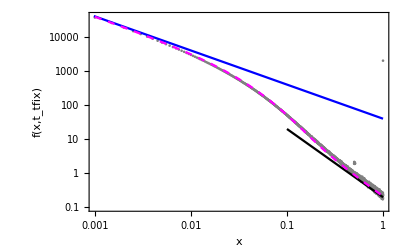

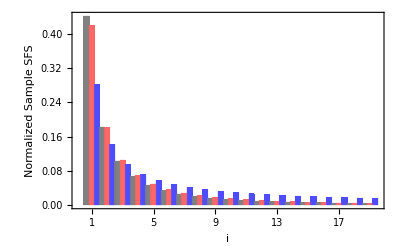

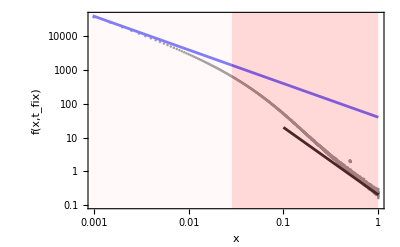
```mathematica
a1=-Graphics-;
```

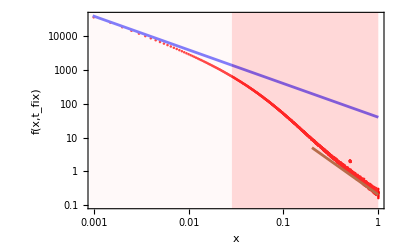
```mathematica
a1=-Graphics-;
```

```mathematica
Show[a1,a2]
```

-Graphics-

```mathematica
Quit[]
```

```mathematica
x1[220.18362426267285]
```

0.136635

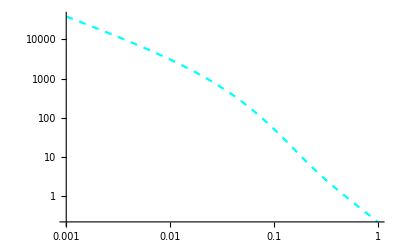

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.5;x0=1/(2 2 s h N1);
x1=NDSolveValue[{D[x2a[t],t]== s*x2a[t]*(1-x2a[t]) (x2a[t] + h (1- 2  x2a[t] )),x2a[0]==x0},x2a,{t,0,3000}];


pt=x1[220.18362426267285];
(*pt=x1[1290.3240671352746];*)
p0=1/(2 N1  2 s h);
a= Abs[h pt Log[1-pt]/(1-h)];
w[x_]:=16 N1 s h x pt;

LogLogPlot[((theta pt)/x + theta  pt/x( ⅇ^((-w[x])/(4 a))/(4 a^2)(w[x]  Log[(4 a^2)/w[x]] +w[x] ExpIntegralEi[w[x]/(4 a)] + 4a) + ⅇ^((-w[x])/(4 a)) -1/a-1)), {x,0.001,1}, PlotStyle->{Cyan,Dashed}]
```

```mathematica
a2=-Graphics-;
```

```mathematica
Quit[]
```

### NS = 100

```mathematica
Quit[]
```

NIntegrate::nlim: t1 = t is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: t1 = t is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

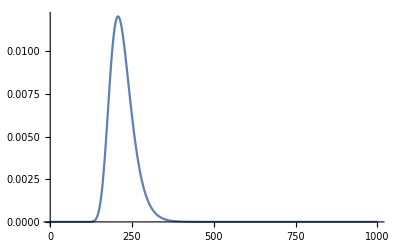

NIntegrate::nlim: t1 = t is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

$Aborted

Transpose::nmtx: The first two levels of {{1,2,3,4,5,6,7,8,9,10,«990»},weightValues} cannot be transposed.

```mathematica
N1=1000;
s0=0.1;
h=0.5;
x0=1/(2 N1);


si[t_]:=s0;


taui[t_]:=h*NIntegrate[si[t1],{t1,0,t}];


pf1=2/(1+NIntegrate[Exp[-taui[t]],{t,0,Infinity}]);

C1=2 N1 pf1;


B[Te_]:=B[Te]=(2 N1)/NIntegrate[Exp[(1-h)/h taui[t]],{t,0,Te}];


pdfsd[Te_]:=pdfsd[Te]=(1/(2 N1)) C1 B[Te]^2 Exp[taui[Te]] 2 BesselK[0,2 Sqrt[B[Te] C1]];


pdfgenh[Te_]:=pdfgenh[Te]=h/(1-h) (C1 B[Te]^2)/(2 N1) Exp[(1-h)/h taui[Te]]*NIntegrate[q^(-(h/(1-h))) Exp[-B[Te] q] Exp[-C1 q^(-h/(1-h))],{q,0,Infinity},MaxRecursion->20];


a3=Plot[pdfgenh[t],{t,1,1000},PlotRange->All,PlotPoints->50]
timePoints=Range[1,1000,1];


weightValues=pdfgenh/@timePoints;

(*Combine time points and their corresponding weights into a single list*)
Datatfix=Transpose[{timePoints,weightValues}];
```

```mathematica
Quit[]
```

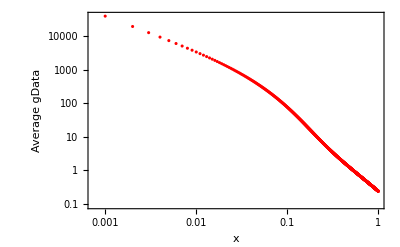

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.5;x0=1/(2 2 s h N1);
x1=NDSolveValue[{D[x2a[t],t]==h s*x2a[t]*(1-x2a[t]),x2a[0]==x0},x2a,{t,0,1000}];

averageGData={};

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1000},{x,0,1}];
gData=Table[Sum[Datatfix[[j,2]] G[x,Datatfix[[j,1]]]/(x*(1-x)),{j,1,Length[Datatfix]}],{x,0.001,0.999,0.001}];
AppendTo[averageGData,gData];
averageGData1=Mean[averageGData];

xaxis=Table[x,{x,0.001,.999,0.001}];

ListLogLogPlot[Transpose[{xaxis,averageGData1}],Frame->True,FrameLabel->{"x","Average gData"},FrameStyle->Directive[Thickness[0.005],Black], PlotStyle->Red]
```

### Datatfix

```mathematica
Datatfix={{1,0.},{2,0.},{3,4.151047251472476*^-295},{4,4.1989426350820763*^-252},{5,1.941016690045759*^-222},{6,2.608276309898929*^-200},{7,6.179003509137429*^-183},{8,8.628412609395431*^-169},{9,5.835201420580849*^-157},{10,7.381361825898198*^-147},{11,4.34982745842995*^-138},{12,2.2685953183050454*^-130},{13,1.6693189929204664*^-123},{14,2.455247572800332*^-117},{15,9.41964387451671*^-112},{16,1.160006854315179*^-106},{17,5.4050572873193316*^-102},{18,1.0877283612689127*^-97},{19,1.0530859161798492*^-93},{20,5.361157670900453*^-90},{21,1.545578009678681*^-86},{22,2.6855336367126233*^-83},{23,2.9650850710835503*^-80},{24,2.1763768897952057*^-77},{25,1.1041079593334904*^-74},{26,4.0040616035294655*^-72},{27,1.0689356054105126*^-69},{28,2.1554363856823506*^-67},{29,3.358070300673084*^-65},{30,4.1240145846763665*^-63},{31,4.06408513811136*^-61},{32,3.265288701530391*^-59},{33,2.169609722662746*^-57},{34,1.2075471499563959*^-55},{35,5.695167111170505*^-54},{36,2.300013037798592*^-52},{37,8.029694068621752*^-51},{38,2.444371809873805*^-49},{39,6.539785272992895*^-48},{40,1.5489105839715121*^-46},{41,3.269162447132942*^-45},{42,6.186487317501928*^-44},{43,1.055584319963514*^-42},{44,1.6324547956672707*^-41},{45,2.2992175785884245*^-40},{46,2.9624438473054035*^-39},{47,3.5063509239106313*^-38},{48,3.8271558064045856*^-37},{49,3.866164028549318*^-36},{50,3.626880146769935*^-35},{51,3.1696176363056452*^-34},{52,2.5881399328855507*^-33},{53,1.9800857448663394*^-32},{54,1.4230884357957956*^-31},{55,9.631670940860237*^-31},{56,6.1532220496451005*^-30},{57,3.71867270076802*^-29},{58,2.1303898529866206*^-28},{59,1.1592292258659857*^-27},{60,6.0024358686058696*^-27},{61,2.962792797068715*^-26},{62,1.3964319439816775*^-25},{63,6.294721089584316*^-25},{64,2.717888382807554*^-24},{65,1.1256782266227035*^-23},{66,4.478416851509304*^-23},{67,1.7137018831624165*^-22},{68,6.315300147878256*^-22},{69,2.2440072735559535*^-21},{70,7.69710166416402*^-21},{71,2.5514258945071954*^-20},{72,8.18185352299972*^-20},{73,2.540826321195483*^-19},{74,7.648507396566395*^-19},{75,2.2339017561236765*^-18},{76,6.336196011097267*^-18},{77,1.746814864980432*^-17},{78,4.684695490987933*^-17},{79,1.2231540365352046*^-16},{80,3.1115918235205906*^-16},{81,7.718094467615425*^-16},{82,1.8679979768425794*^-15},{83,4.414519923852513*^-15},{84,1.019348889008096*^-14},{85,2.301315327720187*^-14},{86,5.08294559418484*^-14},{87,1.0990158784361496*^-13},{88,2.3275345518857856*^-13},{89,4.831012992839563*^-13},{90,9.832603122724718*^-13},{91,1.9634408466396947*^-12},{92,3.848661030617397*^-12},{93,7.40901717071295*^-12},{94,1.4014594447602657*^-11},{95,2.605991244202105*^-11},{96,4.765793128315711*^-11},{97,8.575484224870336*^-11},{98,1.518899604915662*^-10},{99,2.649272774987421*^-10},{100,4.5522534720939185*^-10},{101,7.709003141338209*^-10},{102,1.2870843501179057*^-9},{103,2.119400540646493*^-9},{104,3.443277277345807*^-9},{105,5.5212212713639226*^-9},{106,8.740766706930477*^-9},{107,1.366652296482317*^-8},{108,2.1110552881173496*^-8},{109,3.222621780221304*^-8},{110,4.863160491412253*^-8},{111,7.256967501258395*^-8},{112,1.071132906910046*^-7},{113,1.5642424813441047*^-7},{114,2.2607626951384421*^-7},{115,3.234525351464234*^-7},{116,4.5822865384976217*^-7},{117,6.429518904135728*^-7},{118,8.937268949845144*^-7},{119,1.231017021205386*^-6},{120,1.6805685021735479*^-6},{121,2.274462220215032*^-6},{122,3.0522945299676313*^-6},{123,4.062484580425064*^-6},{124,5.363700873910105*^-6},{125,7.026394485742704*^-6},{126,9.134420576502699*^-6},{127,0.000011786723729324329},{128,0.000015099056446895347},{129,0.000019205694084524976},{130,0.000024261103839283106},{131,0.000030441520413983366},{132,0.000037946376975868137},{133,0.00004699953707811196},{134,0.00005785027189654513},{135,0.00007077392720233829},{136,0.00008607222643895225},{137,0.00010407315995607785},{138,0.00012513041597996682},{139,0.0001496223161245764},{140,0.00017795022714563223},{141,0.00021053643086990718},{142,0.0002478214456620386},{143,0.0002902608050241965},{144,0.000338321311654779},{145,0.0003924767980889451},{146,0.0004532034379314917},{147,0.0005209746624879418},{148,0.0005962557507400034},{149,0.0006794981673719203},{150,0.0007711337337234204},{151,0.0008715687188915334},{152,0.000981177960673044},{153,0.0011002990764081867},{154,0.0012292269047438158},{155,0.0013682082390137945},{156,0.0015174369565959832},{157,0.0016770496199630873},{158,0.0018471216288104624},{159,0.002027663985535426},{160,0.002218620729212662},{161,0.002419867080444667},{162,0.0026312083272395886},{163,0.002852379469391826},{164,0.0030830456261394515},{165,0.003322803199431707},{166,0.003571181773220509},{167,0.0038276467180271556},{168,0.004091602459830286},{169,0.004362396363240731},{170,0.004639323171102359},{171,0.004921629936176424},{172,0.005208521375485127},{173,0.005499165574226702},{174,0.005792699963914699},{175,0.006088237498494226},{176,0.006384872952577875},{177,0.006681689267529671},{178,0.0069777638737983155},{179,0.00727217492153483},{180,0.007564007355992076},{181,0.007852358779354937},{182,0.008136345046348838},{183,0.008415105547080958},{184,0.00868780813694933},{185,0.008953653679979297},{186,0.009211880178497426},{187,0.009461766468521095},{188,0.009702635466561893},{189,0.00993385695942514},{190,0.010154849934198684},{191,0.010365084452580763},{192,0.010564083073826318},{193,0.010751421841922197},{194,0.010926730850363466},{195,0.011089694404538454},{196,0.01124005080362},{197,0.011377591766348033},{198,0.011502161526960982},{199,0.011613655628935347},{200,0.011712019445153165},{201,0.011797246453661807},{202,0.011869376298355064},{203,0.011928492663723663},{204,0.0119747209923322},{205,0.012008226072916134},{206,0.012029209525994728},{207,0.012037907212697109},{208,0.012034586591136851},{209,0.012019544043178235},{210,0.011993102192843719},{211,0.011955607235951031},{212,0.011907426298861786},{213,0.011848944842498408},{214,0.011780564126065646},{215,0.011702698743212345},{216,0.011615774241708517},{217,0.011520224836106136},{218,0.011416491221308828},{219,0.011305018493508992},{220,0.01118625418356652},{221,0.01106064640660665},{222,0.010928642130411568},{223,0.010790685564071263},{224,0.01064721666734632},{225,0.010498669780278717},{226,0.010345472371764395},{227,0.010188043905070767},{228,0.010026794817642754},{229,0.009862125611984513},{230,0.00969442605393122},{231,0.009524074474228884},{232,0.009351437169015852},{233,0.009176867894543297},{234,0.009000707451277333},{235,0.00882328336792936},{236,0.00864490960272108},{237,0.008465886364881822},{238,0.00828650016208229},{239,0.008107023521385193},{240,0.00792771514364187},{241,0.0077488199404423625},{242,0.007570569151566309},{243,0.007393180507127953},{244,0.00721685842995449},{245,0.007041794273915279},{246,0.006868166594109086},{247,0.006696141445015374},{248,0.006525872702918019},{249,0.006357502409117392},{250,0.0061911611306176275},{251,0.006026968335484171},{252,0.005865032779225927},{253,0.005705452900856585},{254,0.005548317224869259},{255,0.00539370476764898},{256,0.005241685445986877},{257,0.0050923204858414305},{258,0.0049456628296292915},{259,0.004801757540495436},{260,0.004660642202172029},{261,0.00452234731318627},{262,0.0043868966743194245},{263,0.004254307768352964},{264,0.004124592131263798},{265,0.003997755714148117},{266,0.003873799235264416},{267,0.003752718521688727},{268,0.003634504840169495},{269,0.0035191452168563788},{270,0.003406622745656299},{271,0.0032969168850424816},{272,0.0031900037432092574},{273,0.003085856351526168},{274,0.0029844449263004727},{275,0.002885737118906698},{276,0.002789698254385127},{277,0.002696291558649337},{278,0.0026054783744761745},{279,0.0025172183664811322},{280,0.0024314697153086443},{281,0.002348189301293944},{282,0.0022673328778428994},{283,0.00218885523493054},{284,0.002112710352627017},{285,0.0020388515459066623},{286,0.001967231599587107},{287,0.001897802895157967},{288,0.0018305175289654151},{289,0.001765327422368828},{290,0.0017021844241580635},{291,0.0016410404055571877},{292,0.0015818473481477124},{293,0.0015245574250361078},{294,0.0014691230755424357},{295,0.00141549707372549},{296,0.0013636325911792753},{297,0.0013134832541589565},{298,0.001265003195530051},{299,0.0012181471016771172},{300,0.0011728702548595682},{301,0.0011291285709811502},{302,0.0010868786332728485},{303,0.0010460777219550791},{304,0.0010066838403821482},{305,0.0009686557375555817},{306,0.0009319529273852454},{307,0.0008965357050926071},{308,0.000862365160613139},{309,0.0008294031894303066},{310,0.0007976125009428514},{311,0.0007669566245632534},{312,0.0007373999136319462},{313,0.0007089075475754059},{314,0.0006814455319584896},{315,0.000654980697151983},{316,0.0006294806953267062},{317,0.0006049139960954925},{318,0.00058124988087452},{319,0.000558458436083978},{320,0.000536510545305963},{321,0.0005153778804307962},{322,0.0004950328920984825},{323,0.00047544879917300566},{324,0.0004565995776856349},{325,0.000438459949114869},{326,0.00042100536814718706},{327,0.0004042120099774454},{328,0.0003880567572132102},{329,0.00037251718645658417},{330,0.00035757155452360916},{331,0.00034319878463981326},{332,0.00032937845218182303},{333,0.00031609077048745286},{334,0.0003033165764886098},{335,0.0002910373162999552},{336,0.00027923503078526216},{337,0.0002678923411325874},{338,0.0002569924344690554},{339,0.00024651904953490336},{340,0.000236456462459064},{341,0.0002267894726352495},{342,0.00021750338873814432},{343,0.00020858401486737913},{344,0.00020001763689732202},{345,0.0001917910089707669},{346,0.00018389134020187128},{347,0.00017630628162126568},{348,0.00016902391309147488},{349,0.00016203273105530253},{350,0.0001553216357011953},{351,0.00014887991897525476},{352,0.00014269725259109337},{353,0.0001367636763264836},{354,0.00013106958656949216},{355,0.00012560572511664722},{356,0.00012036316827926292},{357,0.000115333315918589},{358,0.00011050788155148306},{359,0.0001058788816243615},{360,0.00010143862585684659},{361,0.00009717970751268581},{362,0.00009309499397674108},{363,0.00008917761758169334},{364,0.00008542096668208817},{365,0.00008181867697301764},{366,0.00007836462310972465},{367,0.00007505291020990498},{368,0.00007187786648019043},{369,0.00006883403488814214},{370,0.00006591616595088865},{371,0.00006311921039147883},{372,0.000060438312073652706},{373,0.00005786880115163073},{374,0.00005540618743052192},{375,0.00005304615393295302},{376,0.00005078455072792639},{377,0.00004861738859402395},{378,0.00004654083378254239},{379,0.00004455120175912804},{380,0.00004264495203622741},{381,0.00004081868282167731},{382,0.000039069125902269324},{383,0.00003739314169729384},{384,0.0000357877144775829},{385,0.00003424994774560794},{386,0.00003277705977223623},{387,0.000031366379285800606},{388,0.00003001534130919075},{389,0.00002872148314073707},{390,0.000027482440474722996},{391,0.00002629594365742652},{392,0.000025159814074666507},{393,0.000024071960666898696},{394,0.0000230303765679855},{395,0.000022033135863838823},{396,0.000021078390467213606},{397,0.000020164367155095347},{398,0.00001928936441453749},{399,0.000018451750145217068},{400,0.00001764995846239918},{401,0.000016882487349907102},{402,0.00001614789610811625},{403,0.0000154448029444047},{404,0.000014771882652904125},{405,0.000014127864380563488},{406,0.000013511529476556649},{407,0.000012921709422561713},{408,0.000012357283840242284},{409,0.000011817178574513765},{410,0.000011300363849028592},{411,0.000010805852491754474},{412,0.000010332698228166285},{413,9.87999403945038*^-6},{414,9.44687058398223*^-6},{415,9.032494679091803*^-6},{416,8.636067841511751*^-6},{417,8.256824884186519*^-6},{418,7.8940325674471*^-6},{419,7.546988323468246*^-6},{420,7.215018905908449*^-6},{421,6.897479401472125*^-6},{422,6.593751870638248*^-6},{423,6.30324434680196*^-6},{424,6.025389753577599*^-6},{425,5.759644884844954*^-6},{426,5.505489425094661*^-6},{427,5.262425008566899*^-6},{428,5.029974315728443*^-6},{429,4.807680205682334*^-6},{430,4.595104883154085*^-6},{431,4.391829098743771*^-6},{432,4.197451381180414*^-6},{433,4.0115873003579705*^-6},{434,3.8338687599764195*^-6},{435,3.6639433186521116*^-6},{436,3.5014735384026746*^-6},{437,3.3461363594505117*^-6},{438,3.1976225003267336*^-6},{439,3.055635882294744*^-6},{440,2.9198930771473604*^-6},{441,2.790122777466563*^-6},{442,2.6660652884678862*^-6},{443,2.547472040583766*^-6},{444,2.434105121971363*^-6},{445,2.3257368301605644*^-6},{446,2.2221492420868344*^-6},{447,2.1231338017820034*^-6},{448,2.028490925022943*^-6},{449,1.9380296202694494*^-6},{450,1.8515671252106199*^-6},{451,1.7689285583835843*^-6},{452,1.689946585168722*^-6},{453,1.6144610975495238*^-6},{454,1.542318907310977*^-6},{455,1.4733734518495722*^-6},{456,1.4074845122718076*^-6},{457,1.344517943222595*^-6},{458,1.284345413978367*^-6},{459,1.2268441603485548*^-6},{460,1.1718967469469661*^-6},{461,1.1193908394116893*^-6},{462,1.0692189861684409*^-6},{463,1.0212784093483374*^-6},{464,9.75470804486162*^-7},{465,9.317021486399053*^-7},{466,8.898825165866181*^-7},{467,8.499259047631254*^-7},{468,8.117500626333183*^-7},{469,7.752763311764253*^-7},{470,7.4042948820271*^-7},{471,7.071376002148176*^-7},{472,6.753318805441872*^-7},{473,6.449465535027795*^-7},{474,6.159187243008177*^-7},{475,5.881882544912068*^-7},{476,5.616976427109766*^-7},{477,5.36391910499307*^-7},{478,5.12218492980645*^-7},{479,4.891271342098901*^-7},{480,4.670697869849566*^-7},{481,4.4600051693984824*^-7},{482,4.258754107390246*^-7},{483,4.066524882011548*^-7},{484,3.882916181873073*^-7},{485,3.7075443809544506*^-7},{486,3.540042768094926*^-7},{487,3.380060809574803*^-7},{488,3.2272634433928133*^-7},{489,3.0813304039016917*^-7},{490,2.941955575519279*^-7},{491,2.808846374285746*^-7},{492,2.681723156087908*^-7},{493,2.5603186504203055*^-7},{494,2.4443772672022104*^-7},{495,2.33365533539513*^-7},{496,2.2279190930762896*^-7},{497,2.1269457269298918*^-7},{498,2.0305221613372975*^-7},{499,1.9384447754910923*^-7},{500,1.850518988007454*^-7},{501,1.7665588595212625*^-7},{502,1.686386712562737*^-7},{503,1.6098327679513378*^-7},{504,1.53673479700146*^-7},{505,1.4669377876135447*^-7},{506,1.4002936304894208*^-7},{507,1.3366608090138914*^-7},{508,1.2759041117101857*^-7},{509,1.2178943531204902*^-7},{510,1.1625081076303888*^-7},{511,1.1096274549230861*^-7},{512,1.0591397365621863*^-7},{513,1.0109373232231114*^-7},{514,9.649173921133565*^-8},{515,9.209817141413801*^-8},{516,8.790364504465153*^-8},{517,8.389919575229742*^-8},{518,8.007626021174492*^-8},{519,7.642665813872084*^-8},{520,7.294257565203029*^-8},{521,6.961654846989765*^-8},{522,6.644144687092994*^-8},{523,6.34104605838822*^-8},{524,6.051708463242646*^-8},{525,5.775510575501583*^-8},{526,5.511858942320449*^-8},{527,5.260186743235675*^-8},{528,5.01995260397942*^-8},{529,4.7906394626498885*^-8},{530,4.5717534859514285*^-8},{531,4.362823033316671*^-8},{532,4.163397666817939*^-8},{533,3.973047204865802*^-8},{534,3.791360817778741*^-8},{535,3.617946163391747*^-8},{536,3.45242856094934*^-8},{537,3.2944502016046035*^-8},{538,3.1436693939184676*^-8},{539,2.9997598428219345*^-8},{540,2.862409960572575*^-8},{541,2.7313222082992664*^-8},{542,2.606212466791091*^-8},{543,2.486809435244643*^-8},{544,2.372854056739115*^-8},{545,2.2640989692621482*^-8},{546,2.1603079811603253*^-8},{547,2.0612555699371468*^-8},{548,1.9667264033686588*^-8},{549,1.876514881952895*^-8},{550,1.790424701750411*^-8},{551,1.7082684367169764*^-8},{552,1.629867139666152*^-8},{553,1.5550499610353787*^-8},{554,1.483653784685607*^-8},{555,1.4155228799319877*^-8},{556,1.3505085691501202*^-8},{557,1.2884689102373674*^-8},{558,1.2292683932475038*^-8},{559,1.1727776506162912*^-8},{560,1.1188731803453887*^-8},{561,1.0674370815785259*^-8},{562,1.0183568020182545*^-8},{563,9.715248966568506*^-9},{564,9.268387973185644*^-9},{565,8.842005925325997*^-9},{566,8.43516817277666*^-9},{567,8.04698252159067*^-9},{568,7.676597315985789*^-9},{569,7.32319960635471*^-9},{570,6.9860133995478215*^-9},{571,6.664297987757205*^-9},{572,6.357346352496087*^-9},{573,6.064483640323751*^-9},{574,5.785065707116967*^-9},{575,5.518477727833299*^-9},{576,5.264132868798071*^-9},{577,5.021471019898318*^-9},{578,4.78995758367819*^-9},{579,4.569082319086773*^-9},{580,4.358358237302776*^-9},{581,4.157320547310083*^-9},{582,3.965525649103484*^-9},{583,3.7825501721565195*^-9},{584,3.6079900573670327*^-9},{585,3.4414596804164805*^-9},{586,3.2825910147064084*^-9},{587,3.1310328320946365*^-9},{588,2.986449939733223*^-9},{589,2.8485224515497435*^-9},{590,2.7169450918764634*^-9},{591,2.5914265318231673*^-9},{592,2.4716887553270905*^-9},{593,2.357466452485664*^-9},{594,2.248506442208902*^-9},{595,2.1445671200482145*^-9},{596,2.045417931209196*^-9},{597,1.950838867429295*^-9},{598,1.8606199866458609*^-9},{599,1.7745609544290112*^-9},{600,1.6924690790733423*^-9},{601,1.6141665293035657*^-9},{602,1.5394746640290606*^-9},{603,1.4682289227431647*^-9},{604,1.4002708262980956*^-9},{605,1.335449156944735*^-9},{606,1.2736196270013268*^-9},{607,1.214644562566819*^-9},{608,1.1583926016004472*^-9},{609,1.1047384057341762*^-9},{610,1.053562385078251*^-9},{611,1.0047504358665811*^-9},{612,9.581936894956294*^-10},{613,9.13788273426933*^-10},{614,8.714350829551594*^-10},{615,8.310395630139224*^-10},{616,7.925114999358071*^-10},{617,7.55764823575386*^-10},{618,7.207174170106092*^-10},{619,6.872909360260695*^-10},{620,6.554106363310525*^-10},{621,6.250052088401325*^-10},{622,5.960066222866152*^-10},{623,5.683499732008539*^-10},{624,5.419733426000772*^-10},{625,5.168176592612663*^-10},{626,4.928265692388234*^-10},{627,4.699463112609127*^-10},{628,4.48125597964842*^-10},{629,4.273155024158893*^-10},{630,4.074693498686988*^-10},{631,3.885426144759145*^-10},{632,3.704928206432845*^-10},{633,3.5327944904106727*^-10},{634,3.3686384677169346*^-10},{635,3.21209141687161*^-10},{636,3.062801606501471*^-10},{637,2.9204335147235527*^-10},{638,2.784667085494839*^-10},{639,2.655197017316296*^-10},{640,2.5317320858294536*^-10},{641,2.413994496244102*^-10},{642,2.3017192672182888*^-10},{643,2.1946536407026967*^-10},{644,2.0925565204552712*^-10},{645,1.9951979356396655*^-10},{646,1.902358529104644*^-10},{647,1.8138290691146487*^-10},{648,1.7294099834659472*^-10},{649,1.648910914937274*^-10},{650,1.5721502972726861*^-10},{651,1.4989549500351928*^-10},{652,1.4291596931890943*^-10},{653,1.3626069782528685*^-10},{654,1.2991465367387653*^-10},{655,1.2386350449607175*^-10},{656,1.1809358040050925*^-10},{657,1.1259184344497395*^-10},{658,1.0734585851026396*^-10},{659,1.0234376551179621*^-10},{660,9.757425288781992*^-11},{661,9.302653230548487*^-11},{662,8.869031452951925*^-11},{663,8.455578639888967*^-11},{664,8.061358886089865*^-11},{665,7.685479603304168*^-11},{666,7.327089519795208*^-11},{667,6.985376773718016*^-11},{668,6.659567093959975*^-11},{669,6.34892206523653*^-11},{670,6.052737469251567*^-11},{671,5.7703417098099175*^-11},{672,5.501094304388394*^-11},{673,5.244384444686074*^-11},{674,4.9996296276039375*^-11},{675,4.7662743466476383*^-11},{676,4.543788844171568*^-11},{677,4.331667921116888*^-11},{678,4.1294298016040486*^-11},{679,3.936615050474461*^-11},{680,3.752785537538918*^-11},{681,3.5775234558926166*^-11},{682,3.410430380368191*^-11},{683,3.2511263692386496*^-11},{684,3.099249110618103*^-11},{685,2.9544531061049174*^-11},{686,2.8164088925673565*^-11},{687,2.684802299834962*^-11},{688,2.5593337426564162*^-11},{689,2.4397175458520536*^-11},{690,2.325681297608396*^-11},{691,2.2169652401252548*^-11},{692,2.1133216785024274*^-11},{693,2.0145144243038994*^-11},{694,1.9203182619017743*^-11},{695,1.8305184399708078*^-11},{696,1.7449101864763305*^-11},{697,1.6632982460842793*^-11},{698,1.5854964389557616*^-11},{699,1.5113272403500498*^-11},{700,1.4406213772328478*^-11},{701,1.3732174495816422*^-11},{702,1.3089615612170235*^-11},{703,1.2477069736587073*^-11},{704,1.1893137736378986*^-11},{705,1.1336485563859208*^-11},{706,1.0805841235801283*^-11},{707,1.0299991952745029*^-11},{708,9.817781351611976*^-12},{709,9.358106885567703*^-12},{710,8.91991732518956*^-12},{711,8.502210375351069*^-12},{712,8.104030402466173*^-12},{713,7.724466270798036*^-12},{714,7.362649264018933*^-12},{715,7.017751128252138*^-12},{716,6.688982155080679*^-12},{717,6.375589482843487*^-12},{718,6.076855268306054*^-12},{719,5.792095124725724*^-12},{720,5.5206565513389575*^-12},{721,5.261917450536123*^-12},{722,5.015284714231024*^-12},{723,4.7801928764490816*^-12},{724,4.556104166449018*^-12},{725,4.342502468961153*^-12},{726,4.138898718613099*^-12},{727,3.944825770516601*^-12},{728,3.759838264826024*^-12},{729,3.583511612936498*^-12},{730,3.4154410303749865*^-12},{731,3.2552406168464005*^-12},{732,3.102542473427885*^-12},{733,2.9569958681425363*^-12},{734,2.8182664322663445*^-12},{735,2.686035407372941*^-12},{736,2.5599989079253222*^-12},{737,2.439867238592975*^-12},{738,2.325364212119259*^-12},{739,2.216226549978585*^-12},{740,2.112203261711536*^-12},{741,2.0130550768674567*^-12},{742,1.9185538988195716*^-12},{743,1.828482283978529*^-12},{744,1.7426329452264793*^-12},{745,1.660808278447814*^-12},{746,1.5828199110846058*^-12},{747,1.5084882716950263*^-12},{748,1.4376421795457112*^-12},{749,1.3701184532675512*^-12},{750,1.3057615377999167*^-12},{751,1.2444231486168889*^-12},{752,1.1859619325532342*^-12},{753,1.1302431444275215*^-12},{754,1.0771383387015901*^-12},{755,1.0265250755027688*^-12},{756,9.782866403538104*^-13},{757,9.323117769339015*^-13},{758,8.884944322993233*^-13},{759,8.467335139709672*^-13},{760,8.069326583392261*^-13},{761,7.690000098595147*^-13},{762,7.328480105382655*^-13},{763,6.983931992314282*^-13},{764,6.655560202919917*^-13},{765,6.342606411441935*^-13},{766,6.044347783587634*^-13},{767,5.76009531838412*^-13},{768,5.489192267335869*^-13},{769,5.231012627335652*^-13},{770,4.984959703833792*^-13},{771,4.75046474104357*^-13},{772,4.526985616034818*^-13},{773,4.314005593776686*^-13},{774,4.111032140219291*^-13},{775,3.9175957908189863*^-13},{776,3.7332490718397786*^-13},{777,3.557565471974721*^-13},{778,3.390138462011628*^-13},{779,3.23058056023864*^-13},{780,3.078522441486972*^-13},{781,2.933612087770681*^-13},{782,2.7955139785990953*^-13},{783,2.6639083190754044*^-13},{784,2.538490304074172*^-13},{785,2.418969416773243*^-13},{786,2.305068759956301*^-13},{787,2.1965244185548276*^-13},{788,2.0930848519735256*^-13},{789,1.9945103148100742*^-13},{790,1.900572304645051*^-13},{791,1.8110530356397182*^-13},{792,1.7257449367372312*^-13},{793,1.6444501733199336*^-13},{794,1.5669801912279514*^-13},{795,1.4931552820958147*^-13},{796,1.4228041690125435*^-13},{797,1.355763611560332*^-13},{798,1.2918780293038132*^-13},{799,1.2309991429281977*^-13},{800,1.1729856321242762*^-13},{801,1.1177028094958479*^-13},{802,1.065022309715381*^-13},{803,1.0148217932191988*^-13},{804,9.669846638048994*^-14},{805,9.213997993622386*^-14},{806,8.779612952889211*^-14},{807,8.365682198714494*^-14},{808,7.971243811247454*^-14},{809,7.595381045459626*^-14},{810,7.237220212339293*^-14},{811,6.895928661292187*^-14},{812,6.570712853067122*^-14},{813,6.260816526721195*^-14},{814,5.96551895061013*^-14},{815,5.6841332533223367*^-14},{816,5.4160048430436826*^-14},{817,5.1605098831393104*^-14},{818,4.9170538599579636*^-14},{819,4.685070184265527*^-14},{820,4.464018911264477*^-14},{821,4.253385471002009*^-14},{822,4.05267948179459*^-14},{823,3.8614336148160436*^-14},{824,3.6792025119025954*^-14},{825,3.505561754084478*^-14},{826,3.3401068784694544*^-14},{827,3.182452441215186*^-14},{828,3.0322311244322886*^-14},{829,2.8890928849619206*^-14},{830,2.7527041430680034*^-14},{831,2.6227470091758076*^-14},{832,2.4989184975562977*^-14},{833,2.380930070501627*^-14},{834,2.2685064756429295*^-14},{835,2.1613856012790242*^-14},{836,2.0593176206431706*^-14},{837,1.9620644636465506*^-14},{838,1.8693992623969262*^-14},{839,1.7811058257569457*^-14},{840,1.6969781373545172*^-14},{841,1.6168198773459057*^-14},{842,1.540443966629695*^-14},{843,1.467672132459159*^-14},{844,1.3983344939877725*^-14},{845,1.3322691699449646*^-14},{846,1.2693218981179977*^-14},{847,1.209345681443971*^-14},{848,1.1522004442151468*^-14},{849,1.0977527070097817*^-14},{850,1.0458752764626583*^-14},{851,9.964469496053268*^-15},{852,9.493522320950244*^-15},{853,9.044810696777425*^-15},{854,8.617285922671621*^-15},{855,8.209948700513725*^-15},{856,7.821846810414973*^-15},{857,7.452072895453812*^-15},{858,7.099762351254328*^-15},{859,6.7640913132127745*^-15},{860,6.444274739697477*^-15},{861,6.139564584726914*^-15},{862,5.849248056647316*^-15},{863,5.572645958663728*^-15},{864,5.3091111073833135*^-15},{865,5.058026825707264*^-15},{866,4.818805506582642*^-15},{867,4.590887244285397*^-15},{868,4.37373853004475*^-15},{869,4.166850998895857*^-15},{870,3.969740296075785*^-15},{871,3.781944846067991*^-15},{872,3.603024879092792*^-15},{873,3.4325613547011054*^-15},{874,3.2701549952640163*^-15},{875,3.1154253548978412*^-15},{876,2.968009932328867*^-15},{877,2.8275633254726653*^-15},{878,2.693756425792453*^-15},{879,2.5662756505677735*^-15},{880,2.444822211292191*^-15},{881,2.3291114165037218*^-15},{882,2.218872007430476*^-15},{883,2.1138455247876906*^-15},{884,2.0137857059603627*^-15},{885,1.918457909521304*^-15},{886,1.8276385677468134*^-15},{887,1.7411146645243342*^-15},{888,1.6586832379074934*^-15},{889,1.5801509060946913*^-15},{890,1.5053334157296679*^-15},{891,1.434055211293358*^-15},{892,1.3661490257293797*^-15},{893,1.3014554884192646*^-15},{894,1.2398227533183414*^-15},{895,1.1811061444138518*^-15},{896,1.1251678171153052*^-15},{897,1.071876436144885*^-15},{898,1.0211068684840581*^-15},{899,9.727398907762533*^-16},{900,9.266619105784382*^-16},{901,8.827647006219503*^-16},{902,8.409451457242353*^-16},{903,8.011050015638007*^-16},{904,7.631506647942137*^-16},{905,7.269929542504565*^-16},{906,6.925469018316023*^-16},{907,6.597315540895122*^-16},{908,6.284697825151768*^-16},{909,5.986881030767991*^-16},{910,5.703165041656848*^-16},{911,5.432882826807716*^-16},{912,5.17539887856164*^-16},{913,4.930107724131017*^-16},{914,4.69643250771935*^-16},{915,4.473823639306723*^-16},{916,4.261757507205901*^-16},{917,4.059735251323011*^-16},{918,3.8672815944057585*^-16},{919,3.6839437281220596*^-16},{920,3.5092902520883233*^-16},{921,3.3429101626545834*^-16},{922,3.184411889517155*^-16},{923,3.0334223777676766*^-16},{924,2.889586213255638*^-16},{925,2.752564789224027*^-16},{926,2.6220355122723185*^-16},{927,2.4976910457939073*^-16},{928,2.3792385891233335*^-16},{929,2.2663991907116247*^-16},{930,2.158907093729209*^-16},{931,2.05650911244964*^-16},{932,1.958964038806395*^-16},{933,1.8660420751969438*^-16},{934,1.7775242964375388*^-16},{935,1.6932021353701255*^-16},{936,1.6128768934424473*^-16},{937,1.5363592742501666*^-16},{938,1.463468939046364*^-16},{939,1.3940340337894319*^-16},{940,1.3278909524367632*^-16},{941,1.2648837372232936*^-16},{942,1.2048638379804355*^-16},{943,1.1476897354753767*^-16},{944,1.0932266082431772*^-16},{945,1.0413460184940095*^-16},{946,9.91925606744695*^-17},{947,9.448488052044618*^-17},{948,9.000045653427943*^-17},{949,8.572870961425068*^-17},{950,8.165956150657182*^-17},{951,7.778341110246291*^-17},{952,7.409111199814349*^-17},{953,7.057395078517114*^-17},{954,6.722362670036405*^-17},{955,6.403223206896797*^-17},{956,6.099223370629793*^-17},{957,5.809645519849904*^-17},{958,5.533806002090421*^-17},{959,5.271053545445153*^-17},{960,5.0207677262544467*^-17},{961,4.782357510375839*^-17},{962,4.555259857536547*^-17},{963,4.338938403657937*^-17},{964,4.1328821933350156*^-17},{965,3.936604478407859*^-17},{966,3.7496415721017337*^-17},{967,3.5715517567033995*^-17},{968,3.4019142461979335*^-17},{969,3.2403281913046664*^-17},{970,3.086411738305663*^-17},{971,2.9398011289911254*^-17},{972,2.8001498438682065*^-17},{973,2.6671277859005977*^-17},{974,2.5404205028638638*^-17},{975,2.4197284464909925*^-17},{976,2.3047662666696443*^-17},{977,2.195262139033985*^-17},{978,2.0909571250238218*^-17},{979,1.99160455834926*^-17},{980,1.8969694701013498*^-17},{981,1.8068280283540215*^-17},{982,1.7209670137459803*^-17},{983,1.6391833161293616*^-17},{984,1.561283455662541*^-17},{985,1.4870831265703204*^-17},{986,1.4164067625002113*^-17},{987,1.3490871224530549*^-17},{988,1.284964896315112*^-17},{989,1.2238883290647455*^-17},{990,1.1657128627700087*^-17},{991,1.1103007955361601*^-17},{992,1.0575209566008358*^-17},{993,1.0072483968133509*^-17},{994,9.593640937703132*^-18},{995,9.137546709139844*^-18},{996,8.703121299330486*^-18},{997,8.289335958362022*^-18},{998,7.89521074099097*^-18},{999,7.519812193132026*^-18},{1000,7.162251147924576*^-18}};
```

### DataDiffusion

```mathematica
datadiffusion=Transpose[{xaxis,averageGData1}];
```

```mathematica
Transpose[{xaxis,averageGData1}]
```

```mathematica
datadiffusion={{0.001,38831.0269497731},{0.002,19038.902446055028},{0.003,12446.472379664927},{0.004,9153.903603011524},{0.005,7181.230055640991},{0.006,5868.463522957638},{0.007,4932.752316031294},{0.008,4232.670941539673},{0.009000000000000001,3689.6499917412175},{0.010000000000000002,3256.5481004567478},{0.011,2903.3664685089025},{0.012,2610.106126435614},{0.013000000000000001,2362.921845176193},{0.014000000000000002,2151.9243707436103},{0.015,1969.8617650227748},{0.016,1811.2952437646593},{0.017,1672.0658952837643},{0.018000000000000002,1548.9391595854486},{0.019000000000000003,1439.3615772383594},{0.02,1341.2905135811593},{0.021,1253.072533152102},{0.022000000000000002,1173.3549447250589},{0.023,1101.0204215500185},{0.024,1035.1379665300371},{0.025,974.9256457524614},{0.026000000000000002,919.721921971262},{0.027000000000000003,868.9633584235635},{0.028,822.167100396753},{0.029,778.9169812960326},{0.030000000000000002,738.8524074956191},{0.031,701.659394506296},{0.032,667.0632838588399},{0.033,634.8227841878194},{0.034,604.7250638862669},{0.035,576.5816850170152},{0.036000000000000004,550.225214903007},{0.037000000000000005,525.5063871870194},{0.038,502.2917111427422},{0.039,480.4614487818096},{0.04,459.90789539249823},{0.041,440.5339117046332},{0.042,422.2516657430392},{0.043000000000000003,404.98155023410897},{0.044000000000000004,388.6512476366341},{0.045,373.1949198330548},{0.046,358.5525035110847},{0.047,344.6690954945693},{0.048,331.494414905945},{0.049,318.98233118437827},{0.05,307.09044873973437},{0.051000000000000004,295.77974046885754},{0.052000000000000005,285.01422355648873},{0.053000000000000005,274.7606719760829},{0.054,264.9883609330793},{0.055,255.66883918524817},{0.056,246.7757257554223},{0.057,238.28452804108434},{0.058,230.17247873839025},{0.059000000000000004,222.41838934840644},{0.060000000000000005,215.00251833095214},{0.061,207.90645222516198},{0.062,201.11299827277392},{0.063,194.6060872660446},{0.064,188.370685501963},{0.065,182.39271486207386},{0.066,176.6589801560863},{0.067,171.1571029703566},{0.068,165.87546135161125},{0.069,160.8031347339172},{0.07,155.92985358456548},{0.07100000000000001,151.2459533036024},{0.07200000000000001,146.74233196345992},{0.07300000000000001,142.41041152043192},{0.074,138.2421021695793},{0.075,134.22976954964764},{0.076,130.36620453550788},{0.077,126.64459538285527},{0.078,123.05850201407263},{0.079,119.60183225551276},{0.08,116.26881985544112},{0.081,113.05400412874725},{0.082,109.95221108953854},{0.083,106.95853594611829},{0.084,104.0683268448142},{0.085,101.27716975978824},{0.08600000000000001,98.58087443554744},{0.08700000000000001,95.97546129743688},{0.08800000000000001,93.45714925311395},{0.089,91.02234431490439},{0.09,88.66762897919244},{0.091,86.38975230459506},{0.092,84.18562063573894},{0.093,82.05228892404459},{0.094,79.98695260103489},{0.095,77.98693996345585},{0.096,76.04970503287332},{0.097,74.17282085549506},{0.098,72.35397321076232},{0.099,70.59095469979853},{0.1,68.88165918710969},{0.101,67.22407657104883},{0.10200000000000001,65.61628786046506},{0.10300000000000001,64.05646053672199},{0.10400000000000001,62.5428441818644},{0.10500000000000001,61.07376635517944},{0.106,59.64762870173916},{0.107,58.26290327773484},{0.108,56.91812907854223},{0.109,55.61190875648748},{0.11,54.34290551622909},{0.111,53.10984017654605},{0.112,51.91148838811912},{0.113,50.746677997632034},{0.114,49.61428654919592},{0.115,48.51323891472845},{0.116,47.44250504549271},{0.117,46.401097837539545},{0.11800000000000001,45.38807110428163},{0.11900000000000001,44.40251764988739},{0.12000000000000001,43.443567437604834},{0.121,42.510385847508836},{0.122,41.6021720185325},{0.123,40.71815726997426},{0.124,39.857603597982056},{0.125,39.01980224280615},{0.126,38.219073888608804},{0.127,37.43949613618799},{0.128,36.680382352735414},{0.129,35.941071840568284},{0.13,35.22092878046445},{0.131,34.51934122298824},{0.132,33.835720125259485},{0.133,33.16949843077225},{0.134,32.52013019000687},{0.135,31.88708971972287},{0.136,31.269870798933468},{0.137,30.667985899686588},{0.138,30.0809654508832},{0.139,29.508357133465534},{0.14,28.949725205403865},{0.14100000000000001,28.404649854998933},{0.14200000000000002,27.872726581100594},{0.14300000000000002,27.353565598922685},{0.14400000000000002,26.846791270205753},{0.14500000000000002,26.352041556548624},{0.146,25.86896749479591},{0.147,25.397232693426233},{0.148,24.936512848946126},{0.149,24.486495281344986},{0.15,24.046878487719127},{0.151,23.61737171321863},{0.152,23.197694538516448},{0.153,22.787576483040215},{0.154,22.386756623246214},{0.155,21.994983225254025},{0.156,21.612013391192942},{0.157,21.237612718645874},{0.158,20.87155497260684},{0.159,20.51362176939789},{0.16,20.163602272018327},{0.161,19.821292896426126},{0.162,19.486497028275622},{0.163,19.15902474965866},{0.164,18.838692575418673},{0.165,18.52532319862835},{0.166,18.218745244841177},{0.167,17.92028965762482},{0.168,17.63125721634918},{0.169,17.348467704510306},{0.17,17.07175327803695},{0.171,16.800951345348746},{0.17200000000000001,16.535904398269437},{0.17300000000000001,16.276459848686},{0.17400000000000002,16.02246987072161},{0.17500000000000002,15.773791248201317},{0.17600000000000002,15.53028522719757},{0.177,15.291817373455686},{0.178,15.058257434504515},{0.179,14.829479206269141},{0.18,14.605360404009247},{0.181,14.385782537414439},{0.182,14.170630789696443},{0.183,13.959793900523334},{0.184,13.753164052649383},{0.185,13.55063676209892},{0.186,13.352110771770114},{0.187,13.157487948329148},{0.188,12.9666731822713},{0.189,12.77957429103058},{0.19,12.596101925024826},{0.191,12.416169476526935},{0.192,12.239692991258936},{0.193,12.066591082608385},{0.194,11.89678484837187},{0.195,11.730197789933543},{0.196,11.566755733790366},{0.197,11.406386755340513},{0.198,11.249021104852696},{0.199,11.094591135539163},{0.2,10.943031233657836},{0.201,10.794277750571007},{0.202,10.64826893669263},{0.203,10.504944877257191},{0.20400000000000001,10.364247429846854},{0.20500000000000002,10.226120163615764},{0.20600000000000002,10.090508300152385},{0.20700000000000002,9.957358655923462},{0.20800000000000002,9.826619586245503},{0.20900000000000002,9.699122484187207},{0.21,9.574366436188503},{0.211,9.451856169798043},{0.212,9.33154028086106},{0.213,9.213368752233137},{0.214,9.097292916357427},{0.215,8.983265418847772},{0.216,8.871240183045622},{0.217,8.761172375517653},{0.218,8.653018372465324},{0.219,8.546735727015001},{0.22,8.442283137361745},{0.221,8.339620415738672},{0.222,8.238708458185421},{0.223,8.13950921509079},{0.224,8.041985662484583},{0.225,7.9461017740551405},{0.226,7.851822493869766},{0.227,7.759113709775892},{0.228,7.667942227461742},{0.229,7.578275745156205},{0.23,7.490082828947637},{0.231,7.4033328887029475},{0.232,7.317996154568158},{0.233,7.234043654032765},{0.234,7.151447189540475},{0.23500000000000001,7.070179316629988},{0.23600000000000002,6.990213322589363},{0.23700000000000002,6.911523205608566},{0.23800000000000002,6.834083654415348},{0.23900000000000002,6.7578700283793856},{0.24000000000000002,6.682858338071443},{0.241,6.60902522626303},{0.242,6.536347949354195},{0.243,6.46480435921618},{0.244,6.394372885436971},{0.245,6.325032517957697},{0.246,6.256762790088291},{0.247,6.189543761891416},{0.248,6.1233560039236785},{0.249,6.058180581323786},{0.25,5.993999038237547},{0.251,5.931213769845903},{0.252,5.869382817222908},{0.253,5.8084873136713515},{0.254,5.748508838722742},{0.255,5.6894294077231145},{0.256,5.631231461649533},{0.257,5.573897857150948},{0.258,5.51741185680709},{0.259,5.461757119599449},{0.26,5.406917691588533},{0.261,5.352877996791587},{0.262,5.299622828255497},{0.263,5.2471373393194405},{0.264,5.195407035062016},{0.265,5.144417763928158},{0.266,5.0941557095306065},{0.267,5.044607382621407},{0.268,4.995759613229013},{0.269,4.947599542956141},{0.27,4.900114617434483},{0.271,4.853292578931858},{0.272,4.807121459107772},{0.273,4.761589571913487},{0.274,4.716685506632797},{0.275,4.672398121059603},{0.276,4.628716534808928},{0.277,4.585630122757756},{0.278,4.543128508612003},{0.279,4.501201558596907},{0.28,4.459839375267043},{0.281,4.419032291433093},{0.28200000000000003,4.378770864202279},{0.28300000000000003,4.339045869129561},{0.28400000000000003,4.2998482944764955},{0.28500000000000003,4.261169335575276},{0.28600000000000003,4.223000389295024},{0.28700000000000003,4.185333048607606},{0.28800000000000003,4.148159097250707},{0.28900000000000003,4.1114705044852595},{0.29,4.075259419945124},{0.291,4.03951816857646},{0.292,4.004287478444067},{0.293,3.969607625529774},{0.294,3.9353741808084703},{0.295,3.9015795152174366},{0.296,3.8682161589841675},{0.297,3.8352767983476097},{0.298,3.8027542723403145},{0.299,3.770641569630075},{0.3,3.73893182541955},{0.301,3.7076183184024862},{0.302,3.6766944677752567},{0.303,3.646153830302232},{0.304,3.6159900974338326},{0.305,3.5861970924759476},{0.306,3.5567687678094595},{0.307,3.527699202158706},{0.308,3.4989825979077898},{0.309,3.4706132784634036},{0.31,3.4425856856632926},{0.311,3.414894377229101},{0.312,3.3875340242625978},{0.313,3.360499408784339},{0.314,3.333785421313654},{0.315,3.307387058488945},{0.316,3.281299420727619},{0.317,3.2555177099242645},{0.318,3.2300372271866484},{0.319,3.2048533706083067},{0.32,3.1799616330770193},{0.321,3.1553576001182724},{0.322,3.131036947772965},{0.323,3.106995440508383},{0.324,3.0832289291619204},{0.325,3.059733348916519},{0.326,3.0365047173072144},{0.327,3.013539132258088},{0.328,2.9908327701488187},{0.329,2.9683818839101916},{0.33,2.9461828011478994},{0.331,2.924231922293924},{0.332,2.902525718784844},{0.333,2.881060731266562},{0.334,2.8598691515867096},{0.335,2.8389295802465755},{0.336,2.8182207054395176},{0.337,2.7977391026633147},{0.338,2.7774814107064287},{0.339,2.7574443304862624},{0.34,2.7376246239057784},{0.341,2.7180191127282023},{0.342,2.698624677469374},{0.343,2.6794382563072885},{0.34400000000000003,2.660456844008618},{0.34500000000000003,2.6416774908716554},{0.34600000000000003,2.6230973016855037},{0.34700000000000003,2.604713434705048},{0.34800000000000003,2.5865231006413505},{0.34900000000000003,2.5685235616672912},{0.35000000000000003,2.550712130437895},{0.35100000000000003,2.533086169125284},{0.35200000000000004,2.5156430884676677},{0.353,2.4983803468323273},{0.354,2.4812954492921078},{0.355,2.4643859467152054},{0.356,2.447649434867955},{0.357,2.4310835535303825},{0.358,2.4146859856240606},{0.359,2.3984544563522907},{0.36,2.3823867323521215},{0.361,2.366480620858018},{0.362,2.3507339688769426},{0.363,2.335144662374594},{0.364,2.3197106254725326},{0.365,2.3044298196560415},{0.366,2.2893002429923466},{0.367,2.2743199293591294},{0.368,2.259486947682983},{0.369,2.2447994011876533},{0.37,2.230255426651843},{0.371,2.2158531936764434},{0.372,2.2015909039607098},{0.373,2.1874667905876293},{0.374,2.173479117317852},{0.375,2.1596261778922963},{0.376,2.1459271887018083},{0.377,2.132359473907883},{0.378,2.118921324166882},{0.379,2.1056110581827276},{0.38,2.0924270222451646},{0.381,2.0793675897744297},{0.382,2.0664311608721166},{0.383,2.0536161618782245},{0.384,2.0409210449341733},{0.385,2.0283442875516906},{0.386,2.0158843921875214},{0.387,2.0035398858237143},{0.388,1.9913093195534806},{0.389,1.9791912681725203},{0.39,1.9671843297755705},{0.391,1.9552871253582658},{0.392,1.943498298424021},{0.393,1.9318165145960149},{0.394,1.9202404612339663},{0.395,1.9087688470558224},{0.396,1.8974004017640809},{0.397,1.8861338756767732},{0.398,1.8749680393629427},{0.399,1.8639016832825868},{0.4,1.8529336174308684},{0.401,1.8420626709866859},{0.402,1.8312876919653103},{0.403,1.8206075468751677},{0.404,1.8100211203785868},{0.405,1.79952731495648},{0.406,1.789125050576838},{0.40700000000000003,1.7788132643670034},{0.40800000000000003,1.7685909102896173},{0.40900000000000003,1.7584569588221568},{0.41000000000000003,1.7484103966400004},{0.41100000000000003,1.7384502263029633},{0.41200000000000003,1.7285754659451917},{0.41300000000000003,1.7187851489683792},{0.41400000000000003,1.7090783237382163},{0.41500000000000004,1.6994540532840074},{0.41600000000000004,1.6899114150013985},{0.41700000000000004,1.6804524545714288},{0.418,1.6710792092726177},{0.419,1.6617848488488236},{0.42,1.6525684675362982},{0.421,1.6434291727960741},{0.422,1.634366085117779},{0.423,1.6253783378258677},{0.424,1.6164650768881228},{0.425,1.6076254607265077},{0.426,1.5988586600302062},{0.427,1.590163857570903},{0.428,1.5815402480202057},{0.429,1.5729870377691693},{0.43,1.5645034447499526},{0.431,1.556088698259454},{0.432,1.547742038784971},{0.433,1.5394627178318694},{0.434,1.5312499977530927},{0.435,1.5231031515806335},{0.436,1.5150214628588226},{0.437,1.5070042254794525},{0.438,1.49905074351867},{0.439,1.4911603310756496},{0.44,1.4833323121129154},{0.441,1.4755660202984429},{0.442,1.4678607988493082},{0.443,1.460216000377033},{0.444,1.4526309867344727},{0.445,1.4451051288642704},{0.446,1.4376378066488473},{0.447,1.430228408761834},{0.448,1.422876332521047},{0.449,1.41558098374284},{0.45,1.408341776597856},{0.451,1.4011581334681946},{0.452,1.3940294848059067},{0.453,1.3869552689927835},{0.454,1.3799349322014873},{0.455,1.3729679282579121},{0.456,1.3660537185047903},{0.457,1.359191771666524},{0.458,1.352381563715168},{0.459,1.3456251422637986},{0.46,1.3389207022617717},{0.461,1.3322664411559142},{0.462,1.3256618461993623},{0.463,1.3191064113602022},{0.464,1.3125996372308144},{0.465,1.306141030938178},{0.466,1.2997301060551245},{0.467,1.2933663825125212},{0.468,1.2870493865123949},{0.46900000000000003,1.280778650441901},{0.47000000000000003,1.27455371278822},{0.47100000000000003,1.2683741180543076},{0.47200000000000003,1.262239416675486},{0.47300000000000003,1.2561491649368695},{0.47400000000000003,1.2501029248916191},{0.47500000000000003,1.2441002642800116},{0.47600000000000003,1.238140756449251},{0.47700000000000004,1.2322239802741144},{0.47800000000000004,1.2263495200783094},{0.47900000000000004,1.2205169655566197},{0.48000000000000004,1.2147259116977391},{0.481,1.2089759587078577},{0.482,1.2032667119349305},{0.483,1.1975977817936507},{0.484,1.1919687836910953},{0.485,1.1863793379530265},{0.486,1.1808290697508697},{0.487,1.1753176090292692},{0.488,1.1698445904343686},{0.489,1.1644096532425854},{0.49,1.1590124412901148},{0.491,1.153652602902896},{0.492,1.1483297908272183},{0.493,1.1430436621609266},{0.494,1.137793878285094},{0.495,1.1325801047962936},{0.496,1.1274020114393803},{0.497,1.1222592720407991},{0.498,1.1171515644423848},{0.499,1.1120785704356624},{0.5,1.1070399756966451},{0.501,1.1020373730799713},{0.502,1.0970685442998291},{0.503,1.0921331781392476},{0.504,1.0872309670460987},{0.505,1.0823616070884505},{0.506,1.0775247979103533},{0.507,1.0727202426880487},{0.508,1.0679476480865828},{0.509,1.0632067242168104},{0.51,1.0584971845928406},{0.511,1.0538187460898314},{0.512,1.0491711289021917},{0.513,1.044554056502171},{0.514,1.039967255598793},{0.515,1.035410456097178},{0.516,1.0308833910582105},{0.517,1.0263857966585528},{0.518,1.0219174121510541},{0.519,1.0174779798254072},{0.52,1.0130672449692217},{0.521,1.0086849558293998},{0.522,1.0043308635737904},{0.523,1.000004722253232},{0.524,0.9957062887638376},{0.525,0.9914353228096212},{0.526,0.9871915868654048},{0.527,0.982974846140019},{0.528,0.9787848685397909},{0.529,0.974621424632311},{0.53,0.9704842876104646},{0.531,0.9663732332567478},{0.532,0.9622880399078333},{0.533,0.9582284884193843},{0.534,0.954194362131148},{0.535,0.9501854468322696},{0.536,0.946201530726844},{0.537,0.9422424043997384},{0.538,0.9383078607825864},{0.539,0.9343976951200653},{0.54,0.9305117049363566},{0.541,0.926649690001824},{0.542,0.9228117464211878},{0.543,0.9189979714702591},{0.544,0.9152075797653492},{0.545,0.9114403759487705},{0.546,0.9076961667602199},{0.547,0.9039747610131635},{0.548,0.9002759695714032},{0.549,0.8965996053258662},{0.55,0.8929454831715665},{0.551,0.8893134199847608},{0.552,0.8857032346003111},{0.553,0.8821147477891754},{0.554,0.8785477822361566},{0.555,0.8750021625177583},{0.556,0.8714777150802392},{0.557,0.8679742682178598},{0.558,0.8644916520512483},{0.559,0.8610296985059718},{0.56,0.8575882412912492},{0.561,0.8541671158788235},{0.562,0.8507661594819803},{0.5630000000000001,0.8473852110347367},{0.5640000000000001,0.8440241111711599},{0.5650000000000001,0.8406827022048362},{0.5660000000000001,0.8373608281084947},{0.5670000000000001,0.8340583344937375},{0.5680000000000001,0.830775068590952},{0.5690000000000001,0.8275108792293098},{0.5700000000000001,0.8242656168169306},{0.5710000000000001,0.821039133321152},{0.5720000000000001,0.8178312822489352},{0.5730000000000001,0.8146419186273897},{0.5740000000000001,0.8114708989844115},{0.5750000000000001,0.8083180813294437},{0.5760000000000001,0.8051833251343512},{0.5770000000000001,0.8020664913143912},{0.578,0.7989674422093127},{0.579,0.7958860415645421},{0.58,0.7928221545124816},{0.581,0.7897756475539048},{0.582,0.7867463885394397},{0.583,0.7837342466511595},{0.584,0.7807394539329895},{0.585,0.7777617005103454},{0.586,0.7748006764256522},{0.587,0.7718562536758675},{0.588,0.7689283055061737},{0.589,0.7660167063973148},{0.59,0.7631213320530453},{0.591,0.7602420593876471},{0.592,0.7573787665135779},{0.593,0.754531332729195},{0.594,0.7516996385065632},{0.595,0.7488835654793744},{0.596,0.7460829964309348},{0.597,0.7432978152822501},{0.598,0.7405279070801999},{0.599,0.7377731579857861},{0.6,0.7350334552624599},{0.601,0.7323086872645529},{0.602,0.7295987434257629},{0.603,0.7269035142477298},{0.604,0.7242228912886807},{0.605,0.7215567671521476},{0.606,0.7189050354757807},{0.607,0.7162675909202024},{0.608,0.7136443291579475},{0.609,0.7110351468624571},{0.61,0.7084399416971817},{0.611,0.705858612304691},{0.612,0.7032910582958802},{0.613,0.7007371802392508},{0.614,0.6981968796502086},{0.615,0.6956700589804792},{0.616,0.6931566216075208},{0.617,0.6906564718240477},{0.618,0.6881695148275647},{0.619,0.6856956567099832},{0.62,0.6832348044472861},{0.621,0.6807868658892199},{0.622,0.6783517497490738},{0.623,0.6759293655934678},{0.624,0.6735196238322193},{0.625,0.6711224357082263},{0.626,0.6687379497509597},{0.627,0.6663658418646515},{0.628,0.6640060247141325},{0.629,0.6616584117575492},{0.63,0.6593229172387259},{0.631,0.6569994561796052},{0.632,0.6546879443727104},{0.633,0.6523882983736973},{0.634,0.650100435493891},{0.635,0.6478242737929452},{0.636,0.6455597320714829},{0.637,0.643306729863831},{0.638,0.6410651874307525},{0.639,0.6388350257522666},{0.64,0.6366161665204877},{0.641,0.6344085321324968},{0.642,0.6322120456832853},{0.643,0.6300266309586978},{0.644,0.6278522124284537},{0.645,0.6256887152391704},{0.646,0.6235360652074486},{0.647,0.6213941888129828},{0.648,0.6192630131917106},{0.649,0.6171424661289808},{0.65,0.6150324760527819},{0.651,0.6129329720269732},{0.652,0.6108438837445743},{0.653,0.6087651415210559},{0.654,0.6066966762876841},{0.655,0.6046384195848795},{0.656,0.6025903035556057},{0.657,0.6005522609387897},{0.658,0.5985242250627529},{0.659,0.5965061298386817},{0.66,0.5944979097541173},{0.661,0.5924994998664552},{0.662,0.5905108357964873},{0.663,0.5885318537219429},{0.664,0.5865624903710696},{0.665,0.5846026830162073},{0.666,0.5826523694673977},{0.667,0.5807115579902737},{0.668,0.5787802574618184},{0.669,0.576858266760443},{0.67,0.5749455248797779},{0.671,0.5730419713186828},{0.672,0.5711475460769504},{0.673,0.569262189651039},{0.674,0.5673858430298272},{0.675,0.5655184476904014},{0.676,0.5636599455938613},{0.677,0.5618102791811722},{0.678,0.5599693913690075},{0.679,0.5581372255456614},{0.68,0.5563137255669457},{0.681,0.5544988357521452},{0.682,0.5526925008799572},{0.683,0.5508946661845023},{0.684,0.5491052773513206},{0.685,0.547324280513402},{0.686,0.5455516222472464},{0.687,0.5437872495689338},{0.6880000000000001,0.5420311099302149},{0.6890000000000001,0.540283151214639},{0.6900000000000001,0.5385433217336858},{0.6910000000000001,0.5368115702229066},{0.6920000000000001,0.5350878458381159},{0.6930000000000001,0.5333720981515785},{0.6940000000000001,0.5316642771482121},{0.6950000000000001,0.5299643332218233},{0.6960000000000001,0.5282722171713421},{0.6970000000000001,0.5265878801970901},{0.6980000000000001,0.5249112738970504},{0.6990000000000001,0.5232423502631612},{0.7000000000000001,0.5215810616776139},{0.7010000000000001,0.5199273609091846},{0.7020000000000001,0.518281201109552},{0.7030000000000001,0.5166425358096526},{0.7040000000000001,0.5150113189160342},{0.705,0.5133875047072289},{0.706,0.5117710478301186},{0.707,0.5101619032963534},{0.708,0.5085600264787219},{0.709,0.5069654238703055},{0.71,0.5053780262187061},{0.711,0.5037977642954241},{0.712,0.502224594553624},{0.713,0.500658473789052},{0.714,0.4990993591372118},{0.715,0.4975472080705514},{0.716,0.49600197839566873},{0.717,0.494463628250527},{0.718,0.4929321161016879},{0.719,0.49140740074155415},{0.72,0.48988944128563094},{0.721,0.4883781971697896},{0.722,0.4868736281475546},{0.723,0.4853756942873955},{0.724,0.48388435597003343},{0.725,0.48239957388575616},{0.726,0.480921309031743},{0.727,0.4794495227094051},{0.728,0.4779841765217321},{0.729,0.47652523237064565},{0.73,0.4750726524543631},{0.731,0.47362639926477823},{0.732,0.47218643558483464},{0.733,0.4707527244859223},{0.734,0.46932522932526627},{0.735,0.4679039137433386},{0.736,0.46648874166126364},{0.737,0.46507967727823185},{0.738,0.4636766850689267},{0.739,0.4622797297809434},{0.74,0.4608887764322297},{0.741,0.4595037903085087},{0.742,0.45812473696072825},{0.743,0.45675158220249434},{0.744,0.45538429210751646},{0.745,0.4540228330070581},{0.746,0.45266717148737806},{0.747,0.45131727438718067},{0.748,0.4499731087950686},{0.749,0.4486346420469823},{0.75,0.44730184172365645},{0.751,0.44597476987996165},{0.752,0.44465330044671775},{0.753,0.4433374013191512},{0.754,0.4420270406245231},{0.755,0.4407221867204443},{0.756,0.4394228081931751},{0.757,0.43812887385595967},{0.758,0.4368403527473567},{0.759,0.43555721412958404},{0.76,0.4342794274868633},{0.761,0.4330069625237848},{0.762,0.4317397891636752},{0.763,0.43047787754697125},{0.764,0.42922119802960274},{0.765,0.4279697211813893},{0.766,0.4267234177844326},{0.767,0.42548225883152824},{0.768,0.4242462155245766},{0.769,0.4230152592730027},{0.77,0.42178936169218356},{0.771,0.4205684946018843},{0.772,0.41935263002468853},{0.773,0.4181417401844533},{0.774,0.4169357975047545},{0.775,0.41573477460734354},{0.776,0.41453864431060916},{0.777,0.4133473796280423},{0.778,0.41216095376670914},{0.779,0.4109793401257205},{0.78,0.4098025122947171},{0.781,0.4086304440523479},{0.782,0.4074631093647592},{0.783,0.40630048238407923},{0.784,0.40514253744691553},{0.785,0.40398924907284667},{0.786,0.40284059196291816},{0.787,0.4016965409981463},{0.788,0.40055707123801104},{0.789,0.39942215791896374},{0.79,0.39829177645292774},{0.791,0.39716590242579947},{0.792,0.3960445251841702},{0.793,0.39492763437386896},{0.794,0.39381517884642764},{0.795,0.39270713469352375},{0.796,0.3916034781717253},{0.797,0.390504185701369},{0.798,0.3894092338654132},{0.799,0.3883185994083163},{0.8,0.3872322592349103},{0.801,0.3861501904092838},{0.802,0.385072370153667},{0.803,0.38399877584732545},{0.804,0.3829293850254483},{0.805,0.3818641753780605},{0.806,0.38080312474891215},{0.807,0.3797462111343977},{0.808,0.3786934126824632},{0.809,0.37764470769151903},{0.81,0.3766000746093655},{0.811,0.3755594920321023},{0.812,0.37452293870306835},{0.8130000000000001,0.37349039351175595},{0.8140000000000001,0.372461835492749},{0.8150000000000001,0.3714372438246502},{0.8160000000000001,0.3704165978290192},{0.8170000000000001,0.36939987696930526},{0.8180000000000001,0.36838706084978506},{0.8190000000000001,0.3673781292145076},{0.8200000000000001,0.3663730619462227},{0.8210000000000001,0.3653718390653328},{0.8220000000000001,0.3643744407288307},{0.8230000000000001,0.3633808472292358},{0.8240000000000001,0.36239103899354236},{0.8250000000000001,0.36140499658216035},{0.8260000000000001,0.36042270068785076},{0.8270000000000001,0.3594441321346685},{0.8280000000000001,0.35846927187689914},{0.8290000000000001,0.35749810099799495},{0.8300000000000001,0.3565306007095123},{0.8310000000000001,0.3555667523500368},{0.8320000000000001,0.3546065373841174},{0.8330000000000001,0.3536499374011881},{0.834,0.35269696507326953},{0.835,0.3517475870021091},{0.836,0.3508017695408465},{0.837,0.34985949456898763},{0.838,0.34892074408279916},{0.839,0.3479855001945833},{0.84,0.34705374513195975},{0.841,0.3461254612371382},{0.842,0.3452006309662079},{0.843,0.3442792368884256},{0.844,0.34336126168550574},{0.845,0.34244668815091456},{0.846,0.34153549918917264},{0.847,0.34062767781515624},{0.848,0.33972320715339704},{0.849,0.33882207043740226},{0.85,0.33792425100895573},{0.851,0.33702973231743655},{0.852,0.3361384979191375},{0.853,0.3352505314765855},{0.854,0.3343658167578614},{0.855,0.3334843376359277},{0.856,0.33260607808795944},{0.857,0.33173102219466316},{0.858,0.33085915413962297},{0.859,0.3299904582086247},{0.86,0.3291249187889938},{0.861,0.3282625203689337},{0.862,0.32740324753686667},{0.863,0.32654708498076435},{0.864,0.3256940174875033},{0.865,0.32484402994219247},{0.866,0.3239971073275249},{0.867,0.3231532347231168},{0.868,0.32231239730485556},{0.869,0.3214745803442355},{0.87,0.3206397692077072},{0.871,0.3198079493560194},{0.872,0.3189791063435577},{0.873,0.31815322581768635},{0.874,0.31733029351809305},{0.875,0.31651029527612246},{0.876,0.3156932479949689},{0.877,0.3148791070041732},{0.878,0.31406785827866235},{0.879,0.3132594878793863},{0.88,0.3124539819528242},{0.881,0.3116513267305116},{0.882,0.31085150852854687},{0.883,0.31005451374711684},{0.884,0.30926032887002003},{0.885,0.30846894046419665},{0.886,0.3076803351792569},{0.887,0.3068944997470163},{0.888,0.30611142098103195},{0.889,0.305331085776142},{0.89,0.3045534811080121},{0.891,0.3037785940326774},{0.892,0.303006411686098},{0.893,0.3022369212837059},{0.894,0.30147011011996294},{0.895,0.30070596556791707},{0.896,0.2999444750787685},{0.897,0.2991856261814313},{0.898,0.2984294064820985},{0.899,0.2976758036638144},{0.9,0.29692480548605127},{0.901,0.29617639978427795},{0.902,0.2954305744695435},{0.903,0.29468731752805744},{0.904,0.2939466170207733},{0.905,0.29320846108297877},{0.906,0.2924728379238787},{0.907,0.291739735826199},{0.908,0.2910091431457657},{0.909,0.2902810483111209},{0.91,0.289555439823109},{0.911,0.2888323062544853},{0.912,0.2881116362495257},{0.913,0.2873934185236246},{0.914,0.28667764186291855},{0.915,0.2859642951238897},{0.916,0.2852533672329852},{0.917,0.2845448471862389},{0.918,0.2838387240488872},{0.919,0.28313498695499373},{0.92,0.2824336251070786},{0.921,0.28173462777574326},{0.922,0.2810379842993044},{0.923,0.28034368408342103},{0.924,0.27965171660073934},{0.925,0.278962071390521},{0.926,0.278274738058291},{0.927,0.27758970627547636},{0.928,0.2769069657790514},{0.929,0.27622650637118706},{0.93,0.275548317918896},{0.931,0.27487239035369065},{0.932,0.2741987136712316},{0.933,0.2735272779309855},{0.934,0.2728580732558855},{0.935,0.2721910898319889},{0.936,0.2715263179081432},{0.937,0.2708637477956466},{0.9380000000000001,0.2702033698679199},{0.9390000000000001,0.2695451745601714},{0.9400000000000001,0.2688891523690728},{0.9410000000000001,0.26823529385242767},{0.9420000000000001,0.2675835896288526},{0.9430000000000001,0.26693403037744673},{0.9440000000000001,0.26628660683748223},{0.9450000000000001,0.2656413098080744},{0.9460000000000001,0.26499813014787404},{0.9470000000000001,0.2643570587747512},{0.9480000000000001,0.2637180866654774},{0.9490000000000001,0.2630812048554236},{0.9500000000000001,0.2624464044382457},{0.9510000000000001,0.26181367656558047},{0.9520000000000001,0.2611830124467408},{0.9530000000000001,0.2605544033484117},{0.9540000000000001,0.25992784059435403},{0.9550000000000001,0.25930331556509983},{0.9560000000000001,0.258680819697659},{0.9570000000000001,0.2580603444852231},{0.9580000000000001,0.25744188147687225},{0.9590000000000001,0.2568254222772832},{0.9600000000000001,0.2562109585464445},{0.961,0.25559848199935825},{0.962,0.25498798440576614},{0.963,0.2543794575898557},{0.964,0.25377289342998194},{0.965,0.25316828385839063},{0.966,0.25256562086093065},{0.967,0.25196489647678544},{0.968,0.25136610279819144},{0.969,0.25076923197016443},{0.97,0.2501742761902332},{0.971,0.24958122770816496},{0.972,0.24899007882569554},{0.973,0.24840082189626375},{0.974,0.24781344932474772},{0.975,0.24722795356719898},{0.976,0.24664432713057935},{0.977,0.24606256257250517},{0.978,0.24548265250098147},{0.979,0.2449045895741501},{0.98,0.24432836650003137},{0.981,0.24375397603627116},{0.982,0.2431814109898882},{0.983,0.24261066421701963},{0.984,0.2420417286226765},{0.985,0.24147459716049224},{0.986,0.24090926283247793},{0.987,0.240345718688776},{0.988,0.23978395782741607},{0.989,0.23922397339407592},{0.99,0.23866575858183664},{0.991,0.23810930663094756},{0.992,0.23755461082858495},{0.993,0.23700166450861826},{0.994,0.23645046105137382},{0.995,0.23590099388340174},{0.996,0.2353532564772442},{0.997,0.23480724235120629},{0.998,0.23426294506912204},{0.999,0.2337203582401306}};
```

### Diffusion resumed, for Ns=100 run this

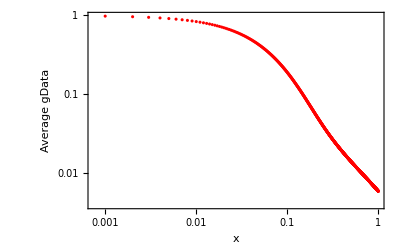

```mathematica
ListLogLogPlot[Transpose[{xaxis,xaxis averageGData1/theta}],Frame->True,FrameLabel->{"x","Average gData"},FrameStyle->Directive[Thickness[0.005],Black], PlotStyle->Red]
```

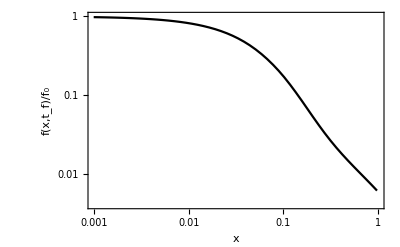

```mathematica
Data1s=Transpose@{xaxis,xaxis averageGData1/theta};
(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.001;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];
(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f/f^*"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];
a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},PlotStyle->{Black},Frame->True,FrameLabel->{"x","f(x,t_f)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotRange->{{0.001,1},{0.004,1}}];
a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_f)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.8"},PlotRange->{{0.001,1},{0.003,1}}(*, PlotMarkers->{"○",10}*), Joined->True];

(*Show both plots*)
Show[a1sInterpolated]
```

-Graphics-

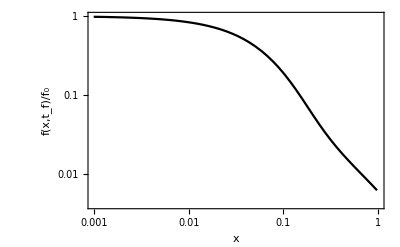

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.5;x0=1/(2 2 s h N1);
x1=NDSolveValue[{D[x2a[t],t]==h s*x2a[t]*(1-x2a[t]),x2a[0]==x0},x2a,{t,0,1000}];


N1= 1000;
(*  s= 0.1 0.5 *)
mu=10^-7;
L=99999;
theta=4N1 mu L;


averageGData={};
Tfix=Log[2 2 N1 s  ]/(h  s (1-h))+ (EulerGamma+ (2- 3 h)Log[h] + (3 h-1) Log[1-h])/(h  s (1-h));
G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,1000},{x,0,1}];
gData=Table[ G[x,Tfix]/(x*(1-x)),{x,0.001,0.999,0.001}];
AppendTo[averageGData,gData];
averageGData1=Mean[averageGData];

xaxis=Table[x,{x,0.001,.999,0.001}];

ListLogLogPlot[Transpose[{xaxis,averageGData1}],Frame->True,FrameLabel->{"x","Average gData"},FrameStyle->Directive[Thickness[0.005],Black], PlotStyle->Red]


Data1s=Transpose@{xaxis,xaxis averageGData1/theta};
(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.001;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];
(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f/f^*"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];
a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},PlotStyle->{Black},Frame->True,FrameLabel->{"x","f(x,t_f)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotRange->{{0.001,1},{0.004,1}}];
a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_f)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.8"},PlotRange->{{0.001,1},{0.003,1}}(*, PlotMarkers->{"○",10}*), Joined->True];

(*Show both plots*)
Show[a1sInterpolated]
```

```mathematica
Quit[]
```

InputStream[…]

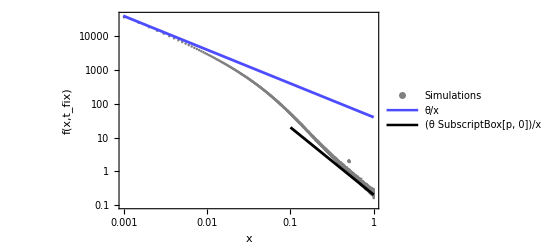

```mathematica
N1=1000;
mu=10^-7;
L=100000;
h=0.5;

sa=(h + (1-h) f);

theta=4 N1 mu L; (* theta= 2 N mu *)
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/hard_sweep/average_data_sweep_Ns_100.txt"]
datas1s=ReadList[s1s,{Number,Number}];

Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];


Data1s=Transpose@{x11s,x21s};

a1s=ListLogLogPlot[{Data1s}, Frame->True, FrameLabel->{"x","f(x,t_fix)"},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Gray,Red,Magenta,Brown},PlotLegends->{"Simulations", "Diffusion"},PlotRange->{{ 0.001,1},{0.1,40000}}];


a2s=LogLogPlot[theta/(x),{x,0,1},PlotStyle->{Lighter[Blue,0.3],Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\), \(x\)]\)",Medium]}];

a3s=LogLogPlot[theta /(2 1000 2 0.5 0.1 x^2),{x,0.1,1},PlotStyle->{Black,Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\\\ 
   \*SubscriptBox[\(p\), \(0\)]\), SuperscriptBox[\(x\), \(2\)]]\)",Medium]}];

Show[a1s,a2s,a3s]
```

```mathematica
Data1s=Transpose@{x11s,x11s x21s/theta};
(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.001;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.8"},PlotRange->{{0.001,1},{0.003,1}},PlotMarkers->"○"];

(*Show both plots*)
Show[a1sCombined]
```

-Graphics-

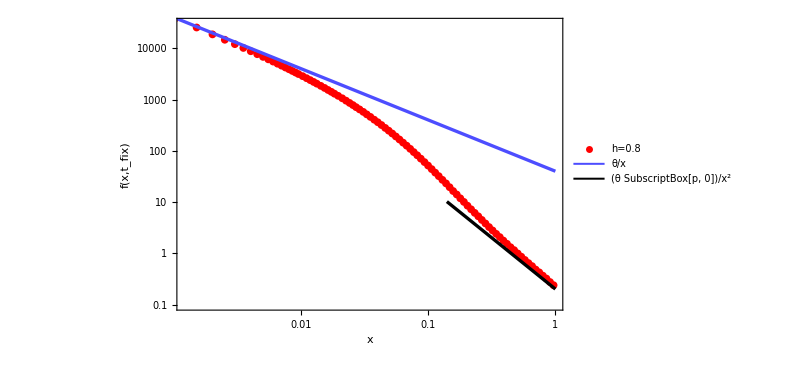

```mathematica
Data1s=Transpose@{x11s, x21s};
(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.001;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium,FontSize->16],PlotStyle->{Red},PlotLegends->{"h=0.8"},PlotRange->{{0.0012,1},{0.1,3 10^4}},PlotMarkers->{"●",8}];
a2s=LogLogPlot[theta/x,{x,0,1},PlotStyle->{Lighter[Blue,0.3],Thickness[0.004]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\), \(x\)]\)",Large]}];

a3s=LogLogPlot[theta/(200 x^2),{x,0.14,1},PlotStyle->{Black,Thickness[0.004]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\\\ 
   \*SubscriptBox[\(p\), \(0\)]\), SuperscriptBox[\(x\), \(2\)]]\)",Large]}];
(*Show both plots*)
Show[a1sCombined,a2s,a3s]
```

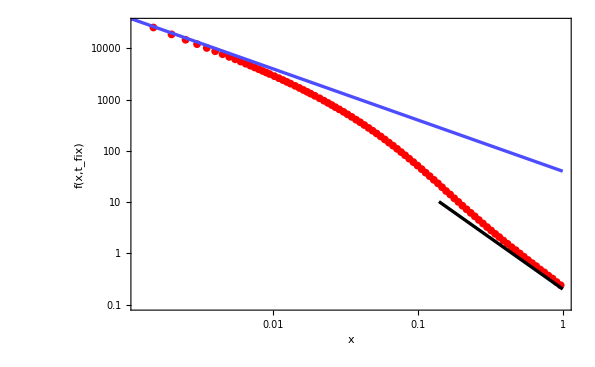
```mathematica
a1=-Graphics-;
```

```mathematica
PlotMarkers["★"]
```

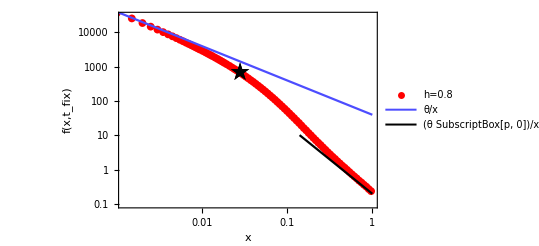

```mathematica
Show[a1sCombined,a2s,a3s,ListLogLogPlot[{{0.028,700}},PlotMarkers->{"★",20},(*Adjust the size as needed*)PlotStyle->{Black},(*You can choose the color of the star*)PlotRange->All]]
```

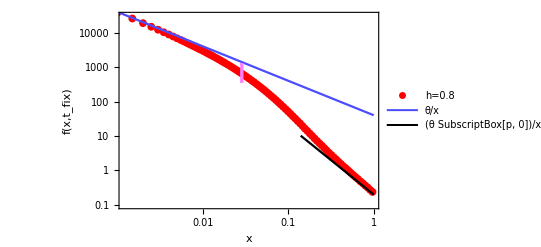

-Graphics-

```mathematica
Show[a1sCombined,a2s,a3s,Epilog->{Lighter[Magenta,0.5],Thickness[0.006],Line[{{Log10[0.00028],Log10[0.7 1000000]},{Log10[0.00028],Log10[1.5*10^7]}}]}]
```

```mathematica
a1=-Graphics-;
```

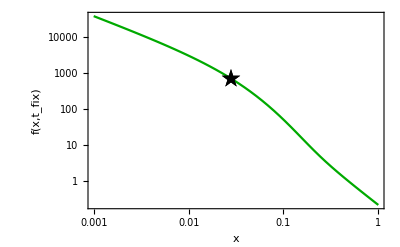
```mathematica
a2=-Graphics-;
```

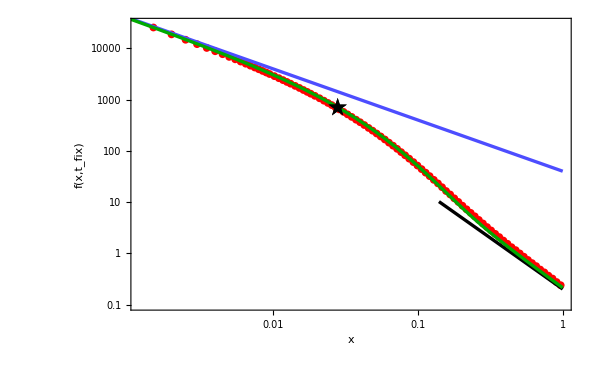

```mathematica
Show[a1,a2]
```

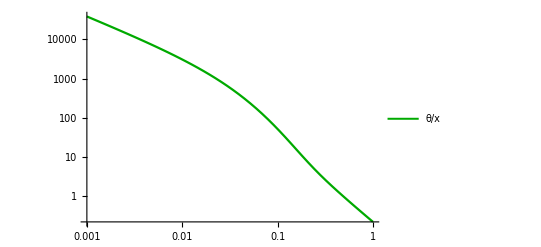

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.5;x0=1/(2 2 s h N1);
x1=NDSolveValue[{D[x2a[t],t]== s*x2a[t]*(1-x2a[t]) (x2a[t] + h (1- 2  x2a[t] )),x2a[0]==x0},x2a,{t,0,3000}];


pt=x1[220.18362426267285];
(*pt=x1[1290.3240671352746];*)
p0=1/(2 N1  2 s h);
a= Abs[h pt Log[1-pt]/(1-h)];
w[x_]:=16 N1 s h x pt;

green=LogLogPlot[((theta pt)/x + theta  pt/x( ⅇ^((-w[x])/(4 a))/(4 a^2)(w[x]  Log[(4 a^2)/w[x]] +w[x] ExpIntegralEi[w[x]/(4 a)] + 4a) + ⅇ^((-w[x])/(4 a)) -1/a-1)), {x,0.001,1}, PlotStyle->{Darker[
Green],Thickness[0.004]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\), \(x\)]\)",Large]}]
```

```mathematica
pt
```

0.996718

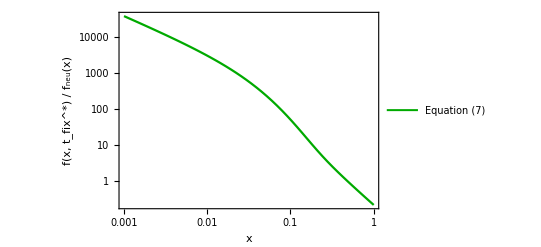

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.5;x0=1/(2 2 s h N1);
x1=NDSolveValue[{D[x2a[t],t]== s*x2a[t]*(1-x2a[t]) (x2a[t] + h (1- 2  x2a[t] )),x2a[0]==x0},x2a,{t,0,3000}];


pt=x1[220.18362426267285];
(*pt=x1[1290.3240671352746];*)
p0=1/(2 N1  2 s h);
a= Abs[h pt Log[1-pt]/(1-h)];
w[x_]:=16 N1 s h x pt;

LogLogPlot[((theta pt)/x + theta  pt/x( ⅇ^((-w[x])/(4 a))/(4 a^2)(w[x]  Log[(4 a^2)/w[x]] +w[x] ExpIntegralEi[w[x]/(4 a)] + 4a) + ⅇ^((-w[x])/(4 a)) -1/a-1)), {x,0.001,1}, PlotStyle->{Darker[
Green],Thickness[0.004]},PlotLegends->{"Equation (7)",Large}, Frame->True, (*FrameLabel->{"x","f(x,t_fix)"},*)FrameLabel->{Style["x",Italic],Row[{Style["f(",Italic],Style["x",Italic],Style[", ",Italic],Style[Superscript[Subscript["t","fix"],"*"],Italic],Style[") / ",Italic],Style[Subscript["f","neu"],Italic],Style["(x)",Italic]}]},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium,FontSize->16]]
```

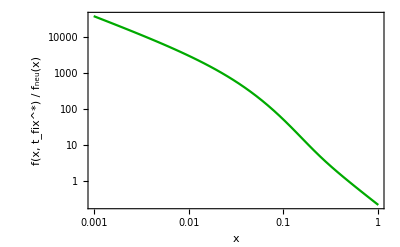
```mathematica
a2=-Graphics-;
```

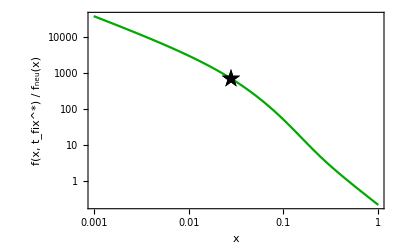

```mathematica
Show[a2,ListLogLogPlot[{{0.028,700}},PlotMarkers->{"★",20},(*Adjust the size as needed*)PlotStyle->{Black},(*You can choose the color of the star*)PlotRange->All]]
```

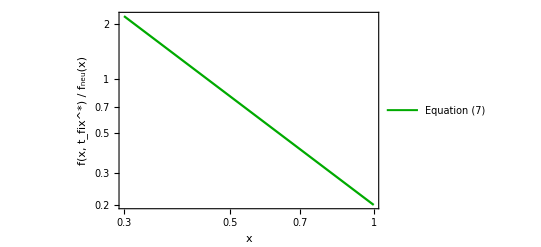

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.5;x0=1/(2 2 s h N1);
x1=NDSolveValue[{D[x2a[t],t]== s*x2a[t]*(1-x2a[t]) (x2a[t] + h (1- 2  x2a[t] )),x2a[0]==x0},x2a,{t,0,3000}];


pt=x1[220.18362426267285];
(*pt=x1[1290.3240671352746];*)
p0=1/(2 N1  2 s h);
a= Abs[h pt Log[1-pt]/(1-h)];
w[x_]:=16 N1 s h x pt;

LogLogPlot[(theta p0/x^2), {x,0.3,1}, PlotStyle->{Darker[
Green],Thickness[0.004]},PlotLegends->{"Equation (7)",Large}, Frame->True, (*FrameLabel->{"x","f(x,t_fix)"},*)FrameLabel->{Style["x",Italic],Row[{Style["f(",Italic],Style["x",Italic],Style[", ",Italic],Style[Superscript[Subscript["t","fix"],"*"],Italic],Style[") / ",Italic],Style[Subscript["f","neu"],Italic],Style["(x)",Italic]}]},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium,FontSize->16]]
```

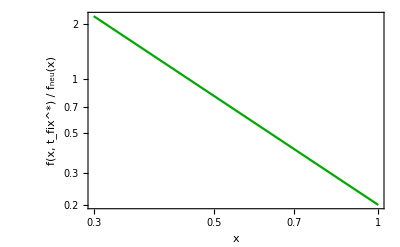
```mathematica
a1=-Graphics-;
```

```mathematica
a2=-Graphics-;
```

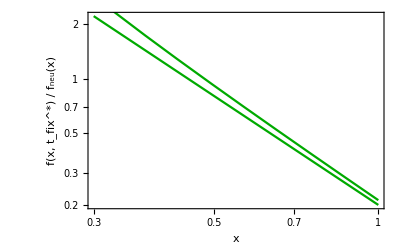

```mathematica
Show[a1,a2]
```

### simulations Ns=100, Data1s not figure 1

InputStream[…]

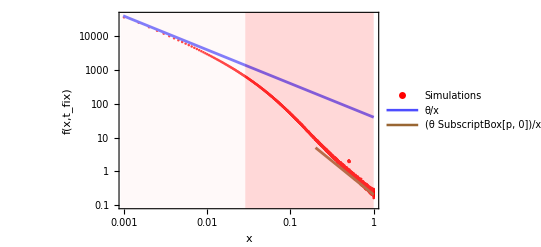

```mathematica
N1=1000;
mu=10^-7;
L=100000;
h=0.5;
sa=(h + (1-h) f);

theta=4 N1 mu L; (* theta= 2 N mu *)
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/hard_sweep/average_data_sweep_Ns_100.txt"]
datas1s=ReadList[s1s,{Number,Number}];

Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];


Data1s=Transpose@{x11s,x21s};

a1s=ListLogLogPlot[{Data1s}, Frame->True, FrameLabel->{"x","f(x,t_fix)"},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red,Magenta,Brown},PlotLegends->{"Simulations", "Diffusion"},PlotRange->{{ 0.001,1},{0.1,40000}},Epilog->{{Opacity[0.3,LightPink],Rectangle[{Log[10,0.0000001],Log[10,0.0000003]},{Log[10,0.00028],Log[10,10^12]}]},{Opacity[0.3,Pink],Rectangle[{Log[10,0.00028],Log[10,0.0000003]},{Log[10,1],Log[10,10^12]}]}}];


a2s=LogLogPlot[theta/(x),{x,0,1},PlotStyle->{Lighter[Blue,0.3],Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\), \(x\)]\)",Medium]}];

a3s=LogLogPlot[theta /(2 1000 2 0.5 0.1 x^2),{x,0.2,1},PlotStyle->{Brown,Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\\\ 
   \*SubscriptBox[\(p\), \(0\)]\), SuperscriptBox[\(x\), \(2\)]]\)",Medium]}];

Show[a1s,a2s,a3s]
```

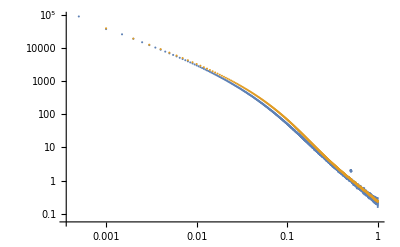

InputStream[…]

-Graphics-

```mathematica
ListLogLogPlot[{Data1s,datadiffusion}]
```

```mathematica
Data1s=Transpose@{x11s,x11s x21s/theta};
(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.001;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Gray},PlotLegends->{"h=0.8"},PlotRange->{{0.001,1},{0.003,1}}, PlotMarkers->"○",Epilog->{{Opacity[0.3,Pink],Rectangle[{Log[10,0.0000001],Log[10,0.0000003]},{Log[10,0.00028],Log[10,1]}]},{Opacity[0.3,LightPink],Rectangle[{Log[10,0.00028],Log[10,0.0000003]},{Log[10,1],Log[10,1]}]}}];

(*Show both plots*)
Show[a1sCombined]
```

-Graphics-

```mathematica
Log[10,0.178]
```

-0.74958

-Graphics-

```mathematica
a1=-Graphics-;
```

```mathematica
a1=-Graphics-;
```

```mathematica
a2=-Graphics-;
```

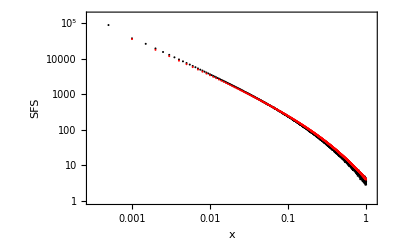
```mathematica
a1=-Graphics-;
```

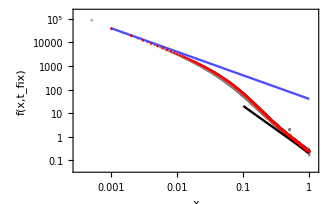
```mathematica
a2=-Graphics-;
```

```mathematica
Show[a1,a2]
```

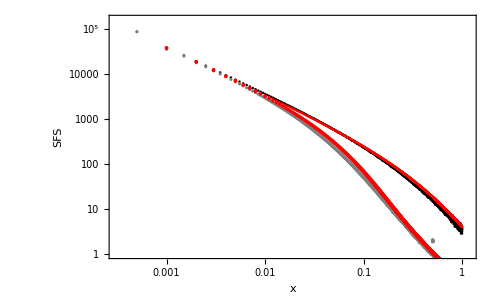

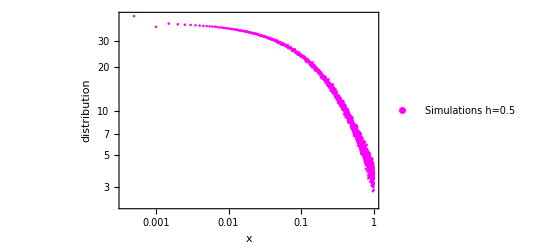

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L; (* theta= 2 N mu *)
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/N_1000_s_0.01_h_0.5/dist_txt_files/Ns_10_sfs.txt"];
(*e1:1 t:5000000 and theta is 0.100000 *)
datas1s=ReadList[s1s,{Number,Number}];

Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];


Data1s=Transpose@{x11s,x11s x21s};

a1s=ListLogLogPlot[{Data1s}, Frame->True, FrameLabel->{"x","distribution"},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Magenta,Magenta,Brown},PlotLegends->{"Simulations h=0.5"}];
a2s=LogLogPlot[theta/x,{x,0,1},Frame->True, FrameLabel->{"x","distribution"},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"theta/x"}];

Show[a1s]
```

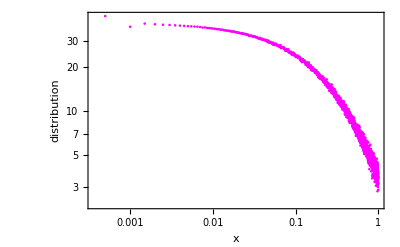
```mathematica
a1=-Graphics-;
```

InputStream[…]

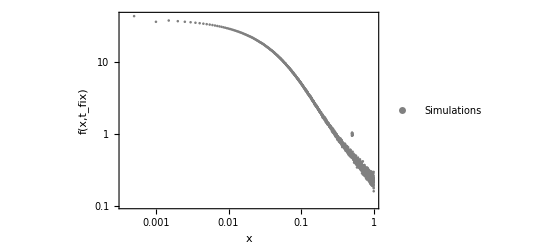

```mathematica
N1=1000;
mu=10^-7;
L=100000;
h=0.5;
sa=(h + (1-h) f);

theta=4 N1 mu L; (* theta= 2 N mu *)
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/hard_sweep/average_data_sweep_Ns_100.txt"]
datas1s=ReadList[s1s,{Number,Number}];

Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];


Data1s=Transpose@{x11s,x11s x21s};

a1s=ListLogLogPlot[{Data1s}, Frame->True, FrameLabel->{"x","f(x,t_fix)"},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Gray,Red,Magenta,Brown},PlotLegends->{"Simulations", "Diffusion"}];


a2s=LogLogPlot[theta/(x),{x,0,1},PlotStyle->{Lighter[Blue,0.3],Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\), \(x\)]\)",Medium]}];

a3s=LogLogPlot[theta /(2 1000 2 0.5 0.1 x^2),{x,0.1,1},PlotStyle->{Black,Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\\\ 
   \*SubscriptBox[\(p\), \(0\)]\), SuperscriptBox[\(x\), \(2\)]]\)",Medium]}];

Show[a1s]
```

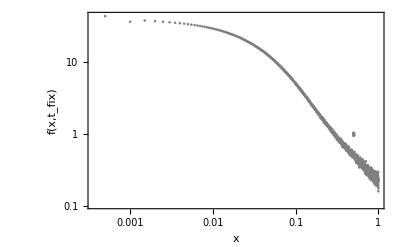
```mathematica
a2=-Graphics-;
```

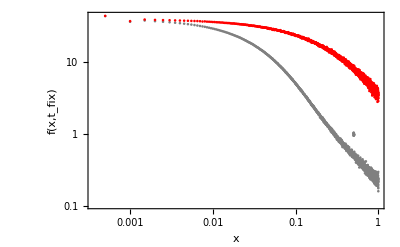

```mathematica
Show[a2,a1]
```

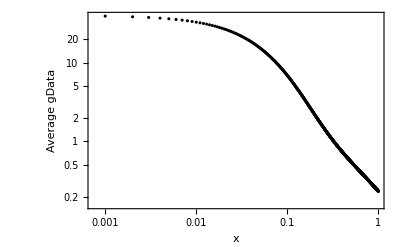

```mathematica
xaxis=Table[x,{x,0.001,.999,0.001}];

ListLogLogPlot[Transpose[{xaxis,xaxis averageGData1}],Frame->True,FrameLabel->{"x","Average gData"},FrameStyle->Directive[Thickness[0.005],Black], PlotStyle->Black]
```

```mathematica
a3=-Graphics-;
```

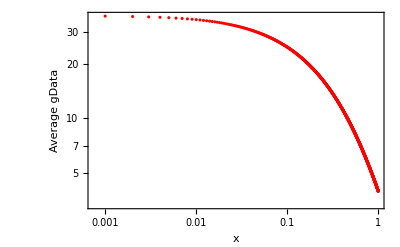

```mathematica
averageGData1=Mean[averageGData];

xaxis=Table[x,{x,0.001,.999,0.001}];

ListLogLogPlot[Transpose[{xaxis,xaxis averageGData1}],Frame->True,FrameLabel->{"x","Average gData"},FrameStyle->Directive[Thickness[0.005],Black], PlotStyle->Red]
```

```mathematica
a4=-Graphics-;
```

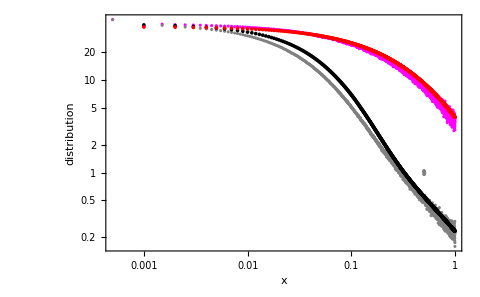

```mathematica
Show[a1,a2,a3,a4, PlotRange->All]
```

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
N1=1000;s=0.01;h=0.5;x0=1/(2 2 s h N1);
x1=NDSolveValue[{D[x2a[t],t]==h s*x2a[t]*(1-x2a[t]),x2a[0]==x0},x2a,{t,0,4500}];
```

```mathematica
Sum[Datatfix[[k,2]] k,{k,1,Length[Datatfix]}]
```

```mathematica
pt=x1[1290.32]
```

0.970891

```mathematica
x0 Abs[Log[1-pt]]
```

0.176835

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
N1=1000;s=0.1;h=0.5;x0=1/(2 2 s h N1);
x1=NDSolveValue[{D[x2a[t],t]==h s*x2a[t]*(1-x2a[t]),x2a[0]==x0},x2a,{t,0,4500}];
```

```mathematica
pt=x1[220.18362426267285]
```

0.996718

```mathematica
x0 Abs[Log[1-pt]]
```

0.0285959

## Ns = 50 diffusion

```mathematica
Quit[]
```

InputStream[…]

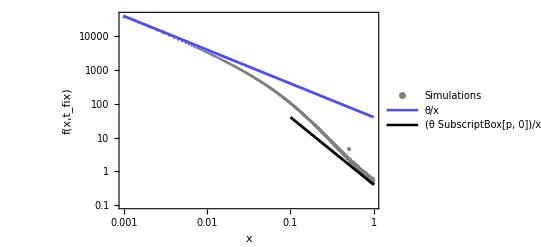

```mathematica
N1=1000;
mu=10^-7;
L=100000;
h=0.5;

sa=(h + (1-h) f);

theta=4 N1 mu L; (* theta= 2 N mu *)
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/hard_sweep/post_fix_Ns_50.txt"]
datas1s=ReadList[s1s,{Number,Number}];

Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];


Data1s=Transpose@{x11s,x21s};

a1s=ListLogLogPlot[{Data1s}, Frame->True, FrameLabel->{"x","f(x,t_fix)"},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Gray,Red,Magenta,Brown},PlotLegends->{"Simulations", "Diffusion"},PlotRange->{{ 0.001,1},{0.1,40000}}];


a2s=LogLogPlot[theta/(x),{x,0,1},PlotStyle->{Lighter[Blue,0.3],Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\), \(x\)]\)",Medium]}];

a3s=LogLogPlot[theta /(2 1000 2 0.5 0.05 x^2),{x,0.1,1},PlotStyle->{Black,Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\\\ 
   \*SubscriptBox[\(p\), \(0\)]\), SuperscriptBox[\(x\), \(2\)]]\)",Medium]}];

Show[a1s,a2s,a3s]
```

```mathematica
Quit[]
```

NIntegrate::nlim: t1 = t is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: t1 = t is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

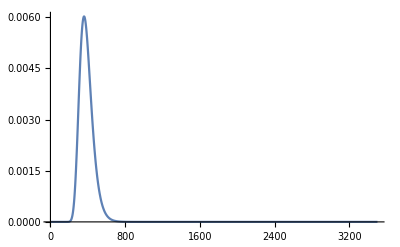

```mathematica
N1=1000;
s0=0.05;
h=0.5;
x0=1/(2 N1);


si[t_]:=s0;


taui[t_]:=taui[t]=h*NIntegrate[si[t1],{t1,0,t}];


pf1=2/(1+NIntegrate[Exp[-taui[t]],{t,0,Infinity}]);

C1=2 N1 pf1;


B[Te_]:=B[Te]=(2 N1)/NIntegrate[Exp[(1-h)/h taui[t]],{t,0,Te}];


pdfsd[Te_]:=pdfsd[Te]=(1/(2 N1)) C1 B[Te]^2 Exp[taui[Te]] 2 BesselK[0,2 Sqrt[B[Te] C1]];


pdfgenh[Te_]:=pdfgenh[Te]=h/(1-h) (C1 B[Te]^2)/(2 N1) Exp[(1-h)/h taui[Te]]*NIntegrate[q^(-(h/(1-h))) Exp[-B[Te] q] Exp[-C1 q^(-h/(1-h))],{q,0,Infinity},MaxRecursion->20];


a3=Plot[pdfgenh[t],{t,1,3500},PlotRange->All,PlotPoints->50]
```

```mathematica
timePoints=Range[1,3500,1];


weightValues=pdfgenh/@timePoints;

(*Combine time points and their corresponding weights into a single list*)
Datatfix=Transpose[{timePoints,weightValues}];
```

NIntegrate::nlim: t1 = t is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Sum[Datatfix[[k,2]] k,{k,1,Length[Datatfix]}]
```

385.885

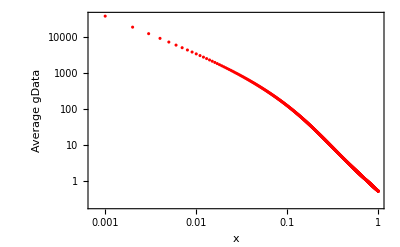

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
N1=1000;s=0.05;h=0.5;x0=1/(2 2 s h N1);
x1=NDSolveValue[{D[x2a[t],t]==h s*x2a[t]*(1-x2a[t]),x2a[0]==x0},x2a,{t,0,4500}];

averageGData={};

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,3500},{x,0,1}];
gData=Table[Sum[Datatfix[[j,2]] G[x,Datatfix[[j,1]]]/(x*(1-x)),{j,1,Length[Datatfix]}],{x,0.001,0.999,0.001}];
AppendTo[averageGData,gData];

averageGData1=Mean[averageGData];

xaxis=Table[x,{x,0.001,.999,0.001}];

ListLogLogPlot[Transpose[{xaxis,averageGData1}],Frame->True,FrameLabel->{"x","Average gData"},FrameStyle->Directive[Thickness[0.005],Black], PlotStyle->Red]
```

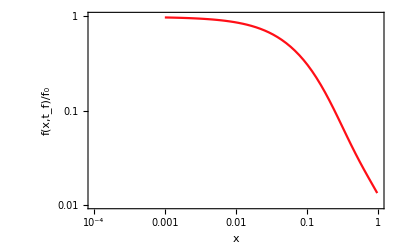

```mathematica
Data1s=Transpose[{xaxis,xaxis averageGData1/theta}];
(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.0001;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];
(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];
a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},PlotStyle->{RGBColor[1.,0.06,0.09] },Frame->True,FrameLabel->{"x","f(x,t_f)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotRange->{{0.0001,1},{0.01,1}}];
a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_f)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.8"},PlotRange->{{0.0001,1},{0.01,1}}(*, PlotMarkers->"●"*), Joined->{True, Dashed}];

(*Show both plots*)
Show[a1sInterpolated]
```

```mathematica
Quit[]
```

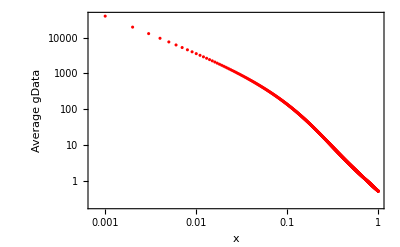

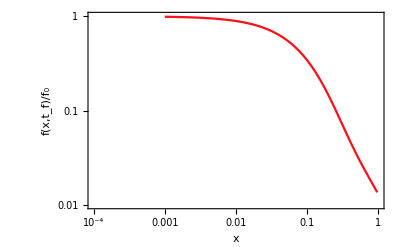

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L;
N1=1000;s=0.05;h=0.5;x0=1/(2 2 s h N1);
x1=NDSolveValue[{D[x2a[t],t]==h s*x2a[t]*(1-x2a[t]),x2a[0]==x0},x2a,{t,0,4500}];

Tfix=Log[2 2 N1 s  ]/(h  s (1-h))+ (EulerGamma+ (2- 3 h)Log[h] + (3 h-1) Log[1-h])/(h  s (1-h));
averageGData={};

G=NDSolveValue[{D[g[x,t],t]==(x (1-x))/(4 N1*x1[t]) D[g[x,t],x,x],g[1,t]==0,g[0,t]==x1[t] theta (1-Exp[-10000000 t]),g[x,0]==0},g,{t,0,3500},{x,0,1}];
gData=Table[ G[x,Tfix]/(x*(1-x)),{x,0.001,0.999,0.001}];
AppendTo[averageGData,gData];

averageGData1=Mean[averageGData];

xaxis=Table[x,{x,0.001,.999,0.001}];

ListLogLogPlot[Transpose[{xaxis,averageGData1}],Frame->True,FrameLabel->{"x","Average gData"},FrameStyle->Directive[Thickness[0.005],Black], PlotStyle->Red]

Data1s=Transpose[{xaxis,xaxis averageGData1/theta}];
(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.0001;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];
(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];
a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},PlotStyle->{RGBColor[1.,0.06,0.09] },Frame->True,FrameLabel->{"x","f(x,t_f)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotRange->{{0.0001,1},{0.01,1}}];
a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_f)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.8"},PlotRange->{{0.0001,1},{0.01,1}}(*, PlotMarkers->"●"*), Joined->{True, Dashed}];

(*Show both plots*)
Show[a1sInterpolated]
```

```mathematica
Text[Style["Ns=50",FontSize->14,FontSlant->"Italic",RGBColor[1.,0.06,0.09]]]
```

Ns=50

### Datatfix

```mathematica
Datatfix={{1,0.},{2,5.950509082251953*^-265},{3,1.0197819642623125*^-214},{4,1.2705023283868593*^-184},{5,5.5760189681749226*^-164},{6,1.1522001592661253*^-148},{7,1.059611228901847*^-136},{8,5.220547717856088*^-127},{9,6.120119420965296*^-119},{10,4.437692752429766*^-112},{11,3.7905300587297575*^-106},{12,5.996334594187069*^-101},{13,2.439687373604125*^-96},{14,3.261529706865674*^-92},{15,1.7271724811594246*^-88},{16,4.1905420683688476*^-85},{17,5.227002689918575*^-82},{18,3.676884209857814*^-79},{19,1.5728001660169622*^-76},{20,4.3529178759186874*^-74},{21,8.207728818318017*^-72},{22,1.101115409475718*^-69},{23,1.0903344306385658*^-67},{24,8.222730659733712*^-66},{25,4.8517759286269015*^-64},{26,2.292622255157713*^-62},{27,8.85350007245268*^-61},{28,2.8441286982423345*^-59},{29,7.719793185356623*^-58},{30,1.7949993356517437*^-56},{31,3.619345075892118*^-55},{32,6.397757384118833*^-54},{33,1.0011106565549944*^-52},{34,1.3988892617643993*^-51},{35,1.759315684377865*^-50},{36,2.00560261685395*^-49},{37,2.0858242109780372*^-48},{38,1.9905690165432987*^-47},{39,1.752475974525558*^-46},{40,1.43024302627503*^-45},{41,1.0868742509329757*^-44},{42,7.721994905492328*^-44},{43,5.148569034939529*^-43},{44,3.232571073670603*^-42},{45,1.9173274526276326*^-41},{46,1.0774796390233866*^-40},{47,5.752677897583946*^-40},{48,2.9253472765750313*^-39},{49,1.420207354557322*^-38},{50,6.596946612843216*^-38},{51,2.93789707529313*^-37},{52,1.2567799231448034*^-36},{53,5.173491339969966*^-36},{54,2.0527376406805494*^-35},{55,7.8629664730539*^-35},{56,2.9119168154624162*^-34},{57,1.0440202660260947*^-33},{58,3.628596775906807*^-33},{59,1.2240465313323779*^-32},{60,4.012230513090643*^-32},{61,1.2793040008130078*^-31},{62,3.9719768667951294*^-31},{63,1.202003307556008*^-30},{64,3.548697908715242*^-30},{65,1.0229967840745767*^-29},{66,2.881902558101911*^-29},{67,7.94006005343176*^-29},{68,2.141067731011299*^-28},{69,5.654651936487812*^-28},{70,1.4636661338689133*^-27},{71,3.715495174841928*^-27},{72,9.255388814631628*^-27},{73,2.263749602255508*^-26},{74,5.439497376307455*^-26},{75,1.2847418552669109*^-25},{76,2.98414224557105*^-25},{77,6.81992998672481*^-25},{78,1.534257251751335*^-24},{79,3.39912307577058*^-24},{80,7.419429492034749*^-24},{81,1.5961948102352741*^-23},{82,3.3859665207733074*^-23},{83,7.084734803960819*^-23},{84,1.4627329108889296*^-22},{85,2.980966926096287*^-22},{86,5.99852338110961*^-22},{87,1.1922449746850411*^-21},{88,2.341284723065696*^-21},{89,4.544009375550689*^-21},{90,8.7185529587561*^-21},{91,1.6542047369322004*^-20},{92,3.104480603491163*^-20},{93,5.764406431332703*^-20},{94,1.0592376912322236*^-19},{95,1.9266773342778314*^-19},{96,3.469774887143731*^-19},{97,6.188238118195553*^-19},{98,1.0931999125631937*^-18},{99,1.9133278726214917*^-18},{100,3.3183629433374566*^-18},{101,5.704108196632312*^-18},{102,9.719925476900352*^-18},{103,1.642210629655581*^-17},{104,2.751455469597451*^-17},{105,4.572339155618802*^-17},{106,7.537530214877718*^-17},{107,1.2328339321959052*^-16},{108,2.0009355957099748*^-16},{109,3.223152145521798*^-16},{110,5.153614262353275*^-16},{111,8.180669170568393*^-16},{112,1.2893541450146468*^-15},{113,2.017999453753693*^-15},{114,3.136841959724647*^-15},{115,4.843315706444988*^-15},{116,7.428920953728071*^-15},{117,1.1321248897411863*^-14},{118,1.7143520608017932*^-14},{119,2.5798404791713705*^-14},{120,3.858527958610083*^-14},{121,5.736327778719702*^-14},{122,8.477662515221142*^-14},{123,1.2456422579123674*^-13},{124,1.8198251222727984*^-13},{125,2.6437968574629587*^-13},{126,3.819711456651933*^-13},{127,5.488807767258589*^-13},{128,7.845315955288071*^-13},{129,1.1154929650294755*^-12},{130,1.5779212595826137*^-12},{131,2.2207677911461515*^-12},{132,3.109973497382138*^-12},{133,4.333926111221825*^-12},{134,6.010524310650543*^-12},{135,8.296277030357203*^-12},{136,1.1397967368797607*^-11},{137,1.5587532362154537*^-11},{138,2.122095570611857*^-11},{139,2.8762144010321188*^-11},{140,3.8812962940920206*^-11},{141,5.215085058439987*^-11},{142,6.977571015571927*^-11},{143,9.296811266231683*^-11},{144,1.2336122154067368*^-10},{145,1.6302930146190986*^-10},{146,2.1459616252122148*^-10},{147,2.8136744688525693*^-10},{148,3.674914313491616*^-10},{149,4.781535556048008*^-10},{150,6.198108994981789*^-10},{151,8.004736460808394*^-10},{152,1.0300416180025653*^-9},{153,1.3207050925705373*^-9},{154,1.6874203297155834*^-9},{155,2.148471584815197*^-9},{156,2.7261328252584042*^-9},{157,3.447443923994003*^-9},{158,4.3451177660982786*^-9},{159,5.458596453262606*^-9},{160,6.835276655434332*^-9},{161,8.531926074077718*^-9},{162,1.0616314985039856*^-8},{163,1.3169088871294891*^-8},{164,1.628591022993545*^-8},{165,2.0079899716851854*^-8},{166,2.4684408850307453*^-8},{167,3.0256158495577696*^-8},{168,3.697877928540686*^-8},{169,4.506679189854075*^-8},{170,5.4770066785179426*^-8},{171,6.63788043259105*^-8},{172,8.022907759870005*^-8},{173,9.670898080027112*^-8},{174,1.1626542689776473*^-7},{175,1.3941163822005674*^-7},{176,1.6673537338702216*^-7},{177,1.9890793317128848*^-7},{178,2.366939865439213*^-7},{179,2.809622562340254*^-7},{180,3.326971005470306*^-7},{181,3.93011025071619*^-7},{182,4.631581538723435*^-7},{183,5.445486851934841*^-7},{184,6.387643514374275*^-7},{185,7.475748969181853*^-7},{186,8.729555801481476*^-7},{187,1.0171056997861012*^-6},{188,1.1824681350554572*^-6},{189,1.3717498824495435*^-6},{190,1.5879435608204862*^-6},{191,1.8343498467199976*^-6},{192,2.1146007909778476*^-6},{193,2.432683956208445*^-6},{194,2.792967303210749*^-6},{195,3.200224742198759*^-6},{196,3.659662252561206*^-6},{197,4.1769444625089485*^-6},{198,4.758221567643802*^-6},{199,5.410156455295588*^-6},{200,6.139951889553536*^-6},{201,6.955377600396398*^-6},{202,7.864797109337064*^-6},{203,8.877194113678571*^-6},{204,0.000010002198241964331},{205,0.000011250109984925331},{206,0.000012631924596332553},{207,0.000014159354760233728},{208,0.000015844851799172605},{209,0.000017701625215580637},{210,0.000019743660339389127},{211,0.000021985733863112725},{212,0.000024443427043985392},{213,0.000027133136356522095},{214,0.000030072081383039037},{215,0.00003327830973630203},{216,0.00003677069881715221},{217,0.000040568954218806044},{218,0.000044693604603231054},{219,0.00004916599288640241},{220,0.00005400826358673248},{221,0.000059243346205618835},{222,0.00006489493452900884},{223,0.00007098746175767741},{224,0.00007754607139478766},{225,0.00008459658384523574},{226,0.00009216545869028733},{227,0.00010027975265321534},{228,0.00010896707326068764},{229,0.00011825552825822004},{230,0.00012817367084874478},{231,0.00013875044085317285},{232,0.0001500151019163771},{233,0.00016199717490711607},{234,0.00017472636768495775},{235,0.00018823250143113607},{236,0.0002025454337633637},{237,0.0002176949788726889},{238,0.00023371082497220506},{239,0.0002506224492599217},{240,0.00026845903082920976},{241,0.00028724936171120493},{242,0.0003070217564599845},{243,0.00032780396059872637},{244,0.0003496230582859305},{245,0.00037250537956601563},{246,0.0003964764075754603},{247,0.0004215606860804016},{248,0.0004477817277242041},{249,0.0004751619233640384},{250,0.0005037224528736499},{251,0.0005334831977653188},{252,0.0005644626561435395},{253,0.0005966778599164975},{254,0.0006301442953321805},{255,0.000664875826472229},{256,0.0007008846224374632},{257,0.0007381810884064269},{258,0.0007767738008771735},{259,0.0008166694473626311},{260,0.000857872770797719},{261,0.0009003865067735077},{262,0.0009442113986201699},{263,0.0009893460361274575},{264,0.001035786942031683},{265,0.0010835284824794462},{266,0.0011325628559280608},{267,0.0011828800757987513},{268,0.0012344679590602621},{269,0.0012873121207852163},{270,0.0013413959746966333},{271,0.0013967007396974138},{272,0.0014532054523513829},{273,0.001510886985260793},{274,0.0015697200712620923},{275,0.001629677333339532},{276,0.0016907293201346841},{277,0.0017528445469094872},{278,0.0018159895418009726},{279,0.0018801288971874535},{280,0.001945225325968867},{281,0.002011239722547956},{282,0.0020781312283394545},{283,0.002145857301180565},{284,0.0022143737895908102},{285,0.002283635009406626},{286,0.0023535938251528833},{287,0.002424201733847993},{288,0.0024954089518191714},{289,0.002567164504474533},{290,0.002639416317004655},{291,0.0027121113094339244},{292,0.0027851954912315284},{293,0.0028586140582774547},{294,0.002932311490745426},{295,0.0030062316517833775},{296,0.0030803178868358417},{297,0.003154513122373841},{298,0.003228759966596306},{299,0.0033030008070884746},{300,0.0033771779099120657},{301,0.003451233517025029},{302,0.0035251099427306277},{303,0.00359874966878174},{304,0.003672095437912187},{305,0.003745090345577914},{306,0.0038176779297022624},{307,0.0038898022582313455},{308,0.003961408014317845},{309,0.0040324405789637805},{310,0.004102846110965645},{311,0.004172571624017847},{312,0.0042415650608433764},{313,0.004309775364233437},{314,0.00437715254489058},{315,0.004443647745982614},{316,0.0045092133043272324},{317,0.0045738028081396395},{318,0.004637371151287686},{319,0.004699874584010996},{320,0.0047612707600721196},{321,0.004821518780319157},{322,0.0048805792326501625},{323,0.004938414228380189},{324,0.0049949874350220785},{325,0.005050264105501582},{326,0.005104211103836998},{327,0.005156796927321907},{328,0.005207991725258216},{329,0.005257767314294437},{330,0.005306097190431229},{331,0.005352956537763602},{332,0.005398322234034867},{333,0.0054421728530837845},{334,0.005484488664271312},{335,0.005525251628978482},{336,0.0055644453942710215},{337,0.005602055283830441},{338,0.0056380682862546},{339,0.005672473040833642},{340,0.005705259820909891},{341,0.005736420514932059},{342,0.005765948605316105},{343,0.00579383914522608},{344,0.0058200887333891395},{345,0.005844695487059617},{346,0.005867659013246887},{347,0.005888980378321684},{348,0.005908662076115013},{349,0.0059267079946229186},{350,0.00594312338142922},{351,0.005957914807957077},{352,0.005971090132658308},{353,0.005982658463248015},{354,0.0059926301180894615},{355,0.006001016586832273},{356,0.006007830490404353},{357,0.006013085540455522},{358,0.006016796498347766},{359,0.006018979133784673},{360,0.006019650183090295},{361,0.00601882730777492},{362,0.006016529051817958},{363,0.00601277480050079},{364,0.006007584738115384},{365,0.006000979806269991},{366,0.0059929817057181025},{367,0.005983612638025071},{368,0.00597289569862473},{369,0.005960854402177177},{370,0.005947512859432621},{371,0.005932895694165106},{372,0.005917028004055534},{373,0.005899935322166205},{374,0.005881643579049927},{375,0.005862179065533847},{376,0.005841568396214891},{377,0.005819838473700503},{378,0.005797016453625826},{379,0.005773129710475051},{380,0.005748205804232144},{381,0.005722272447883409},{382,0.005695357475791595},{383,0.005667488812958524},{384,0.005638694445191256},{385,0.005609002390183595},{386,0.005578440669523379},{387,0.00554703728163291},{388,0.005514820175648429},{389,0.0054818172262420545},{390,0.005448056209388008},{391,0.005413564779072886},{392,0.00537837044494806},{393,0.005342500550920805},{394,0.005305982254678801},{395,0.005268842508141726},{396,0.005231108038831677},{397,0.0051928053321534315},{398,0.00515396061457394},{399,0.005114599837689555},{400,0.005074748663168302},{401,0.005034432448553728},{402,0.004993676233915676},{403,0.004952504729332982},{404,0.004910942303191808},{405,0.004869012971283182},{406,0.0048267403866823115},{407,0.004784147830391913},{408,0.0047412582027313785},{409,0.004698094015452984},{410,0.004654677384566203},{411,0.004611030023850785},{412,0.004567173239039036},{413,0.004523127922647562},{414,0.004478914549438626},{415,0.004434553172491065},{416,0.00439006341986086},{417,0.004345464491811169},{418,0.004300775158591902},{419,0.004256013758748902},{420,0.004211198197942811},{421,0.004166345948257932},{422,0.0041214740479816065},{423,0.004076599101834572},{424,0.0040317372816332745},{425,0.003986904327365207},{426,0.00394211554865853},{427,0.0038973858266276766},{428,0.003852729616076863},{429,0.0038081609480436324},{430,0.003763693432665144},{431,0.003719340262350016},{432,0.0036751142152389943},{433,0.003631027658938158},{434,0.003587092554508542},{435,0.0035433204606966627},{436,0.003499722538390715},{437,0.003456309555287599},{438,0.0034130918907563385},{439,0.003370079540883957},{440,0.003327282123690055},{441,0.003284708884497066},{442,0.003242368701443241},{443,0.003200270091126064},{444,0.003158421221688348},{445,0.003116829892197737},{446,0.003075503574959128},{447,0.0030344493991963156},{448,0.0029936741382182823},{449,0.002953184305118052},{450,0.0029129860338807834},{451,0.00287308516382326},{452,0.002833487227536838},{453,0.0027941974572420663},{454,0.002755220791163744},{455,0.002716561879918556},{456,0.002678225092908079},{457,0.0026402145247099236},{458,0.002602534001460479},{459,0.002565187087222768},{460,0.002528177090333434},{461,0.0024915070697231006},{462,0.002455179841204665},{463,0.002419197983724415},{464,0.002383563845571129},{465,0.0023482795505385913},{466,0.002313347004037237},{467,0.002278767899150956},{468,0.0022445437226351994},{469,0.0022106757608529952},{470,0.0021771651056455275},{471,0.002144012660134274},{472,0.002111219144451898},{473,0.0020787851013993},{474,0.002046710902026466},{475,0.002014996751134916},{476,0.001983642692699822},{477,0.0019526486152099509},{478,0.0019220142569238703},{479,0.0018917392110409446},{480,0.0018618229307858863},{481,0.0018322647344057254},{482,0.0018030638100782566},{483,0.0017742192207311396},{484,0.0017457299087709677},{485,0.0017175947007218107},{486,0.0016898123117727681},{487,0.0016623813502342631},{488,0.001635300321902925},{489,0.0016085676343349546},{490,0.0015821816010280325},{491,0.0015561404455119025},{492,0.0015304423053478797},{493,0.001505085236037559},{494,0.0014800672148411595},{495,0.001455386144505949},{496,0.0014310398569053354},{497,0.0014070261165892053},{498,0.0013833426242462086},{499,0.0013599870200787405},{500,0.001336956887091414},{501,0.0013142497542938498},{502,0.0012918630998187425},{503,0.0012697943539561067},{504,0.0012480409021047058},{505,0.0012266000876417142},{506,0.00120546921471162},{507,0.001184645550935537},{508,0.0011641263300420034},{509,0.0011439087544204115},{510,0.0011239899975982628},{511,0.0011043672066434343},{512,0.0010850375044926487},{513,0.001065997992207397},{514,0.0010472457511585464},{515,0.0010287778451408757},{516,0.0010105913224188233},{517,0.0009926832177047033},{518,0.0009750505540706775},{519,0.0009576903447957631},{520,0.0009405995951491709},{521,0.0009237753041112393},{522,0.0009072144660320615},{523,0.0008909140722376127},{524,0.0008748711125589545},{525,0.0008590825768286965},{526,0.0008435454563030373},{527,0.0008282567450364232},{528,0.0008132134412014654},{529,0.0007984125483566146},{530,0.0007838510766627924},{531,0.0007695260440502427},{532,0.0007554344773367849},{533,0.0007415734132996325},{534,0.000727939899696514},{535,0.0007145309962500572},{536,0.0007013437755810911},{537,0.0006883753241022284},{538,0.0006756227428809077},{539,0.0006630831483940341},{540,0.0006507536734106763},{541,0.0006386314676155603},{542,0.0006267136983601391},{543,0.0006149975513116316},{544,0.0006034802310779471},{545,0.0005921589617984564},{546,0.0005810309877016682},{547,0.0005700935736307373},{548,0.0005593440055378174},{549,0.0005487795909481852},{550,0.0005383976593950613},{551,0.0005281955628260637},{552,0.0005181706759821739},{553,0.0005083203967501021},{554,0.0004986421464888944},{555,0.0004891333703316389},{556,0.0004797915374630751},{557,0.00047061414137391177},{558,0.00046159870009265},{559,0.0004527427563956431},{560,0.00044404387799619385},{561,0.0004354996577133719},{562,0.0004271077136213026},{563,0.00041886568917962747},{564,0.00041077125334580423},{565,0.0004028221006699429},{566,0.0003950159513728212},{567,0.000387350551407722},{568,0.00037982367250951796},{569,0.0003724331122136173},{570,0.00036517669389301335},{571,0.00035805226674748346},{572,0.0003510577057970624},{573,0.0003441909118592817},{574,0.0003374498115142444},{575,0.00033083235705804636},{576,0.0003243365264486532},{577,0.00031796032318808003},{578,0.00031170177643782213},{579,0.0003055589405751268},{580,0.00029952989543806884},{581,0.0002936127460498697},{582,0.00028780562253786547},{583,0.0002821066800156081},{584,0.0002765140984318757},{585,0.000271026082463688},{586,0.00026564086135175667},{587,0.00026035668875372495},{588,0.0002551718425891507},{589,0.00025008462487200426},{590,0.00024509336154658753},{591,0.00024019640231160436},{592,0.00023539212044205562},{593,0.00023067891261089674},{594,0.00022605519868108682},{595,0.00022151942154678673},{596,0.00021707004691595352},{597,0.00021270556311733558},{598,0.00020842448089865631},{599,0.00020422533322781407},{600,0.00020010667506193823},{601,0.00019606708317095774},{602,0.00019210515590452427},{603,0.00018821951298238955},{604,0.00018440879527815483},{605,0.0001806716646013325},{606,0.0001770068034779073},{607,0.00017341291492958133},{608,0.00016988872225186775},{609,0.00016643296879120817},{610,0.00016304441772127334},{611,0.00015972185182391757},{612,0.00015646407324089326},{613,0.0001532699032863729},{614,0.00015013818219507247},{615,0.00014706776890780805},{616,0.00014405754082991444},{617,0.0001411063936258894},{618,0.0001382132409835492},{619,0.00013537701439115057},{620,0.00013259666291298974},{621,0.00012987115296556268},{622,0.00012719946809437797},{623,0.00012458060875151751},{624,0.00012201359207403219},{625,0.00011949745166324691},{626,0.00011703123736506236},{627,0.00011461401505132047},{628,0.00011224486640230877},{629,0.00010992288869717536},{630,0.00010764719456963834},{631,0.00010541691184128456},{632,0.00010323118327845363},{633,0.00010108916638508421},{634,0.0000989900331950509},{635,0.00009693297006649493},{636,0.00009491717747424668},{637,0.00009294186980516079},{638,0.00009100627515510728},{639,0.00008910963512768622},{640,0.00008725120463450915},{641,0.00008543025169762916},{642,0.00008364605725324515},{643,0.00008189791495760072},{644,0.00008018513099467814},{645,0.00007850702388514462},{646,0.00007686292429875575},{647,0.00007525217486684537},{648,0.00007367412999696367},{649,0.00007212815569121549},{650,0.00007061362936473075},{651,0.00006912993966659765},{652,0.00006767648630280496},{653,0.00006625267986159403},{654,0.00006485794163978395},{655,0.00006349170347206221},{656,0.00006215340756179457},{657,0.00006084250631512494},{658,0.000059558462171063344},{659,0.00005830074744539236},{660,0.000057068844165033235},{661,0.00005586224391000096},{662,0.000054680447656267495},{663,0.0000535229656206137},{664,0.00005238931710746373},{665,0.00005127903036993264},{666,0.00005019164241039913},{667,0.00004912669890075094},{668,0.0000480837540244523},{669,0.000047062370284644314},{670,0.00004606211840536017},{671,0.00004508257718106777},{672,0.00004412333333909993},{673,0.000043183981403993394},{674,0.00004226412356372171},{675,0.00004136336953780858},{676,0.00004048133644731335},{677,0.000039617648686670464},{678,0.00003877193779737368},{679,0.00003794384234348732},{680,0.000037133007788972157},{681,0.00003633908637681196},{682,0.00003556173700992244},{683,0.00003480062513383156},{684,0.00003405542262111109},{685,0.00003332580767097776},{686,0.0000326114646300285},{687,0.000031912084016148634},{688,0.00003122736227548296},{689,0.00003055700174254798},{690,0.000029900710521410393},{691,0.00002925820238193385},{692,0.00002862919665764649},{693,0.00002801341814521085},{694,0.000027410597005478585},{695,0.000026820468666113853},{696,0.00002624277372576551},{697,0.000025677257859772195},{698,0.000025123671727383},{699,0.000024581770880472606},{700,0.000024051315673737764},{701,0.00002353207117635394},{702,0.00002302380708507477},{703,0.000022526297638758652},{704,0.000022039321549394584},{705,0.00002156266184395936},{706,0.00002109610593404712},{707,0.000020639445384984817},{708,0.00002019247591377809},{709,0.000019754997291273023},{710,0.00001932681327706395},{711,0.000018907731533888085},{712,0.000018497563559634373},{713,0.00001809612461406327},{714,0.000017703233647848593},{715,0.00001731871323283578},{716,0.000016942389493497443},{717,0.000016574092039572074},{718,0.000016213653899866236},{719,0.000015860911457205253},{720,0.0000155157043845167},{721,0.000015177875582027825},{722,0.000014847271115562579},{723,0.000014523740155921924},{724,0.000014207134934421903},{725,0.000013897310608932325},{726,0.000013594125357328829},{727,0.00001329744017012635},{728,0.000013007118870495882},{729,0.0000127230280447182},{730,0.00001244503698870368},{731,0.00001217301765547072},{732,0.000011906844603568347},{733,0.0000116463949464275},{734,0.00001139154830262765},{735,0.000011142186747063513},{736,0.000010898194762997621},{737,0.000010659459194985212},{738,0.000010425869202657139},{739,0.000010197316215347209},{740,9.973693887550041*^-6},{741,9.754898055196607*^-6},{742,9.54082669273353*^-6},{743,9.331379870993481*^-6},{744,9.126459715843715*^-6},{745,8.925970382340025*^-6},{746,8.729817941189698*^-6},{747,8.537910487064516*^-6},{748,8.350157952827902*^-6},{749,8.166472145588074*^-6},{750,7.98676669501062*^-6},{751,7.810957017063415*^-6},{752,7.63896027844209*^-6},{753,7.470695361663599*^-6},{754,7.306082830817382*^-6},{755,7.145044897962231*^-6},{756,6.987505390158485*^-6},{757,6.833389717123932*^-6},{758,6.682624839503121*^-6},{759,6.535139237739603*^-6},{760,6.390862881540017*^-6},{761,6.249727199920577*^-6},{762,6.1116650518250734*^-6},{763,5.976610697304681*^-6},{764,5.844499769250058*^-6},{765,5.715269245665157*^-6},{766,5.58885743447599*^-6},{767,5.465203886851982*^-6},{768,5.34424949106707*^-6},{769,5.225936326831625*^-6},{770,5.1102077001454815*^-6},{771,4.997008106628024*^-6},{772,4.8862832073281176*^-6},{773,4.777979805003498*^-6},{774,4.672045820861699*^-6},{775,4.5684302717535006*^-6},{776,4.467083247811291*^-6},{777,4.367955890523822*^-6},{778,4.271000371239801*^-6},{779,4.176169870092208*^-6},{780,4.083418555335761*^-6},{781,3.992701563090089*^-6},{782,3.9039749774808525*^-6},{783,3.8171958111719416*^-6},{784,3.7323219862660943*^-6},{785,3.6493123156580796*^-6},{786,3.5681264846033493*^-6},{787,3.488725032817526*^-6},{788,3.4110693367821007*^-6},{789,3.3351215917218967*^-6},{790,3.2608447989093643*^-6},{791,3.188202740434137*^-6},{792,3.117159971628766*^-6},{793,3.0476818007827183*^-6},{794,2.979734274393185*^-6},{795,2.9132841618671976*^-6},{796,2.848298940483124*^-6},{797,2.7847467807455305*^-6},{798,2.722596531941517*^-6},{799,2.661817708032359*^-6},{800,2.6023804738194032*^-6},{801,2.5442556313879216*^-6},{802,2.487414606823698*^-6},{803,2.431829437197206*^-6},{804,2.377472757810128*^-6},{805,2.32431778969934*^-6},{806,2.2723383273932296*^-6},{807,2.221508726915698*^-6},{808,2.1718038940329894*^-6},{809,2.1231992727385905*^-6},{810,2.0756708339717834*^-6},{811,2.0291950645651568*^-6},{812,1.9837489564167215*^-6},{813,1.9393099958823336*^-6},{814,1.8958561533839878*^-6},{815,1.8533658732299744*^-6},{816,1.8118180636426114*^-6},{817,1.7711920869895572*^-6},{818,1.7314677502148287*^-6},{819,1.692625295465407*^-6},{820,1.6546453909098528*^-6},{821,1.6175091217449133*^-6},{822,1.5811979813866426*^-6},{823,1.5456938628422875*^-6},{824,1.5109790502593812*^-6},{825,1.4770362106486424*^-6},{826,1.4438483857771226*^-6},{827,1.4113989842283593*^-6},{828,1.3796717736261434*^-6},{829,1.3486508730186776*^-6},{830,1.3183207454200029*^-6},{831,1.2886661905054726*^-6},{832,1.2596723374583108*^-6},{833,1.23132463796416*^-6},{834,1.203608859350723*^-6},{835,1.1765110778696268*^-6},{836,1.1500176721175529*^-6},{837,1.1241153165940143*^-6},{838,1.0987909753928985*^-6},{839,1.0740318960251631*^-6},{840,1.0498256033700927*^-6},{841,1.026159893752399*^-6},{842,1.003022829142822*^-6},{843,9.8040273147956*^-7},{844,9.582881771082468*^-7},{845,9.366679913379739*^-7},{846,9.155312431110812*^-7},{847,8.948672397844022*^-7},{848,8.746655220196809*^-7},{849,8.549158587810005*^-7},{850,8.356082424370038*^-7},{851,8.167328839657978*^-7},{852,7.98280208260496*^-7},{853,7.802408495332677*^-7},{854,7.626056468159961*^-7},{855,7.453656395554667*^-7},{856,7.285120633012471*^-7},{857,7.120363454843285*^-7},{858,6.95930101284672*^-7},{859,6.801851295858648*^-7},{860,6.647934090150705*^-7},{861,6.49747094066557*^-7},{862,6.350385113070951*^-7},{863,6.206601556614926*^-7},{864,6.066046867766988*^-7},{865,5.928649254627913*^-7},{866,5.794338502093212*^-7},{867,5.663045937754255*^-7},{868,5.534704398522044*^-7},{869,5.40924819795882*^-7},{870,5.286613094315775*^-7},{871,5.166736259179721*^-7},{872,5.049556246931006*^-7},{873,4.935012964701795*^-7},{874,4.823047643048219*^-7},{875,4.7136028072560153*^-7},{876,4.606622249144229*^-7},{877,4.5020509996745394*^-7},{878,4.399835301960179*^-7},{879,4.299922584932589*^-7},{880,4.2022614375551907*^-7},{881,4.1068015835878316*^-7},{882,4.01349383462507*^-7},{883,3.9222901772523887*^-7},{884,3.833143526743936*^-7},{885,3.746007926566498*^-7},{886,3.660838414403803*^-7},{887,3.577591022255738*^-7},{888,3.4962227547477136*^-7},{889,3.416691567904804*^-7},{890,3.338956348381192*^-7},{891,3.262976893135371*^-7},{892,3.188713889541563*^-7},{893,3.116128895928444*^-7},{894,3.0451843225359876*^-7},{895,2.9758434128817847*^-7},{896,2.9080702255282457*^-7},{897,2.841829616242025*^-7},{898,2.777087220537761*^-7},{899,2.7138094365976965*^-7},{900,2.6519634085594424*^-7},{901,2.5915170101641716*^-7},{902,2.532438828757358*^-7},{903,2.4746981496350246*^-7},{904,2.4182649407277673*^-7},{905,2.3631098376157285*^-7},{906,2.3092041288674078*^-7},{907,2.256519741695358*^-7},{908,2.2050292279223342*^-7},{909,2.1547057502508637*^-7},{910,2.105523068830337*^-7},{911,2.0574555281148452*^-7},{912,2.0104780440058384*^-7},{913,1.9645660912735356*^-7},{914,1.9196956912510443*^-7},{915,1.8758433997955226*^-7},{916,1.8329862955106072*^-7},{917,1.7911019682245837*^-7},{918,1.7501685077188603*^-7},{919,1.7101644927013452*^-7},{920,1.6710689800196249*^-7},{921,1.6328614941086885*^-7},{922,1.5955220166682702*^-7},{923,1.559030976564909*^-7},{924,1.5233692399538707*^-7},{925,1.4885181006162875*^-7},{926,1.4544592705068808*^-7},{927,1.4211748705077152*^-7},{928,1.388647421383688*^-7},{929,1.3568598349352968*^-7},{930,1.3257954053445678*^-7},{931,1.2954378007098965*^-7},{932,1.2657710547658472*^-7},{933,1.236779558783879*^-7},{934,1.2084480536500937*^-7},{935,1.1807616221162889*^-7},{936,1.1537056812204832*^-7},{937,1.1272659748733404*^-7},{938,1.1014285666069131*^-7},{939,1.0761798324821335*^-7},{940,1.051506454151781*^-7},{941,1.0273954120754142*^-7},{942,1.0038339788830921*^-7},{943,9.808097128846544*^-8},{944,9.583104517213643*^-8},{945,9.36324306156953*^-8},{946,9.148396540049027*^-8},{947,8.938451341891868*^-8},{948,8.733296409354363*^-8},{949,8.532823180897991*^-8},{950,8.336925535627455*^-8},{951,8.145499738948936*^-8},{952,7.958444389427821*^-8},{953,7.775660366810891*^-8},{954,7.597050781196822*^-8},{955,7.422520923324318*^-8},{956,7.251978215955588*^-8},{957,7.085332166331708*^-8},{958,6.922494319675324*^-8},{959,6.763378213719399*^-8},{960,6.607899334238531*^-8},{961,6.455975071561606*^-8},{962,6.307524678044514*^-8},{963,6.16246922648162*^-8},{964,6.020731569436003*^-8},{965,5.882236299468102*^-8},{966,5.74690971024332*^-8},{967,5.6146797585141965*^-8},{968,5.485476026880641*^-8},{969,5.3592296874841287*^-8},{970,5.2358734664066803*^-8},{971,5.115341608902593*^-8},{972,4.997569845391783*^-8},{973,4.8824953582061954*^-8},{974,4.7700567490731485*^-8},{975,4.660194007318869*^-8},{976,4.552848478777183*^-8},{977,4.447962835387184*^-8},{978,4.3454810454651995*^-8},{979,4.245348344298554*^-8},{980,4.147511207203476*^-8},{981,4.051917319388485*^-8},{982,3.958515547076604*^-8},{983,3.86725592266419*^-8},{984,3.778089601970819*^-8},{985,3.6909688491865254*^-8},{986,3.6058470096257435*^-8},{987,3.52267848544096*^-8},{988,3.441418711876431*^-8},{989,3.362024134050557*^-8},{990,3.2844521842546025*^-8},{991,3.208661259757117*^-8},{992,3.134610701102357*^-8},{993,3.062260770892197*^-8},{994,2.9915726330408336*^-8},{995,2.922508332491626*^-8},{996,2.85503077538632*^-8},{997,2.789103709676234*^-8},{998,2.724691706166047*^-8},{999,2.6617601399803994*^-8},{1000,2.6002751724440295*^-8},{1001,2.54020373336651*^-8},{1002,2.4815135037222563*^-8},{1003,2.4241728987175864*^-8},{1004,2.3681510513679325*^-8},{1005,2.31341779560644*^-8},{1006,2.2599436517530026*^-8},{1007,2.2076998100596487*^-8},{1008,2.1566581165377263*^-8},{1009,2.1067910547045897*^-8},{1010,2.058071738204758*^-8},{1011,2.0104738895134108*^-8},{1012,1.963971829570094*^-8},{1013,1.918540465514454*^-8},{1014,1.874155270672306*^-8},{1015,1.8307922814954853*^-8},{1016,1.788428078520288*^-8},{1017,1.7470397756033456*^-8},{1018,1.7066050078627238*^-8},{1019,1.6671019198892803*^-8},{1020,1.628509154222498*^-8},{1021,1.590805840084702*^-8},{1022,1.5539715823680934*^-8},{1023,1.5179864508689257*^-8},{1024,1.4828309697632813*^-8},{1025,1.4484861073192276*^-8},{1026,1.4149332658399062*^-8},{1027,1.3821542718325503*^-8},{1028,1.3501313663984338*^-8},{1029,1.3188471958386448*^-8},{1030,1.2882848024711478*^-8},{1031,1.258427615654195*^-8},{1032,1.2292594430116148*^-8},{1033,1.2007644618554892*^-8},{1034,1.1729272108017138*^-8},{1035,1.1457325815743002*^-8},{1036,1.1191658109940667*^-8},{1037,1.0932124731477167*^-8},{1038,1.0678584717332029*^-8},{1039,1.0430900325775152*^-8},{1040,1.0188936963230013*^-8},{1041,9.952563112784498*^-9},{1042,9.721650264313336*^-9},{1043,9.496072846174894*^-9},{1044,9.275708158448452*^-9},{1045,9.060436307676726*^-9},{1046,8.850140143079879*^-9},{1047,8.6447051942092*^-9},{1048,8.444019610006762*^-9},{1049,8.247974099240606*^-9},{1050,8.05646187228487*^-9},{1051,7.869378584213366*^-9},{1052,7.686622279179396*^-9},{1053,7.508093336050816*^-9},{1054,7.333694415273732*^-9},{1055,7.163330406937123*^-9},{1056,6.9969083800103445*^-9},{1057,6.834337532729272*^-9},{1058,6.675529144103057*^-9},{1059,6.520396526518456*^-9},{1060,6.368854979415407*^-9},{1061,6.220821744010968*^-9},{1062,6.076215959047614*^-9},{1063,5.934958617542779*^-9},{1064,5.7969725245177046*^-9},{1065,5.66218225568287*^-9},{1066,5.53051411705587*^-9},{1067,5.401896105513242*^-9},{1068,5.276257870187675*^-9},{1069,5.153530674803694*^-9},{1070,5.033647360819207*^-9},{1071,4.9165423114213955*^-9},{1072,4.802151416335837*^-9},{1073,4.690412037433202*^-9},{1074,4.581262975116455*^-9},{1075,4.4746444354699475*^-9},{1076,4.370497998153983*^-9},{1077,4.268766585020412*^-9},{1078,4.169394429478275*^-9},{1079,4.072327046479409*^-9},{1080,3.977511203259032*^-9},{1081,3.884894890705374*^-9},{1082,3.7944272953861806*^-9},{1083,3.706058772210555*^-9},{1084,3.6197408177120545*^-9},{1085,3.53542604393032*^-9},{1086,3.4530681529280694*^-9},{1087,3.3726219118052186*^-9},{1088,3.2940431283604627*^-9},{1089,3.2172886272684305*^-9},{1090,3.142316226805849*^-9},{1091,3.0690847161069566*^-9},{1092,2.997553832936525*^-9},{1093,2.9276842419684275*^-9},{1094,2.8594375135587676*^-9},{1095,2.792776103001847*^-9},{1096,2.7276633302586244*^-9},{1097,2.664063360146525*^-9},{1098,2.601941182980404*^-9},{1099,2.541262595654515*^-9},{1100,2.4819941831552743*^-9},{1101,2.424103300495346*^-9},{1102,2.367558055059306*^-9},{1103,2.3123272893518533*^-9},{1104,2.2583805641390813*^-9},{1105,2.2056881419742622*^-9},{1106,2.1542209710992953*^-9},{1107,2.1039506697132056*^-9},{1108,2.0548495105996206*^-9},{1109,2.00689040610485*^-9},{1110,1.9600468934587313*^-9},{1111,1.9142931204304485*^-9},{1112,1.8696038313117556*^-9},{1113,1.8259543532201203*^-9},{1114,1.7833205827145461*^-9},{1115,1.7416789727170218*^-9},{1116,1.7010065197326667*^-9},{1117,1.661280751361729*^-9},{1118,1.6224797140969614*^-9},{1119,1.5845819613996932*^-9},{1120,1.5475665420485427*^-9},{1121,1.5114129887588675*^-9},{1122,1.4761013070370442*^-9},{1123,1.441611964345311*^-9},{1124,1.4079258794544272*^-9},{1125,1.3750244120714105*^-9},{1126,1.3428893526978962*^-9},{1127,1.3115029127205644*^-9},{1128,1.2808477147282865*^-9},{1129,1.2509067575587177*^-9},{1130,1.2216635345140908*^-9},{1131,1.1931017694069752*^-9},{1132,1.1652056626549905*^-9},{1133,1.1379597551936998*^-9},{1134,1.1113489455485922*^-9},{1135,1.0853584815958586*^-9},{1136,1.0599739525175356*^-9},{1137,1.035181280941274*^-9},{1138,1.0109667152595993*^-9},{1139,9.873168221251053*^-10},{1140,9.642184791177815*^-10},{1141,9.416588675803213*^-10},{1142,9.196254656177635*^-10},{1143,8.981060412576141*^-10},{1144,8.770886457667804*^-10},{1145,8.565616071218538*^-10},{1146,8.365135236290394*^-10},{1147,8.169332576905788*^-10},{1148,7.978099297436086*^-10},{1149,7.791329121977652*^-10},{1150,7.608918237751534*^-10},{1151,7.430765237420779*^-10},{1152,7.25677106364625*^-10},{1153,7.086838954979124*^-10},{1154,6.9208743923972*^-10},{1155,6.758785049421905*^-10},{1156,6.600480738630311*^-10},{1157,6.445873364200669*^-10},{1158,6.294876873140549*^-10},{1159,6.147407208115063*^-10},{1160,6.003382261359474*^-10},{1161,5.862721829650549*^-10},{1162,5.725347570313242*^-10},{1163,5.591182958238611*^-10},{1164,5.460153243889765*^-10},{1165,5.332185412273576*^-10},{1166,5.207208142855719*^-10},{1167,5.085151770397764*^-10},{1168,4.965948246695094*^-10},{1169,4.849531103195132*^-10},{1170,4.735835414475833*^-10},{1171,4.6247977625645914*^-10},{1172,4.5163562020786235*^-10},{1173,4.4104502261678384*^-10},{1174,4.307020733241787*^-10},{1175,4.206009994463002*^-10},{1176,4.1073616219885444*^-10},{1177,4.011020537943631*^-10},{1178,3.9169329441092003*^-10},{1179,3.8250462923081397*^-10},{1180,3.735309255473683*^-10},{1181,3.6476716993840563*^-10},{1182,3.562084655048774*^-10},{1183,3.4785002917309367*^-10},{1184,3.3968718905915044*^-10},{1185,3.317153818940968*^-10},{1186,3.2393015050331043*^-10},{1187,3.163271413747899*^-10},{1188,3.0890210220686125*^-10},{1189,3.0165087961426596*^-10},{1190,2.9456941681503173*^-10},{1191,2.876537513802932*^-10},{1192,2.8090001306331763*^-10},{1193,2.7430442169964307*^-10},{1194,2.6786328501490977*^-10},{1195,2.6157299669899916*^-10},{1196,2.5543003434727764*^-10},{1197,2.494309575419734*^-10},{1198,2.435724059316924*^-10},{1199,2.378510974197351*^-10},{1200,2.322638262819619*^-10},{1201,2.2680746144135363*^-10},{1202,2.214789447443538*^-10},{1203,2.162752891683901*^-10},{1204,2.111935773787316*^-10},{1205,2.0623095989907536*^-10},{1206,2.0138465364520307*^-10},{1207,1.966519403621369*^-10},{1208,1.9203016511943596*^-10},{1209,1.8751673484126342*^-10},{1210,1.8310911687301591*^-10},{1211,1.7880483756817836*^-10},{1212,1.7460148093380517*^-10},{1213,1.7049668728124633*^-10},{1214,1.6648815192481937*^-10},{1215,1.6257362389026871*^-10},{1216,1.587509046870349*^-10},{1217,1.5501784707689422*^-10},{1218,1.51372353885974*^-10},{1219,1.4781237684151713*^-10},{1220,1.4433591543555915*^-10},{1221,1.4094101581491415*^-10},{1222,1.3762576969683789*^-10},{1223,1.3438831331312906*^-10},{1224,1.3122682636259174*^-10},{1225,1.2813953101846267*^-10},{1226,1.2512469093001416*^-10},{1227,1.2218061026058259*^-10},{1228,1.1930563274546392*^-10},{1229,1.1649814077162266*^-10},{1230,1.1375655447872547*^-10},{1231,1.1107933088100553*^-10},{1232,1.0846496300947064*^-10},{1233,1.0591197907745745*^-10},{1234,1.0341894164839021*^-10},{1235,1.0098444685634324*^-10},{1236,9.860712361234742*^-11},{1237,9.628563284446837*^-11},{1238,9.401866675261546*^-11},{1239,9.18049480806139*^-11},{1240,8.964322940630194*^-11},{1241,8.753229244332515*^-11},{1242,8.547094736654102*^-11},{1243,8.345803214955524*^-11},{1244,8.149241191192226*^-11},{1245,7.957297829149717*^-11},{1246,7.76986488321959*^-11},{1247,7.586836636847604*^-11},{1248,7.408109844401775*^-11},{1249,7.233583673430557*^-11},{1250,7.063159648438502*^-11},{1251,6.896741595966703*^-11},{1252,6.73423559125629*^-11},{1253,6.57554990461552*^-11},{1254,6.420594951823426*^-11},{1255,6.269283243980831*^-11},{1256,6.121529337360239*^-11},{1257,5.977249786795585*^-11},{1258,5.836363098820642*^-11},{1259,5.698789686161852*^-11},{1260,5.56445182328865*^-11},{1261,5.4332736029968085*^-11},{1262,5.3051808940005926*^-11},{1263,5.1801012995107797*^-11},{1264,5.0579641167752546*^-11},{1265,4.938700297560393*^-11},{1266,4.822242409551027*^-11},{1267,4.7085245986479466*^-11},{1268,4.597482552154101*^-11},{1269,4.489053462757025*^-11},{1270,4.383175993466665*^-11},{1271,4.279790243519443*^-11},{1272,4.178837713806707*^-11},{1273,4.080261275712731*^-11},{1274,3.984005138124735*^-11},{1275,3.8900148164410713*^-11},{1276,3.79823710208229*^-11},{1277,3.708620032719641*^-11},{1278,3.621112862985096*^-11},{1279,3.535666036267802*^-11},{1280,3.452231156875227*^-11},{1281,3.370760962916576*^-11},{1282,3.2912092998176673*^-11},{1283,3.213531094452484*^-11},{1284,3.1376823298769973*^-11},{1285,3.0636200206514694*^-11},{1286,2.991302188737495*^-11},{1287,2.920687839956383*^-11},{1288,2.8517369409957215*^-11},{1289,2.7844103969517818*^-11},{1290,2.7186700293948434*^-11},{1291,2.6544785549457157*^-11},{1292,2.59179956435125*^-11},{1293,2.530597502047546*^-11},{1294,2.4708376461992997*^-11},{1295,2.4124860892046198*^-11},{1296,2.355509718654138*^-11},{1297,2.2998761987340887*^-11},{1298,2.24555395205541*^-11},{1299,2.192512141855526*^-11},{1300,2.140720654889148*^-11},{1301,2.090150084286468*^-11},{1302,2.0407717130960573*^-11},{1303,1.9925574981434494*^-11},{1304,1.9454800542657446*^-11},{1305,1.899512638914081*^-11},{1306,1.8546291371152113*^-11},{1307,1.8108040467839976*^-11},{1308,1.7680124643785437*^-11},{1309,1.7262300710718384*^-11},{1310,1.6854331183536005*^-11},{1311,1.6455984157021355*^-11},{1312,1.6067033168804792*^-11},{1313,1.5687257073406146*^-11},{1314,1.531643991707086*^-11},{1315,1.495434409694653*^-11},{1316,1.460084384890392*^-11},{1317,1.4255657911318704*^-11},{1318,1.3918616635171075*^-11},{1319,1.3589528261146933*^-11},{1320,1.3268205534051841*^-11},{1321,1.2954465597293117*^-11},{1322,1.2648129889826893*^-11},{1323,1.2349024045512696*^-11},{1324,1.2056977794819428*^-11},{1325,1.1771824868827326*^-11},{1326,1.1493402905473986*^-11},{1327,1.122155335799042*^-11},{1328,1.0956121405477091*^-11},{1329,1.069695586707794*^-11},{1330,1.0443909110729821*^-11},{1331,1.0196836978535242*^-11},{1332,9.955598699920773*^-12},{1333,9.720056812534378*^-12},{1334,9.490077088817833*^-12},{1335,9.26552845337273*^-12},{1336,9.046282913850768*^-12},{1337,8.832215487381802*^-12},{1338,8.62320413001432*^-12},{1339,8.419129667760576*^-12},{1340,8.219875729295872*^-12},{1341,8.025328680186081*^-12},{1342,7.83537755869617*^-12},{1343,7.64991401307899*^-12},{1344,7.468832240336487*^-12},{1345,7.29202892177843*^-12},{1346,7.119403184562767*^-12},{1347,6.950856514437376*^-12},{1348,6.786292714126826*^-12},{1349,6.6256178592357124*^-12},{1350,6.468740228808715*^-12},{1351,6.315570263665427*^-12},{1352,6.166020510230509*^-12},{1353,6.020005576685034*^-12},{1354,5.8774420774073145*^-12},{1355,5.738248590734364*^-12},{1356,5.60234561162326*^-12},{1357,5.469655506644746*^-12},{1358,5.340102470021635*^-12},{1359,5.213612480715397*^-12},{1360,5.090113260499194*^-12},{1361,4.9695342330227886*^-12},{1362,4.851806483834493*^-12},{1363,4.7368627213393215*^-12},{1364,4.624637238672805*^-12},{1365,4.515065876467351*^-12},{1366,4.4080859864917595*^-12},{1367,4.303636396142382*^-12},{1368,4.20165737376688*^-12},{1369,4.102090595735238*^-12},{1370,4.00487910973363*^-12},{1371,3.909967307674391*^-12},{1372,3.81730088997116*^-12},{1373,3.7268268394615994*^-12},{1374,3.638493385166918*^-12},{1375,3.5522499770907704*^-12},{1376,3.468047256496148*^-12},{1377,3.385837027895979*^-12},{1378,3.3055722317008973*^-12},{1379,3.227206917508304*^-12},{1380,3.1506962180181418*^-12},{1381,3.0759963235604377*^-12},{1382,3.0030644572196446*^-12},{1383,2.931858850546233*^-12},{1384,2.8623387198315863*^-12},{1385,2.7944642429455814*^-12},{1386,2.728196536714875*^-12},{1387,2.6634976348325852*^-12},{1388,2.6003304662863865*^-12},{1389,2.538658834292886*^-12},{1390,2.4784473957263576*^-12},{1391,2.4196616410303066*^-12},{1392,2.362267874600506*^-12},{1393,2.3062331956285607*^-12},{1394,2.2515254793950017*^-12},{1395,2.1981133590013586*^-12},{1396,2.145966207531194*^-12},{1397,2.0950541206295416*^-12},{1398,2.04534790037554*^-12},{1399,1.9968190355235406*^-12},{1400,1.9494396895679653*^-12},{1401,1.9031826822810492*^-12},{1402,1.8580214748521352*^-12},{1403,1.813930154783671*^-12},{1404,1.7708834211416384*^-12},{1405,1.7288565608865422*^-12},{1406,1.687825468667185*^-12},{1407,1.6477665861520987*^-12},{1408,1.6086569177429989*^-12},{1409,1.5704740106543546*^-12},{1410,1.5331959421216512*^-12},{1411,1.4968013069109234*^-12},{1412,1.461269205123177*^-12},{1413,1.4265792302869113*^-12},{1414,1.3927114577325335*^-12},{1415,1.359646433242641*^-12},{1416,1.3273651619719836*^-12},{1417,1.2958490976313924*^-12},{1418,1.2650801319299178*^-12},{1419,1.2350405842693006*^-12},{1420,1.2057135179827544*^-12},{1421,1.1770814871192246*^-12},{1422,1.149128307481399*^-12},{1423,1.1218379113750364*^-12},{1424,1.0951946107034525*^-12},{1425,1.0691830880178329*^-12},{1426,1.043788387777974*^-12},{1427,1.0189959078187665*^-12},{1428,9.947913910173247*^-13},{1429,9.711609171562817*^-13},{1430,9.480908949784292*^-13},{1431,9.255680544283816*^-13},{1432,9.035794389794155*^-13},{1433,8.821123986294959*^-13},{1434,8.611545824615481*^-13},{1435,8.406939303802642*^-13},{1436,8.207186686496808*^-13},{1437,8.012173014322627*^-13},{1438,7.82178604665031*^-13},{1439,7.635916196472765*^-13},{1440,7.454456467791322*^-13},{1441,7.277302394473339*^-13},{1442,7.104351980548714*^-13},{1443,6.935505641909707*^-13},{1444,6.770666149382702*^-13},{1445,6.609738573139982*^-13},{1446,6.452630228418835*^-13},{1447,6.299250634125731*^-13},{1448,6.149511413135445*^-13},{1449,6.003326315239547*^-13},{1450,5.860611118310031*^-13},{1451,5.721283592527134*^-13},{1452,5.585263453341059*^-13},{1453,5.452472315541337*^-13},{1454,5.32283364840862*^-13},{1455,5.196272731923327*^-13},{1456,5.072716614005898*^-13},{1457,4.952094068765343*^-13},{1458,4.834335555731015*^-13},{1459,4.719373180045791*^-13},{1460,4.607140653597308*^-13},{1461,4.4975732570651147*^-13},{1462,4.3906078028630076*^-13},{1463,4.286182598954542*^-13},{1464,4.1842374135216864*^-13},{1465,4.084713440466385*^-13},{1466,3.9875532657257893*^-13},{1467,3.8927008344041017*^-13},{1468,3.800101418561704*^-13},{1469,3.709701586009039*^-13},{1470,3.621450258381977*^-13},{1471,3.5352932372704514*^-13},{1472,3.4511840630342094*^-13},{1473,3.369073098293942*^-13},{1474,3.2889129441038014*^-13},{1475,3.2106573262684347*^-13},{1476,3.1342610573396797*^-13},{1477,3.059680033666274*^-13},{1478,2.986871187131851*^-13},{1479,2.915792471948582*^-13},{1480,2.846402838219308*^-13},{1481,2.778662208426556*^-13},{1482,2.712531454417381*^-13},{1483,2.647972374960314*^-13},{1484,2.584947673826485*^-13},{1485,2.523420938387806*^-13},{1486,2.4633566187205103*^-13},{1487,2.404720007201727*^-13},{1488,2.347477218587844*^-13},{1489,2.2915951705630193*^-13},{1490,2.237041564746875*^-13},{1491,2.1837848681507121*^-13},{1492,2.1317943007627007*^-13},{1493,2.0810397894106918*^-13},{1494,2.0314920074227837*^-13},{1495,1.983122300847313*^-13},{1496,1.9359027004630634*^-13},{1497,1.8898059000185593*^-13},{1498,1.8448052405445798*^-13},{1499,1.8008746950371686*^-13},{1500,1.75798885350235*^-13},{1501,1.7161229083541967*^-13},{1502,1.6752526401577425*^-13},{1503,1.6353544037086852*^-13},{1504,1.596405114441962*^-13},{1505,1.5583822351614073*^-13},{1506,1.5212637630829497*^-13},{1507,1.485028217184691*^-13},{1508,1.4496546258520793*^-13},{1509,1.4151225148225947*^-13},{1510,1.3814118954078044*^-13},{1511,1.3485032529974535*^-13},{1512,1.3163775358345284*^-13},{1513,1.285016144055596*^-13},{1514,1.2544009189904562*^-13},{1515,1.2245141327135128*^-13},{1516,1.1953384778432647*^-13},{1517,1.1668570575852628*^-13},{1518,1.1390533760050217*^-13},{1519,1.1119113294308985*^-13},{1520,1.0854151939655917*^-13},{1521,1.0595496190661642*^-13},{1522,1.0342996224304052*^-13},{1523,1.0096505731539456*^-13},{1524,9.855881887584757*^-14},{1525,9.620985257003419*^-14},{1526,9.391679713393527*^-14},{1527,9.167832360987023*^-14},{1528,8.949313458103192*^-14},{1529,8.735996342412443*^-14},{1530,8.527757357968226*^-14},{1531,8.324475783964593*^-14},{1532,8.126033765179142*^-14},{1533,7.932316244061552*^-14},{1534,7.743210600595647*^-14},{1535,7.558608056722731*^-14},{1536,7.378400674828651*^-14},{1537,7.202484234330939*^-14},{1538,7.030756702288469*^-14},{1539,6.863118468404836*^-14},{1540,6.699472287597224*^-14},{1541,6.539723223924224*^-14},{1542,6.383778595840681*^-14},{1543,6.23154792274804*^-14},{1544,6.082942872809988*^-14},{1545,5.937877212003305*^-14},{1546,5.796266754374447*^-14},{1547,5.6580293134738794*^-14},{1548,5.5230846549398354*^-14},{1549,5.391354450205129*^-14},{1550,5.262762231299198*^-14},{1551,5.137233346720909*^-14},{1552,5.014694918355828*^-14},{1553,4.895075799413579*^-14},{1554,4.778306533361464*^-14},{1555,4.6643193138303425*^-14},{1556,4.5530479454698907*^-14},{1557,4.4444278057311266*^-14},{1558,4.338395807553777*^-14},{1559,4.234890362937724*^-14},{1560,4.1338513473768964*^-14},{1561,4.035220065135708*^-14},{1562,3.938939215348175*^-14},{1563,3.844952858919712*^-14},{1564,3.753206386213508*^-14},{1565,3.6636464855020026*^-14},{1566,3.576221112165954*^-14},{1567,3.4908794586332684*^-14},{1568,3.407571924979734*^-14},{1569,3.3262500903273226*^-14},{1570,3.246866684819484*^-14},{1571,3.169375562310527*^-14},{1572,3.093731673692295*^-14},{1573,3.019891040852912*^-14},{1574,2.947810731255113*^-14},{1575,2.877448833108044*^-14},{1576,2.8087644311405665*^-14},{1577,2.7417175829406086*^-14},{1578,2.6762692958375097*^-14},{1579,2.6123815044321974*^-14},{1580,2.550017048456357*^-14},{1581,2.489139651364689*^-14},{1582,2.4297138993281564*^-14},{1583,2.3717052207470165*^-14},{1584,2.3150798662497653*^-14},{1585,2.2598048891660933*^-14},{1586,2.205848126462988*^-14},{1587,2.1531781801328472*^-14},{1588,2.1017643990228654*^-14},{1589,2.0515768610954945*^-14},{1590,2.0025863561094514*^-14},{1591,1.9547643687115706*^-14},{1592,1.908083061829733*^-14},{1593,1.8625152609604877*^-14},{1594,1.8180344378337453*^-14},{1595,1.77461469544898*^-14},{1596,1.7322307529820018*^-14},{1597,1.690857931144844*^-14},{1598,1.6504721378930602*^-14},{1599,1.61104985447201*^-14},{1600,1.5725681217942358*^-14},{1601,1.535004527140028*^-14},{1602,1.4983371906211054*^-14},{1603,1.4625447545626726*^-14},{1604,1.4276063682640458*^-14},{1605,1.3935016776905806*^-14},{1606,1.3602108132667903*^-14},{1607,1.3277143783614458*^-14},{1608,1.2959934393995197*^-14},{1609,1.2650295094962518*^-14},{1610,1.2348045457235136*^-14},{1611,1.2053009334292676*^-14},{1612,1.1765014773019893*^-14},{1613,1.1483893914014655*^-14},{1614,1.1209482894262167*^-14},{1615,1.0941621752119949*^-14},{1616,1.068015433455814*^-14},{1617,1.0424928206602243*^-14},{1618,1.0175794562926154*^-14},{1619,9.93260814154377*^-15},{1620,9.695227139550206*^-15},{1621,9.463513130863806*^-15},{1622,9.237330985920928*^-15},{1623,9.016548793278453*^-15},{1624,8.801037783077266*^-15},{1625,8.590672252323762*^-15},{1626,8.385329491945671*^-15},{1627,8.184889715580039*^-15},{1628,7.9892359900531*^-15},{1629,7.798254167510712*^-15},{1630,7.611832819161334*^-15},{1631,7.429863170592448*^-15},{1632,7.25223903862378*^-15},{1633,7.0788567696607715*^-15},{1634,6.909615179512217*^-15},{1635,6.744415494638037*^-15},{1636,6.58316117598697*^-15},{1637,6.425758457031217*^-15},{1638,6.27211510104715*^-15},{1639,6.122141535806936*^-15},{1640,5.975750207454412*^-15},{1641,5.8328556484519834*^-15},{1642,5.693374427931393*^-15},{1643,5.557225103564173*^-15},{1644,5.424328172540186*^-15},{1645,5.2946060287365684*^-15},{1646,5.167982914399982*^-15},{1647,5.04438487754166*^-15},{1648,4.923739728810203*^-15},{1649,4.805976999488514*^-15},{1650,4.691027900533164*^-15},{1651,4.578825282597853*^-15},{1652,4.469303596986285*^-15},{1653,4.36239885755434*^-15},{1654,4.258048603509028*^-15},{1655,4.156191863085899*^-15},{1656,4.05676911810496*^-15},{1657,3.959722269360086*^-15},{1658,3.864994602825218*^-15},{1659,3.772530756676807*^-15},{1660,3.682276686259013*^-15},{1661,3.5941796468226*^-15},{1662,3.5081881344943266*^-15},{1663,3.4242518846657573*^-15},{1664,3.3423218285771453*^-15},{1665,3.262350067603842*^-15},{1666,3.184289845387021*^-15},{1667,3.1080955206275796*^-15},{1668,3.0337225405269298*^-15},{1669,2.961127414859558*^-15},{1670,2.8902676906624688*^-15},{1671,2.8211019275265172*^-15},{1672,2.7535896734762867*^-15},{1673,2.6876914414211903*^-15},{1674,2.6233686861716447*^-15},{1675,2.5605837819973635*^-15},{1676,2.499300000721777*^-15},{1677,2.4394814903375178*^-15},{1678,2.381093254130458*^-15},{1679,2.324101130300581*^-15},{1680,2.2684717720677547*^-15},{1681,2.2141726282495786*^-15},{1682,2.1611719243194115*^-15},{1683,2.109438643856417*^-15},{1684,2.0589425105189386*^-15},{1685,2.0096539676641883*^-15},{1686,1.9615441747455974*^-15},{1687,1.9145849633494793*^-15},{1688,1.8687488478743217*^-15},{1689,1.8240089960020723*^-15},{1690,1.78033921575945*^-15},{1691,1.7377139402547132*^-15},{1692,1.6961082127775424*^-15},{1693,1.655497672253848*^-15},{1694,1.6158585390467009*^-15},{1695,1.5771676010954308*^-15},{1696,1.5394022003846923*^-15},{1697,1.502540219735648*^-15},{1698,1.4665600699117548*^-15},{1699,1.4314406770314854*^-15},{1700,1.397161470280811*^-15},{1701,1.36370236991834*^-15},{1702,1.3310437755659794*^-15},{1703,1.2991665547785504*^-15},{1704,1.2680520318855604*^-15},{1705,1.237681977098727*^-15},{1706,1.208038595878963*^-15},{1707,1.1791045185565527*^-15},{1708,1.1508627901928394*^-15},{1709,1.1232968607178406*^-15},{1710,1.0963905718509581*^-15},{1711,1.0701281645629305*^-15},{1712,1.0444942361862223*^-15},{1713,1.0194737650985704*^-15},{1714,9.950520851252331*^-16},{1715,9.71214880353217*^-16},{1716,9.479481767472895*^-16},{1717,9.252383340363192*^-16},{1718,9.030720377240644*^-16},{1719,8.814362913238206*^-16},{1720,8.603184087715748*^-16},{1721,8.397060070200011*^-16},{1722,8.195869988088434*^-16},{1723,7.999495856076384*^-16},{1724,7.807822507265635*^-16},{1725,7.62073752591519*^-16},{1726,7.438131181794097*^-16},{1727,7.259896366098957*^-16},{1728,7.08592852889893*^-16},{1729,6.91612561807101*^-16},{1730,6.750388019691821*^-16},{1731,6.588618499849136*^-16},{1732,6.430722147841077*^-16},{1733,6.276606320729283*^-16},{1734,6.126180589208969*^-16},{1735,5.97935668479225*^-16},{1736,5.836048448208188*^-16},{1737,5.696171779072542*^-16},{1738,5.559644586739635*^-16},{1739,5.426386742328913*^-16},{1740,5.296320031895979*^-16},{1741,5.169368110719672*^-16},{1742,5.045456458679178*^-16},{1743,4.924512336358423*^-16},{1744,4.806464743938635*^-16},{1745,4.691244377495304*^-16},{1746,4.578783589976985*^-16},{1747,4.469016351277355*^-16},{1748,4.361878209627922*^-16},{1749,4.257306253911144*^-16},{1750,4.155239076872891*^-16},{1751,4.0556167392119487*^-16},{1752,3.9583807345261767*^-16},{1753,3.863473954601862*^-16},{1754,3.7708406580015894*^-16},{1755,3.6804264344799607*^-16},{1756,3.5921781751148482*^-16},{1757,3.506044040761735*^-16},{1758,3.42197343172749*^-16},{1759,3.339916958169124*^-16},{1760,3.2598264110684634*^-16},{1761,3.1816547344146124*^-16},{1762,3.105355997280009*^-16},{1763,3.0308853670704725*^-16},{1764,2.958199083288418*^-16},{1765,2.8872544319225556*^-16},{1766,2.818009720409861*^-16},{1767,2.750424253389664*^-16},{1768,2.6844583086452037*^-16},{1769,2.6200731140122906*^-16},{1770,2.557230824641493*^-16},{1771,2.495894500842756*^-16},{1772,2.4360280864586853*^-16},{1773,2.377596387753954*^-16},{1774,2.320565052808705*^-16},{1775,2.2649005514035724*^-16},{1776,2.2105701553849815*^-16},{1777,2.157541919499008*^-16},{1778,2.105784662682698*^-16},{1779,2.0552679498021383*^-16},{1780,2.0059620736934372*^-16},{1781,1.9578380383768248*^-16},{1782,1.9108675409904276*^-16},{1783,1.86502295604453*^-16},{1784,1.8202773190678115*^-16},{1785,1.7766043107112565*^-16},{1786,1.7339782413136037*^-16},{1787,1.692374035945895*^-16},{1788,1.6517672026938888*^-16},{1789,1.6121339031299996*^-16},{1790,1.5734507687192362*^-16},{1791,1.5356950567485067*^-16},{1792,1.4988445521904714*^-16},{1793,1.462877571631886*^-16},{1794,1.4277729506075306*^-16},{1795,1.393510031128519*^-16},{1796,1.360068649617012*^-16},{1797,1.3274291250745805*^-16},{1798,1.2955722475440074*^-16},{1799,1.264479266846805*^-16},{1800,1.2341318815896222*^-16},{1801,1.2045122284333016*^-16},{1802,1.1756028716181984*^-16},{1803,1.1473867927397002*^-16},{1804,1.1198473807680847*^-16},{1805,1.0929684223066523*^-16},{1806,1.0667340920635264*^-16},{1807,1.0411289436954335*^-16},{1808,1.016137900405544*^-16},{1809,9.917462465926208*^-17},{1810,9.679396188211988*^-17},{1811,9.447039975654076*^-17},{1812,9.220256989538714*^-17},{1813,8.998913667413668*^-17},{1814,8.782879644722633*^-17},{1815,8.572027678312245*^-17},{1816,8.36623357176695*^-17},{1817,8.165376102527736*^-17},{1818,7.969336950752934*^-17},{1819,7.778000629878608*^-17},{1820,7.591254418838418*^-17},{1821,7.408988295903623*^-17},{1822,7.231094874103583*^-17},{1823,7.057469338190582*^-17},{1824,6.888009383110482*^-17},{1825,6.722615153944393*^-17},{1826,6.561189187285984*^-17},{1827,6.403636354019959*^-17},{1828,6.249863803468767*^-17},{1829,6.099780908874516*^-17},{1830,5.953299214184494*^-17},{1831,5.810332382109307*^-17},{1832,5.670796143422926*^-17},{1833,5.534608247044104*^-17},{1834,5.401688413555721*^-17},{1835,5.271958285177391*^-17},{1836,5.1453413819093774*^-17},{1837,5.0217630554036804*^-17},{1838,4.901150446280588*^-17},{1839,4.7834324404640355*^-17},{1840,4.6685396276493675*^-17},{1841,4.556404260528932*^-17},{1842,4.446960214991822*^-17},{1843,4.3401429512744225*^-17},{1844,4.235889476038023*^-17},{1845,4.134138305351061*^-17},{1846,4.03482942855386*^-17},{1847,3.937904272984055*^-17},{1848,3.8433056695417233*^-17},{1849,3.750977819073785*^-17},{1850,3.660866142514677*^-17},{1851,3.572917679439582*^-17},{1852,3.4870804646626365*^-17},{1853,3.4033038544409675*^-17},{1854,3.32153842216021*^-17},{1855,3.2417359257556335*^-17},{1856,3.163849279349596*^-17},{1857,3.087832525567622*^-17},{1858,3.013640808516483*^-17},{1859,2.9412303474087465*^-17},{1860,2.870558410818256*^-17},{1861,2.8015832915512343*^-17},{1862,2.7342642821187423*^-17},{1863,2.6685616507954952*^-17},{1864,2.604436619600276*^-17},{1865,2.541851334710021*^-17},{1866,2.4807688578165877*^-17},{1867,2.4211531325449398*^-17},{1868,2.362968962678896*^-17},{1869,2.3061820013332354*^-17},{1870,2.250758723201203*^-17},{1871,2.1966664067226083*^-17},{1872,2.1438731148318184*^-17},{1873,2.0923476752825743*^-17},{1874,2.042059665884186*^-17},{1875,1.992979391165292*^-17},{1876,1.9450778685677572*^-17},{1877,1.8983268104617467*^-17},{1878,1.8526986074977202*^-17},{1879,1.808166312356998*^-17},{1880,1.7647036238912857*^-17},{1881,1.7222848716416636*^-17},{1882,1.6808850007283204*^-17},{1883,1.6404795571018265*^-17},{1884,1.60104467314751*^-17},{1885,1.5625570536344046*^-17},{1886,1.524993962000496*^-17},{1887,1.4883332069664154*^-17},{1888,1.4525531294694606*^-17},{1889,1.4176325899104524*^-17},{1890,1.3835509557086715*^-17},{1891,1.3502880891408758*^-17},{1892,1.3178243354993706*^-17},{1893,1.2861405118287234*^-17},{1894,1.2552178943223015*^-17},{1895,1.2250382092818535*^-17},{1896,1.1955836210128419*^-17},{1897,1.1668367216585312*^-17},{1898,1.1387805209458956*^-17},{1899,1.111398436177105*^-17},{1900,1.0846742824606488*^-17},{1901,1.0585922631764482*^-17},{1902,1.0331369606692267*^-17},{1903,1.0082933271648205*^-17},{1904,9.84046675903958*^-18},{1905,9.60382672488418*^-18},{1906,9.372873262647414*^-18},{1907,9.147469827670079*^-18},{1908,8.927483146266297*^-18},{1909,8.712783144225722*^-18},{1910,8.503242868369878*^-18},{1911,8.298738411728538*^-18},{1912,8.099148840508205*^-18},{1913,7.904356122809615*^-18},{1914,7.714245059053249*^-18},{1915,7.528703214070832*^-18},{1916,7.347620850824347*^-18},{1917,7.170890865712213*^-18},{1918,6.998408725425434*^-18},{1919,6.830072405316624*^-18},{1920,6.6657823292452404*^-18},{1921,6.505441297438059*^-18},{1922,6.348954484723456*^-18},{1923,6.196229308286166*^-18},{1924,6.0471753914337876*^-18},{1925,5.901704559082433*^-18},{1926,5.7597307412229374*^-18},{1927,5.621169935588257*^-18},{1928,5.4859401506124085*^-18},{1929,5.3539613685193986*^-18},{1930,5.2251554903531724*^-18},{1931,5.0994462905662316*^-18},{1932,4.976759377447245*^-18},{1933,4.857022140960558*^-18},{1934,4.740163715551893*^-18},{1935,4.6261149368961935*^-18},{1936,4.5148083010905036*^-18},{1937,4.4061779248245676*^-18},{1938,4.300159506506082*^-18},{1939,4.1966902883176635*^-18},{1940,4.0957090191832305*^-18},{1941,3.997155918622166*^-18},{1942,3.900972641469594*^-18},{1943,3.807102243442576*^-18},{1944,3.715489147531347*^-18},{1945,3.626079111196648*^-18},{1946,3.538819194352939*^-18},{1947,3.453657728119281*^-18},{1948,3.370544284319463*^-18},{1949,3.2894296457129193*^-18},{1950,3.21026577184977*^-18},{1951,3.1330057961623472*^-18},{1952,3.057603947385764*^-18},{1953,2.9840155734436088*^-18},{1954,2.912197089629931*^-18},{1955,2.842105957964244*^-18},{1956,2.7737006620731896*^-18},{1957,2.7069406826745747*^-18},{1958,2.6417864736493126*^-18},{1959,2.578199438686887*^-18},{1960,2.516141908491115*^-18},{1961,2.4555771185322728*^-18},{1962,2.396469187332769*^-18},{1963,2.338783095273643*^-18},{1964,2.2824846639090504*^-18},{1965,2.2275405357770848*^-18},{1966,2.1739181546946275*^-18},{1967,2.121585746524734*^-18},{1968,2.070512300405348*^-18},{1969,2.0206675504281514*^-18},{1970,1.9720219577569296*^-18},{1971,1.924546693174644*^-18},{1972,1.8782136200492617*^-18},{1973,1.8329952777080727*^-18},{1974,1.7888648652107633*^-18},{1975,1.7457962255118114*^-18},{1976,1.703763830002693*^-18},{1977,1.662742763424895*^-18},{1978,1.6227087091448304*^-18},{1979,1.5836379347819534*^-18},{1980,1.5455072782214418*^-18},{1981,1.5082941337622697*^-18},{1982,1.47197643900078*^-18},{1983,1.4365326615903602*^-18},{1984,1.4019417866866604*^-18},{1985,1.3681833043231552*^-18},{1986,1.3352371974223574*^-18},{1987,1.3030839299266971*^-18},{1988,1.2717044352480812*^-18},{1989,1.2410801049946478*^-18},{1990,1.2111927779679452*^-18},{1991,1.1820247294241221*^-18},{1992,1.1535586605928534*^-18},{1993,1.1257776884476883*^-18},{1994,1.09866533572195*^-18},{1995,1.0722055211641472*^-18},{1996,1.0463825500232492*^-18},{1997,1.0211811047825246*^-18},{1998,9.96586236074755*^-19},{1999,9.725833538569594*^-19},{2000,9.49158218775885*^-19},{2001,9.262969337449353*^-19},{2002,9.039859357232674*^-19},{2003,8.822119877587081*^-19},{2004,8.609621708762549*^-19},{2005,8.402238768707557*^-19},{2006,8.19984800550364*^-19},{2007,8.002329325311981*^-19},{2008,7.809565521315145*^-19},{2009,7.621442204365175*^-19},{2010,7.437847736819943*^-19},{2011,7.258673160835568*^-19},{2012,7.083812138045584*^-19},{2013,6.913160895989867*^-19},{2014,6.746618148344741*^-19},{2015,6.584085043887344*^-19},{2016,6.425465111305468*^-19},{2017,6.270664197736088*^-19},{2018,6.119590414129692*^-19},{2019,5.972154080858675*^-19},{2020,5.8282676746310585*^-19},{2021,5.68784577667913*^-19},{2022,5.550805022191848*^-19},{2023,5.417064048322673*^-19},{2024,5.28654345511317*^-19},{2025,5.159165747038909*^-19},{2026,5.034855293372899*^-19},{2027,4.913538282152425*^-19},{2028,4.795142676468146*^-19},{2029,4.679598171802341*^-19},{2030,4.566836154390647*^-19},{2031,4.456789670107637*^-19},{2032,4.3493933458727225*^-19},{2033,4.244583410062267*^-19},{2034,4.1422976152077614*^-19},{2035,4.042475210968084*^-19},{2036,3.945056908147272*^-19},{2037,3.8499848435761734*^-19},{2038,3.7572025458378716*^-19},{2039,3.6666549018160807*^-19},{2040,3.5782881240470145*^-19},{2041,3.492049718855418*^-19},{2042,3.4078884552558454*^-19},{2043,3.3257543346011404*^-19},{2044,3.245598560959688*^-19},{2045,3.1673735122042677*^-19},{2046,3.0910327117955647*^-19},{2047,3.016530801243115*^-19},{2048,2.943823513228089*^-19},{2049,2.872867645393222*^-19},{2050,2.8036210346501294*^-19},{2051,2.7360425323370126*^-19},{2052,2.670091979730726*^-19},{2053,2.6057301842733755*^-19},{2054,2.54291889634358*^-19},{2055,2.4816207865859045*^-19},{2056,2.421799423784996*^-19},{2057,2.363419253271204*^-19},{2058,2.3064455758451425*^-19},{2059,2.250844527208495*^-19},{2060,2.1965830578891993*^-19},{2061,2.1436289136487885*^-19},{2062,2.09195061636058*^-19},{2063,2.0415174453474303*^-19},{2064,1.992299419167759*^-19},{2065,1.9442672778392876*^-19},{2066,1.8973924654900292*^-19},{2067,1.8516471134259992*^-19},{2068,1.807004023606002*^-19},{2069,1.7634366525134184*^-19},{2070,1.72091909541559*^-19},{2071,1.679426071001481*^-19},{2072,1.6389329063886164*^-19},{2073,1.5994155224901763*^-19},{2074,1.5608504197339347*^-19},{2075,1.5232146641243562*^-19},{2076,1.486485873639528*^-19},{2077,1.4506422049553843*^-19},{2078,1.4156623404886685*^-19},{2079,1.381525475751479*^-19},{2080,1.3482113070097904*^-19},{2081,1.3157000192416562*^-19},{2082,1.2839722743687703*^-19},{2083,1.2530091998040932*^-19},{2084,1.2227923772406602*^-19},{2085,1.193303831727359*^-19},{2086,1.1645260210037529*^-19},{2087,1.1364418250912912*^-19},{2088,1.1090345361347407*^-19},{2089,1.0822878484854088*^-19},{2090,1.0561858490345474*^-19},{2091,1.0307130077559982*^-19},{2092,1.0058541684989919*^-19},{2093,9.815945399933161*^-20},{2094,9.579196870614183*^-20},{2095,9.348155220634718*^-20},{2096,9.122682965349515*^-20},{2097,8.902645930110349*^-20},{2098,8.687913170799176*^-20},{2099,8.478356896011828*^-20},{2100,8.273852391217519*^-20},{2101,8.074277944723303*^-20},{2102,7.879514775419686*^-20},{2103,7.689446962263618*^-20},{2104,7.503961375456664*^-20},{2105,7.322947609278503*^-20},{2106,7.146297916531058*^-20},{2107,6.973907144580334*^-20},{2108,6.80567267289595*^-20},{2109,6.64149435213066*^-20},{2110,6.481274444647078*^-20},{2111,6.324917566478217*^-20},{2112,6.172330630683741*^-20},{2113,6.023422792068325*^-20},{2114,5.878105393230001*^-20},{2115,5.736291911905357*^-20},{2116,5.597897909582066*^-20},{2117,5.462840981346558*^-20},{2118,5.331040706938567*^-20},{2119,5.202418602982516*^-20},{2120,5.07689807637492*^-20},{2121,4.954404378759442*^-20},{2122,4.834864562162187*^-20},{2123,4.7182074356311156*^-20},{2124,4.604363522948712*^-20},{2125,4.493265021356204*^-20},{2126,4.384845761270701*^-20},{2127,4.2790411669712887*^-20},{2128,4.1757882182305484*^-20},{2129,4.0750254128698376*^-20},{2130,3.976692730214406*^-20},{2131,3.8807315954285674*^-20},{2132,3.7870848447084536*^-20},{2133,3.695696691312072*^-20},{2134,3.6065126924070176*^-20},{2135,3.519479716715505*^-20},{2136,3.434545912937943*^-20},{2137,3.3516606789364267*^-20},{2138,3.270774631659251*^-20},{2139,3.191839577789579*^-20},{2140,3.11480848509983*^-20},{2141,3.0396354544958613*^-20},{2142,2.9662756927332455*^-20},{2143,2.8946854857904856*^-20},{2144,2.8248221728827246*^-20},{2145,2.75664412110125*^-20},{2146,2.6901107006608673*^-20},{2147,2.6251822607475958*^-20},{2148,2.561820105943276*^-20},{2149,2.499986473219561*^-20},{2150,2.4396445094848818*^-20},{2151,2.3807582496721377*^-20},{2152,2.323292595353459*^-20},{2153,2.2672132584831236*^-20},{2154,2.212486917962431*^-20},{2155,2.1590808458955946*^-20},{2156,2.1069632420562923*^-20},{2157,2.0561030380218988*^-20},{2158,2.0064699140832537*^-20},{2159,1.9580342812120985*^-20},{2160,1.9107672634631753*^-20},{2161,1.86464068079494*^-20},{2162,1.8196270323261025*^-20},{2163,1.7756994799510235*^-20},{2164,1.732831832393592*^-20},{2165,1.6909985296230136*^-20},{2166,1.6501746276489882*^-20},{2167,1.6103357836830726*^-20},{2168,1.571458241657128*^-20},{2169,1.5335188180904748*^-20},{2170,1.4964948882972928*^-20},{2171,1.4603643729260638*^-20},{2172,1.425105724823052*^-20},{2173,1.3906979162120806*^-20},{2174,1.3571204261829477*^-20},{2175,1.32435322848111*^-20},{2176,1.2923767795912082*^-20},{2177,1.2611720071075062*^-20},{2178,1.2307202983843064*^-20},{2179,1.2010034894593857*^-20},{2180,1.1720038542442239*^-20},{2181,1.1437040939741435*^-20},{2182,1.1160873269123899*^-20},{2183,1.0891370783019169*^-20},{2184,1.0628372705588491*^-20},{2185,1.037172213701858*^-20},{2186,1.0121265960118277*^-20},{2187,9.876854749161084*^-21},{2188,9.638342680921713*^-21},{2189,9.405587447853377*^-21},{2190,9.178450045363749*^-21},{2191,8.956795181774434*^-21},{2192,8.740490487208177*^-21},{2193,8.529406890336226*^-21},{2194,8.32341843193414*^-21},{2195,8.122402194385132*^-21},{2196,7.926238209898178*^-21},{2197,7.734809417495368*^-21},{2198,7.54800157421073*^-21},{2199,7.36570319184056*^-21},{2200,7.187805470555559*^-21},{2201,7.014202234111852*^-21},{2202,6.844789866621887*^-21},{2203,6.679467250849031*^-21},{2204,6.518135707988042*^-21},{2205,6.360698938895874*^-21},{2206,6.207062966738414*^-21},{2207,6.057136081018452*^-21},{2208,5.9108287829516385*^-21},{2209,5.768053732158966*^-21},{2210,5.628725694642592*^-21},{2211,5.492761492014945*^-21},{2212,5.360079951951403*^-21},{2213,5.230601859835507*^-21},{2214,5.104249911570306*^-21},{2215,4.980948667525271*^-21},{2216,4.8606245075934484*^-21},{2217,4.743205587330976*^-21},{2218,4.628621795153276*^-21},{2219,4.516804710562763*^-21},{2220,4.4076875265721936*^-21},{2221,4.301205148385239*^-21},{2222,4.197294014403538*^-21},{2223,4.095891970568599*^-21},{2224,3.996938505204427*^-21},{2225,3.900374521805856*^-21},{2226,3.8061423494091226*^-21},{2227,3.714185708223702*^-21},{2228,3.624449676091932*^-21},{2229,3.536880655757357*^-21},{2230,3.451426343098065*^-21},{2231,3.368035695185889*^-21},{2232,3.2866589010485047*^-21},{2233,3.2072473513787634*^-21},{2234,3.1297536092782674*^-21},{2235,3.054131382388002*^-21},{2236,2.9803354951773536*^-21},{2237,2.9083218620148314*^-21},{2238,2.8380474608875978*^-21},{2239,2.7694703077543964*^-21},{2240,2.7025494315166854*^-21},{2241,2.637244849592804*^-21},{2242,2.5735175440807705*^-21},{2243,2.5113294384957448*^-21},{2244,2.4506433750680508*^-21},{2245,2.391423092588285*^-21},{2246,2.3336332047864684*^-21},{2247,2.2772391792321278*^-21},{2248,2.2222073167431696*^-21},{2249,2.168504731280696*^-21},{2250,2.116099330381851*^-21},{2251,2.0649597959534867*^-21},{2252,2.0150555656420868*^-21},{2253,1.966356814595749*^-21},{2254,1.918834437676935*^-21},{2255,1.87246003210096*^-21},{2256,1.827205880507559*^-21},{2257,1.783044934414948*^-21},{2258,1.7399507980940922*^-21},{2259,1.6978977128231114*^-21},{2260,1.6568605415125462*^-21},{2261,1.6168147537533745*^-21},{2262,1.5777364111180933*^-21},{2263,1.5396021529261724*^-21},{2264,1.502389182296581*^-21},{2265,1.4660752525479487*^-21},{2266,1.4306386539267233*^-21},{2267,1.3960582006550603*^-21},{2268,1.362313218291121*^-21},{2269,1.3293835313941216*^-21},{2270,1.2972494514866513*^-21},{2271,1.26589176530735*^-21},{2272,1.235291723346703*^-21},{2273,1.2054310286593575*^-21},{2274,1.1762918259460933*^-21},{2275,1.1478566908990897*^-21},{2276,1.1201086198021265*^-21},{2277,1.0930310193926224*^-21},{2278,1.066607696943402*^-21},{2279,1.040822850610908*^-21},{2280,1.0156610600012715*^-21},{2281,9.911072769670727*^-22},{2282,9.67146816625977*^-22},{2283,9.437653485960594*^-22},{2284,9.20948888442415*^-22},{2285,8.986837893299948*^-22},{2286,8.769567338747413*^-22},{2287,8.557547262066513*^-22},{2288,8.350650841933217*^-22},{2289,8.148754318818426*^-22},{2290,7.951736921077155*^-22},{2291,7.759480792849618*^-22},{2292,7.571870923702409*^-22},{2293,7.388795079965409*^-22},{2294,7.210143737725263*^-22},{2295,7.035810017435019*^-22},{2296,6.865689620100058*^-22},{2297,6.699680765004705*^-22},{2298,6.537684128939385*^-22},{2299,6.379602786894047*^-22},{2300,6.225342154182578*^-22},{2301,6.074809929962233*^-22},{2302,5.927916042116311*^-22},{2303,5.784572593465772*^-22},{2304,5.644693809278331*^-22},{2305,5.508195986043909*^-22},{2306,5.374997441485279*^-22},{2307,5.245018465775366*^-22},{2308,5.118181273930427*^-22},{2309,4.994409959352065*^-22},{2310,4.873630448490204*^-22},{2311,4.755770456598963*^-22},{2312,4.6407594445611195*^-22},{2313,4.528528576752987*^-22},{2314,4.419010679926463*^-22},{2315,4.3121402030830245*^-22},{2316,4.2078531783155167*^-22},{2317,4.106087182594871*^-22},{2318,4.0067813004789098*^-22},{2319,3.9098760877202964*^-22},{2320,3.8153135357531693*^-22},{2321,3.7230370370360483*^-22},{2322,3.632991351231053*^-22},{2323,3.5451225721993324*^-22},{2324,3.459378095792354*^-22},{2325,3.375706588420674*^-22},{2326,3.294057956380784*^-22},{2327,3.21438331592232*^-22},{2328,3.136634964037335*^-22},{2329,3.060766349954497*^-22},{2330,2.9867320473210864*^-22},{2331,2.914487727056247*^-22},{2332,2.8439901308595197*^-22},{2333,2.7751970453585105*^-22},{2334,2.708067276880392*^-22},{2335,2.642560626832342*^-22},{2336,2.5786378676762235*^-22},{2337,2.5162607194827096*^-22},{2338,2.4553918270516387*^-22},{2339,2.3959947375842105*^-22},{2340,2.3380338788940193*^-22},{2341,2.281474538097458*^-22},{2342,2.226282841050834*^-22},{2343,2.172425731823462*^-22},{2344,2.11987095311709*^-22},{2345,2.0685870269390702*^-22},{2346,2.0185432357371256*^-22},{2347,1.9697096042331269*^-22},{2348,1.9220568811912496*^-22},{2349,1.8755565221474077*^-22},{2350,1.8301806722857773*^-22},{2351,1.785902149784667*^-22},{2352,1.7426944295642228*^-22},{2353,1.7005316274264635*^-22},{2354,1.659388484560918*^-22},{2355,1.6192403525170942*^-22},{2356,1.5800631783415128*^-22},{2357,1.541833490282173*^-22},{2358,1.5045283837299416*^-22},{2359,1.4681255074877192*^-22},{2360,1.432603050536875*^-22},{2361,1.397939728803842*^-22},{2362,1.3641147725331589*^-22},{2363,1.331107710680189*^-22},{2364,1.2988993747331937*^-22},{2365,1.2674698549457678*^-22},{2366,1.2368005207395473*^-22},{2367,1.2068729934660278*^-22},{2368,1.1776693386081033*^-22},{2369,1.1491720550524611*^-22},{2370,1.1213640646208945*^-22},{2371,1.0942287018543575*^-22},{2372,1.0677497040437423*^-22},{2373,1.0419112015012456*^-22},{2374,1.0166977080666603*^-22},{2375,9.920941118428969*^-23},{2376,9.680856661551736*^-23},{2377,9.446579807284921*^-23},{2378,9.217970130781513*^-23},{2379,8.994890601080714*^-23},{2380,8.77720749900944*^-23},{2381,8.564790337686094*^-23},{2382,8.357511783650081*^-23},{2383,8.155247581002771*^-23},{2384,7.957876477184073*^-23},{2385,7.765280150772558*^-23},{2386,7.577343139805116*^-23},{2387,7.39395277327428*^-23},{2388,7.214999103659663*^-23},{2389,7.040374840777813*^-23},{2390,6.869975288064834*^-23},{2391,6.703698279617949*^-23},{2392,6.541444119119567*^-23},{2393,6.383115520169308*^-23},{2394,6.228617548056299*^-23},{2395,6.077857562938864*^-23},{2396,5.930745164395297*^-23},{2397,5.787192137314129*^-23},{2398,5.647112399091544*^-23},{2399,5.510421948103248*^-23},{2400,5.377038813421554*^-23},{2401,5.246883005746425*^-23},{2402,5.1198764695213716*^-23},{2403,4.9959430362065394*^-23},{2404,4.8750083786795184*^-23},{2405,4.7569999667379954*^-23},{2406,4.641847023677167*^-23},{2407,4.529480483847269*^-23},{2408,4.4198329516059755*^-23},{2409,4.312838660449887*^-23},{2410,4.208433434055234*^-23},{2411,4.106554647699061*^-23},{2412,4.007141190767522*^-23},{2413,3.9101334302189304*^-23},{2414,3.81547317479433*^-23},{2415,3.723103640223487*^-23},{2416,3.632969415226238*^-23},{2417,3.545016428313165*^-23},{2418,3.459191915413366*^-23},{2419,3.3754443882697566*^-23},{2420,3.2937236075024653*^-23},{2421,3.213980538250891*^-23},{2422,3.136167340412748*^-23},{2423,3.060237328008473*^-23},{2424,2.9861449439702005*^-23},{2425,2.9138457328555597*^-23},{2426,2.843296314221037*^-23},{2427,2.77445435663828*^-23},{2428,2.707278552338113*^-23},{2429,2.6417285924674716*^-23},{2430,2.577765142943779*^-23},{2431,2.5153498208927785*^-23},{2432,2.454445171655722*^-23},{2433,2.3950146463505105*^-23},{2434,2.3370225799817382*^-23},{2435,2.2804341700679305*^-23},{2436,2.2252154557951266*^-23},{2437,2.1713332976702415*^-23},{2438,2.1187553576666914*^-23},{2439,2.067450079849745*^-23},{2440,2.0173866714701314*^-23},{2441,1.9685350845144512*^-23},{2442,1.920865997701469*^-23},{2443,1.8743507989133065*^-23},{2444,1.8289615679071726*^-23},{2445,1.784671060174679*^-23},{2446,1.7414526919202873*^-23},{2447,1.6992805137368673*^-23},{2448,1.658129216888167*^-23},{2449,1.6179740961624148*^-23},{2450,1.5787910460562067*^-23},{2451,1.5405565441307544*^-23},{2452,1.503247636914743*^-23},{2453,1.466841926147919*^-23},{2454,1.4313175553570907*^-23},{2455,1.3966531965802064*^-23},{2456,1.3628280020190975*^-23},{2457,1.3298217718702088*^-23},{2458,1.297614580126972*^-23},{2459,1.266187125245916*^-23},{2460,1.2355205372001624*^-23},{2461,1.2055964024675074*^-23},{2462,1.1763967528380922*^-23},{2463,1.1479040549425682*^-23},{2464,1.1201011994993168*^-23},{2465,1.0929714911279476*^-23},{2466,1.066498638340676*^-23},{2467,1.040666743775419*^-23},{2468,1.0154602946652389*^-23},{2469,9.908641535379055*^-24},{2470,9.66863549140431*^-24},{2471,9.434440675828673*^-24},{2472,9.205916436962186*^-24},{2473,8.982925525993017*^-24},{2474,8.765334014693341*^-24},{2475,8.553011215115922*^-24},{2476,8.345829601230958*^-24},{2477,8.143664732457073*^-24},{2478,7.946395179041915*^-24},{2479,7.75390244924569*^-24},{2480,7.566070918284795*^-24},{2481,7.382787758994422*^-24},{2482,7.203942873485911*^-24},{2483,7.029428830073081*^-24},{2484,6.859140794089682*^-24},{2485,6.69297646836449*^-24},{2486,6.5308360306850764*^-24},{2487,6.3726220749868154*^-24},{2488,6.218239551713256*^-24},{2489,6.067595711354879*^-24},{2490,5.920600048746255*^-24},{2491,5.777164248780204*^-24},{2492,5.637202133434307*^-24},{2493,5.500629610078199*^-24},{2494,5.367364103289303*^-24},{2495,5.237327094336568*^-24},{2496,5.110438895733557*^-24},{2497,4.986623781780304*^-24},{2498,4.8658073541183805*^-24},{2499,4.747917014839585*^-24},{2500,4.632881922932675*^-24},{2501,4.5206329517832706*^-24},{2502,4.4111026478743396*^-24},{2503,4.304225189613758*^-24},{2504,4.199936348912939*^-24},{2505,4.0981734519275675*^-24},{2506,3.9988753416362535*^-24},{2507,3.9019823411457174*^-24},{2508,3.8074362178830045*^-24},{2509,3.715180148553119*^-24},{2510,3.625158685580283*^-24},{2511,3.5373177226571816*^-24},{2512,3.451604463626311*^-24},{2513,3.367967389952812*^-24},{2514,3.2863562300791577*^-24},{2515,3.2067219292228254*^-24},{2516,3.1290166199369224*^-24},{2517,3.0531935933835155*^-24},{2518,2.979207271301185*^-24},{2519,2.9070131786505934*^-24},{2520,2.8365679169219343*^-24},{2521,2.767829138087431*^-24},{2522,2.7007555191620655*^-24},{2523,2.6353067374932093*^-24},{2524,2.571443446414722*^-24},{2525,2.5091272517286334*^-24},{2526,2.448320688633487*^-24},{2527,2.3889871992350734*^-24},{2528,2.33109111060798*^-24},{2529,2.274597613387845*^-24},{2530,2.219472740821367*^-24},{2531,2.1656833483750313*^-24},{2532,2.1131970940745733*^-24},{2533,2.061982418710846*^-24},{2534,2.0120085271404395*^-24},{2535,1.9632453697301988*^-24},{2536,1.9156636242007*^-24},{2537,1.869234678525189*^-24},{2538,1.823930612961178*^-24},{2539,1.779724183835855*^-24},{2540,1.736588807076227*^-24},{2541,1.694498542109448*^-24},{2542,1.6534280765245682*^-24},{2543,1.6133527106930513*^-24},{2544,1.5742483429882184*^-24},{2545,1.536091455312743*^-24},{2546,1.4988590989761182*^-24},{2547,1.4625288809139952*^-24},{2548,1.4270789502406712*^-24},{2549,1.3924879851270821*^-24},{2550,1.35873517999617*^-24},{2551,1.325800233027956*^-24},{2552,1.2936633339671879*^-24},{2553,1.262305152225635*^-24},{2554,1.2317068252724667*^-24},{2555,1.2018499473054186*^-24},{2556,1.1727165581961334*^-24},{2557,1.144289132702942*^-24},{2558,1.1165505699445826*^-24},{2559,1.08948418312875*^-24},{2560,1.0630736895289756*^-24},{2561,1.0373032007042032*^-24},{2562,1.012157212954911*^-24},{2563,9.8762059801003*^-25},{2564,9.636785939393975*^-25},{2565,9.403167962859368*^-25},{2566,9.175211494123495*^-25},{2567,8.952779380503264*^-25},{2568,8.735737790888345*^-25},{2569,8.52395613492172*^-25},{2570,8.317306984818474*^-25},{2571,8.115665998738674*^-25},{2572,7.91891184608274*^-25},{2573,7.726926134593675*^-25},{2574,7.539593339266732*^-25},{2575,7.3568007327577975*^-25},{2576,7.178438317931582*^-25},{2577,7.004398760769529*^-25},{2578,6.834577328736212*^-25},{2579,6.668871824300432*^-25},{2580,6.507182525453825*^-25},{2581,6.349412125406631*^-25},{2582,6.195465674114993*^-25},{2583,6.045250521222648*^-25},{2584,5.898676260382962*^-25},{2585,5.7556546749300375*^-25},{2586,5.616099684862417*^-25},{2587,5.479927295112179*^-25},{2588,5.347055545064464*^-25},{2589,5.217404459299277*^-25},{2590,5.0908959995256785*^-25},{2591,4.967454017678672*^-25},{2592,4.847004210151858*^-25},{2593,4.729474073138185*^-25},{2594,4.614792859049787*^-25},{2595,4.502891533995449*^-25},{2596,4.393702733305189*^-25},{2597,4.2871607331119295*^-25},{2598,4.183201392664042*^-25},{2599,4.0817621298576956*^-25},{2600,3.982781871883746*^-25},{2601,3.8862010324566553*^-25},{2602,3.791961466275484*^-25},{2603,3.700006436578221*^-25},{2604,3.6102805810325494*^-25},{2605,3.522729878453756*^-25},{2606,3.4373016163269435*^-25},{2607,3.3539443591162677*^-25},{2608,3.2726079173412627*^-25},{2609,3.193243317401012*^-25},{2610,3.1158027721299704*^-25},{2611,3.040239652065295*^-25},{2612,2.9665084574107657*^-25},{2613,2.894564790678921*^-25},{2614,2.824365329995376*^-25},{2615,2.7558678030497937*^-25},{2616,2.6890309616772225*^-25},{2617,2.6238145570545466*^-25},{2618,2.5601793154983177*^-25},{2619,2.498086914847213*^-25},{2620,2.43749996141748*^-25},{2621,2.378381967515423*^-25},{2622,2.320697329494789*^-25},{2623,2.2644113063453423*^-25},{2624,2.209489997057893*^-25},{2625,2.155900328945666*^-25},{2626,2.1036100203334715*^-25},{2627,2.05258757856282*^-25},{2628,2.0028022723413902*^-25},{2629,1.9542241150012047*^-25},{2630,1.9068238464629215*^-25},{2631,1.8605729156365776*^-25},{2632,1.8154434632483872*^-25},{2633,1.7714083050838568*^-25},{2634,1.7284409157315507*^-25},{2635,1.686515412210157*^-25},{2636,1.6456065390515136*^-25},{2637,1.6056896527609179*^-25},{2638,1.5667407068615375*^-25},{2639,1.5287362376381222*^-25},{2640,1.4916533499610082*^-25},{2641,1.4554697035125786*^-25},{2642,1.4201634993475376*^-25},{2643,1.3857134667784953*^-25},{2644,1.3520988505791272*^-25},{2645,1.319299398497308*^-25},{2646,1.287295349070409*^-25},{2647,1.2560674197359389*^-25},{2648,1.2255967952299631*^-25},{2649,1.195865116335571*^-25},{2650,1.1668544685784644*^-25},{2651,1.1385473717979438*^-25},{2652,1.110926768743765*^-25},{2653,1.0839760181764494*^-25},{2654,1.0576788784071*^-25},{2655,1.0320195037643708*^-25},{2656,1.0069824320421036*^-25},{2657,9.825525757788476*^-26},{2658,9.587152131785018*^-26},{2659,9.354559792508271*^-26},{2660,9.12760857167117*^-26},{2661,8.906161698246177*^-26},{2662,8.69008571615436*^-26},{2663,8.479250403949312*^-26},{2664,8.273528696444076*^-26},{2665,8.072796608238675*^-26},{2666,7.876933159098209*^-26},{2667,7.685820301138227*^-26},{2668,7.499342847775413*^-26},{2669,7.317388404848503*^-26},{2670,7.13984730132717*^-26},{2671,6.966612525463281*^-26},{2672,6.797579659165669*^-26},{2673,6.632646815393818*^-26},{2674,6.471714576826872*^-26},{2675,6.314685936018732*^-26},{2676,6.161466236185186*^-26},{2677,6.011963117398632*^-26},{2678,5.866086457505521*^-26},{2679,5.72374831653341*^-26},{2680,5.58486288909661*^-26},{2681,5.449346448987242*^-26},{2682,5.317117299636556*^-26},{2683,5.188095724930574*^-26},{2684,5.062203941217153*^-26},{2685,4.939366050475584*^-26},{2686,4.8195079946209555*^-26},{2687,4.7025575109148997*^-26},{2688,4.588444088457392*^-26},{2689,4.477098925731496*^-26},{2690,4.3684548895298074*^-26},{2691,4.2624464732081494*^-26},{2692,4.159009759057034*^-26},{2693,4.05808237874419*^-26},{2694,3.9596034759896987*^-26},{2695,3.8635136699203*^-26},{2696,3.769755019075897*^-26},{2697,3.678270578166395*^-26},{2698,3.5890058935473554*^-26},{2699,3.501906810315291*^-26},{2700,3.416920801060884*^-26},{2701,3.3339966112991324*^-26},{2702,3.253084228587681*^-26},{2703,3.174134852403671*^-26},{2704,3.097100864760915*^-26},{2705,3.0219358015530014*^-26},{2706,2.948594324606055*^-26},{2707,2.8770321944266853*^-26},{2708,2.8072062436297965*^-26},{2709,2.7390743510313684*^-26},{2710,2.672595416391593*^-26},{2711,2.6077293357933146*^-26},{2712,2.5444369776400467*^-26},{2713,2.482688360704467*^-26},{2714,2.422431074948219*^-26},{2715,2.3636358566073817*^-26},{2716,2.3062672414022083*^-26},{2717,2.2502906251097165*^-26},{2718,2.1956722423118173*^-26},{2719,2.1423791466771028*^-26},{2720,2.0903791906906287*^-26},{2721,2.0396410063939494*^-26},{2722,1.9901339864871733*^-26},{2723,1.9418282658888676*^-26},{2724,1.8946947037426727*^-26},{2725,1.8487048658598285*^-26},{2726,1.8038310075873403*^-26},{2727,1.7600460570909253*^-26},{2728,1.7173235990436882*^-26},{2729,1.6756378587096898*^-26},{2730,1.6349636869359265*^-26},{2731,1.595276542578859*^-26},{2732,1.556552481803217*^-26},{2733,1.5187681406732503*^-26},{2734,1.4819007218720602*^-26},{2735,1.4459279809648905*^-26},{2736,1.4108282129947944*^-26},{2737,1.3765802394033506*^-26},{2738,1.3431633952684532*^-26},{2739,1.310557516851207*^-26},{2740,1.2787429294447667*^-26},{2741,1.2477004355178237*^-26},{2742,1.2174113031450575*^-26},{2743,1.1878572547185303*^-26},{2744,1.159020455938399*^-26},{2745,1.1308835050390475*^-26},{2746,1.1034294223410147*^-26},{2747,1.0766416399901269*^-26},{2748,1.0505039919790298*^-26},{2749,1.0250007044036701*^-26},{2750,1.0001163859559494*^-26},{2751,9.758360186468931*^-27},{2752,9.521449487545877*^-27},{2753,9.290288748881451*^-27},{2754,9.064738517791878*^-27},{2755,8.844662663741472*^-27},{2756,8.629928295902442*^-27},{2757,8.420405838641444*^-27},{2758,8.215968829062939*^-27},{2759,8.016493871848779*^-27},{2760,7.821860564871799*^-27},{2761,7.631951426614088*^-27},{2762,7.446651825343278*^-27},{2763,7.265849910006825*^-27},{2764,7.08943654280142*^-27},{2765,6.91730523337585*^-27},{2766,6.749352074630644*^-27},{2767,6.58547568007268*^-27},{2768,6.425577122689241*^-27},{2769,6.269559875303742*^-27},{2770,6.117329752376946*^-27},{2771,5.968794853220316*^-27},{2772,5.823865506584351*^-27},{2773,5.6824542165915354*^-27},{2774,5.544475609980233*^-27},{2775,5.409846384625965*^-27},{2776,5.2784852640294236*^-27},{2777,5.150312929094847*^-27},{2778,5.025251999642228*^-27},{2779,4.9032269641272006*^-27},{2780,4.7841641543244994*^-27},{2781,4.6679916776836354*^-27},{2782,4.5546393634374285*^-27},{2783,4.444038848009143*^-27},{2784,4.336123270250021*^-27},{2785,4.230827494652553*^-27},{2786,4.128087940309211*^-27},{2787,4.027842568916306*^-27},{2788,3.930030847358739*^-27},{2789,3.834593711202517*^-27},{2790,3.741473529071492*^-27},{2791,3.650614067888945*^-27},{2792,3.561960458960981*^-27},{2793,3.475459164882957*^-27},{2794,3.391057947248438*^-27},{2795,3.3087058351402524*^-27},{2796,3.2283530943868733*^-27},{2797,3.1499511975630706*^-27},{2798,3.073452794718751*^-27},{2799,2.998811684817521*^-27},{2800,2.9259827878673308*^-27},{2801,2.8549221177276485*^-27},{2802,2.785586755575339*^-27},{2803,2.7179348240144864*^-27},{2804,2.6519254618138995*^-27},{2805,2.5875187992570516*^-27},{2806,2.5246759340901195*^-27},{2807,2.46335890805291*^-27},{2808,2.4035306839794374*^-27},{2809,2.3451551234525317*^-27},{2810,2.2881969650031562*^-27},{2811,2.2326218028348722*^-27},{2812,2.178396066066577*^-27},{2813,2.125486998478147*^-27},{2814,2.0738626387470807*^-27},{2815,2.023491801164375*^-27},{2816,1.9743440568184995*^-27},{2817,1.926389715235105*^-27},{2818,1.879599806462607*^-27},{2819,1.833946063591848*^-27},{2820,1.7894009056998727*^-27},{2821,1.7459374212073093*^-27},{2822,1.70352935163942*^-27},{2823,1.662151075780915*^-27},{2824,1.6217775942153554*^-27},{2825,1.5823845142390379*^-27},{2826,1.5439480351413262*^-27},{2827,1.5064449338415412*^-27},{2828,1.4698525508745236*^-27},{2829,1.4341487767159952*^-27},{2830,1.3993120385069999*^-27},{2831,1.3653212866973233*^-27},{2832,1.3321559830165885*^-27},{2833,1.2997960874041672*^-27},{2834,1.2682220462518173*^-27},{2835,1.2374147805347674*^-27},{2836,1.207355674296582*^-27},{2837,1.178026563413517*^-27},{2838,1.1494097246309213*^-27},{2839,1.1214878648662483*^-27},{2840,1.094243485754784*^-27},{2841,1.0676619985457319*^-27},{2842,1.0417330010034005*^-27},{2843,1.0164188328717714*^-27},{2844,9.917268088549314*^-28},{2845,9.676344767895374*^-28},{2846,9.441272688605912*^-28},{2847,9.211909805884717*^-28},{2848,8.988117498644118*^-28},{2849,8.769760510602492*^-28},{2850,8.556706868568503*^-28},{2851,8.34882780302752*^-28},{2852,8.145997670011618*^-28},{2853,7.948093875514364*^-28},{2854,7.754996801412278*^-28},{2855,7.566589733246678*^-28},{2856,7.3827587897606585*^-28},{2857,7.203392854144144*^-28},{2858,7.028383506946493*^-28},{2859,6.857624960618059*^-28},{2860,6.691013995638567*^-28},{2861,6.528449898195253*^-28},{2862,6.369834399374733*^-28},{2863,6.2150716158269205*^-28},{2864,6.06406799187209*^-28},{2865,5.916732243009662*^-28},{2866,5.77297530079919*^-28},{2867,5.632710259078247*^-28},{2868,5.495852321484978*^-28},{2869,5.362318750253707*^-28},{2870,5.232028816253378*^-28},{2871,5.104903750237144*^-28},{2872,4.980866695276111*^-28},{2873,4.859842660345314*^-28},{2874,4.741758475037305*^-28},{2875,4.6265427453733965*^-28},{2876,4.514125810687463*^-28},{2877,4.404439701556059*^-28},{2878,4.297418097484173*^-28},{2879,4.192996293173764*^-28},{2880,4.091111146799642*^-28},{2881,3.9917010545190953*^-28},{2882,3.8947059069432743*^-28},{2883,3.8000670540972734*^-28},{2884,3.7077272699968057*^-28},{2885,3.617630718085366*^-28},{2886,3.529722917509585*^-28},{2887,3.4439507102142404*^-28},{2888,3.360262228834815*^-28},{2889,3.278606865370389*^-28},{2890,3.1989352406159114*^-28},{2891,3.121199174336789*^-28},{2892,3.0453516561666997*^-28},{2893,2.9713468172113956*^-28},{2894,2.899139902341406*^-28},{2895,2.828687243155823*^-28},{2896,2.7599462316026265*^-28},{2897,2.6928752942377584*^-28},{2898,2.6274338671083584*^-28},{2899,2.563582371245143*^-28},{2900,2.5012821887487606*^-28},{2901,2.4404956394560204*^-28},{2902,2.381185958172686*^-28},{2903,2.3233172795774604*^-28},{2904,2.266854587646815*^-28},{2905,2.211763738132633*^-28},{2906,2.158011408897076*^-28},{2907,2.1055650869796485*^-28},{2908,2.054393048952938*^-28},{2909,2.0044643417554006*^-28},{2910,1.9557487639890178*^-28},{2911,1.9082168476710917*^-28},{2912,1.8618398404289384*^-28},{2913,1.8165896881264226*^-28},{2914,1.7724390179126382*^-28},{2915,1.729361121681472*^-28},{2916,1.687329939957619*^-28},{2917,1.6463200460463828*^-28},{2918,1.6063066308315192*^-28},{2919,1.5672654876692804*^-28},{2920,1.52917299779031*^-28},{2921,1.492006116026718*^-28},{2922,1.455742356885698*^-28},{2923,1.4203597809608494*^-28},{2924,1.3858369816735237*^-28},{2925,1.3521530723361575*^-28},{2926,1.3192876735290999*^-28},{2927,1.2872209007845*^-28},{2928,1.2559333525685404*^-28},{2929,1.225406098555768*^-28},{2930,1.1956206524505608*^-28},{2931,1.166559039515551*^-28},{2932,1.138203628285349*^-28},{2933,1.1105372773421683*^-28},{2934,1.0835432462390893*^-28},{2935,1.0572052011239417*^-28},{2936,1.0315072048665328*^-28},{2937,1.006433707425697*^-28},{2938,9.819695364498791*^-29},{2939,9.58099888106193*^-29},{2940,9.348103181290494*^-29},{2941,9.120867331008239*^-29},{2942,8.899153819143159*^-29},{2943,8.682828474727676*^-29},{2944,8.471760385760262*^-29},{2945,8.26582182006817*^-29},{2946,8.064888148089987*^-29},{2947,7.868837767534948*^-29},{2948,7.677552029868945*^-29},{2949,7.490915168586824*^-29},{2950,7.308814229225567*^-29},{2951,7.131139001076238*^-29},{2952,6.957781950553984*^-29},{2953,6.788638156185885*^-29},{2954,6.623605245176652*^-29},{2955,6.462583331515006*^-29},{2956,6.305474955582046*^-29},{2957,6.152185025226313*^-29},{2958,6.002620758269028*^-29},{2959,5.856691626405558*^-29},{2960,5.714309300469116*^-29},{2961,5.57538759702244*^-29},{2962,5.439842271469303*^-29},{2963,5.307591741098326*^-29},{2964,5.178555487691898*^-29},{2965,5.052655556899534*^-29},{2966,4.929815737116012*^-29},{2967,4.8099616681750655*^-29},{2968,4.69302079638363*^-29},{2969,4.57892233064733*^-29},{2970,4.467597199662713*^-29},{2971,4.358978010147068*^-29},{2972,4.252999006083965*^-29},{2973,4.14959602895734*^-29},{2974,4.0487064789518105*^-29},{2975,3.9502692770946583*^-29},{2976,3.854224828317275*^-29},{2977,3.7605149854136114*^-29},{2978,3.669083013873342*^-29},{2979,3.5798735575695906*^-29},{2980,3.492832605279288*^-29},{2981,3.4079074580168525*^-29},{2982,3.3250466971608984*^-29},{2983,3.2442001533549534*^-29},{2984,3.1653188761631975*^-29},{2985,3.088355104463554*^-29},{2986,3.013262237556954*^-29},{2987,2.939994806991168*^-29},{2988,2.868508449037541*^-29},{2989,2.7987598778773425*^-29},{2990,2.730706859408604*^-29},{2991,2.664308185701072*^-29},{2992,2.599523650069756*^-29},{2993,2.536314022753405*^-29},{2994,2.4746410271839876*^-29},{2995,2.4144672387681262*^-29},{2996,2.3557564526162746*^-29},{2997,2.298472880856537*^-29},{2998,2.2425819117694365*^-29},{2999,2.188049698480691*^-29},{3000,2.1348432165495125*^-29},{3001,2.082930243989529*^-29},{3002,2.0322793417754806*^-29},{3003,1.9828598348227224*^-29},{3004,1.934641793429061*^-29},{3005,1.8875960151672284*^-29},{3006,1.8416940072169494*^-29},{3007,1.7969079691264114*^-29},{3008,1.7532107759920032*^-29},{3009,1.710575962046906*^-29},{3010,1.6689777046482698*^-29},{3011,1.6283908086529187*^-29},{3012,1.5887906911684032*^-29},{3013,1.5501533666971355*^-29},{3014,1.512455432595404*^-29},{3015,1.475674054931631*^-29},{3016,1.4397869546649924*^-29},{3017,1.4047723941643852*^-29},{3018,1.3706091640549232*^-29},{3019,1.337276570383678*^-29},{3020,1.3047544220974593*^-29},{3021,1.273023018824442*^-29},{3022,1.2420631389528064*^-29},{3023,1.211856027998809*^-29},{3024,1.182383387257354*^-29},{3025,1.1536273627284454*^-29},{3026,1.1255705343123077*^-29},{3027,1.0981959052672102*^-29},{3028,1.071486891923287*^-29},{3029,1.0454272967472011*^-29},{3030,1.020001383044288*^-29},{3031,9.951936964145506*^-30},{3032,9.709892244193659*^-30},{3033,9.473733029907387*^-30},{3034,9.243316244549688*^-30},{3035,9.01850228873163*^-30},{3036,8.799154955918848*^-30},{3037,8.585141349992422*^-30},{3038,8.376331804811489*^-30},{3039,8.17259980572945*^-30},{3040,7.973821913017918*^-30},{3041,7.779877687149465*^-30},{3042,7.590649615896629*^-30},{3043,7.406023043201224*^-30},{3044,7.225886099771963*^-30},{3045,7.050129635368244*^-30},{3046,6.878647152728265*^-30},{3047,6.711334743103249*^-30},{3048,6.548091023357802*^-30},{3049,6.388817074597023*^-30},{3050,6.23341638228696*^-30},{3051,6.081794777827423*^-30},{3052,5.9338603815460075*^-30},{3053,5.789523547076559*^-30},{3054,5.64869680708798*^-30},{3055,5.5112948203329174*^-30},{3056,5.377234319981389*^-30},{3057,5.246434063210048*^-30},{3058,5.118814782015739*^-30},{3059,4.994299135223221*^-30},{3060,4.872811661658865*^-30},{3061,4.7542787344606825*^-30},{3062,4.63862851649834*^-30},{3063,4.525790916875449*^-30},{3064,4.415697548487312*^-30},{3065,4.3082816866102916*^-30},{3066,4.203478228495342*^-30},{3067,4.10122365394391*^-30},{3068,4.001455986841206*^-30},{3069,3.904114757623532*^-30},{3070,3.809140966658812*^-30},{3071,3.7164769868106834*^-30},{3072,3.626066768933128*^-30},{3073,3.537855457579616*^-30},{3074,3.451789584489036*^-30},{3075,3.3678169812169136*^-30},{3076,3.285886747542662*^-30},{3077,3.2059492210172406*^-30},{3078,3.1279559447519188*^-30},{3079,3.0518596421225224*^-30},{3080,2.9776141849730046*^-30},{3081,2.9051745665675897*^-30},{3082,2.8344968743348785*^-30},{3083,2.7655382632739415*^-30},{3084,2.698256930006435*^-30},{3085,2.6326120874596814*^-30},{3086,2.5685639401644903*^-30},{3087,2.506073660153506*^-30},{3088,2.4451033634452387*^-30},{3089,2.3856160870991622*^-30},{3090,2.3275757668290098*^-30},{3091,2.2709472151593235*^-30},{3092,2.2156961001133607*^-30},{3093,2.1617889244187324*^-30},{3094,2.109193005218208*^-30},{3095,2.057876454273717*^-30},{3096,2.0078081586515503*^-30},{3097,1.9589577550358837*^-30},{3098,1.9112956356795478*^-30},{3099,1.864792898543354*^-30},{3100,1.819421348114575*^-30},{3101,1.7751534925169624*^-30},{3102,1.731962456492464*^-30},{3103,1.6898220670687744*^-30},{3104,1.6487067724065205*^-30},{3105,1.6085916419459803*^-30},{3106,1.5694523513047731*^-30},{3107,1.531265167638871*^-30},{3108,1.494006934852808*^-30},{3109,1.45765506023303*^-30},{3110,1.4221875002595714*^-30},{3111,1.3875827475118516*^-30},{3112,1.3538198174115618*^-30},{3113,1.3208782356810143*^-30},{3114,1.2887380258904152*^-30},{3115,1.2573796973552888*^-30},{3116,1.2267842333278645*^-30},{3117,1.1969330794755307*^-30},{3118,1.1678081326393459*^-30},{3119,1.1393917298656535*^-30},{3120,1.111666637363473*^-30},{3121,1.0846160414433862*^-30},{3122,1.0582235362331547*^-30},{3123,1.0324731151530204*^-30},{3124,1.0073491608584944*^-30},{3125,9.828364357775698*^-31},{3126,9.589200728778542*^-31},{3127,9.355855666579909*^-31},{3128,9.128187643582611*^-31},{3129,8.90605857384587*^-31},{3130,8.689333731481181*^-31},{3131,8.477881658675921*^-31},{3132,8.271574106692159*^-31},{3133,8.070285578732239*^-31},{3134,7.873895058266546*^-31},{3135,7.682282345311855*^-31},{3136,7.495331571911164*^-31},{3137,7.31292933786363*^-31},{3138,7.134965000770622*^-31},{3139,6.961330608982334*^-31},{3140,6.791920836153367*^-31},{3141,6.6266329175107176*^-31},{3142,6.465366587414342*^-31},{3143,6.308024018702499*^-31},{3144,6.154509763373766*^-31},{3145,6.004730694739017*^-31},{3146,5.8585959509802495*^-31},{3147,5.716016880080343*^-31},{3148,5.576906986092569*^-31},{3149,5.441181876715559*^-31},{3150,5.308759212142676*^-31},{3151,5.179558655155647*^-31},{3152,5.053501822430128*^-31},{3153,4.9305122370261906*^-31},{3154,4.8105152820326415*^-31},{3155,4.693438155333876*^-31},{3156,4.579209825506674*^-31},{3157,4.467760988719911*^-31},{3158,4.359024026758992*^-31},{3159,4.252932966028207*^-31},{3160,4.149423437559605*^-31},{3161,4.0484326379937*^-31},{3162,3.9498992919225304*^-31},{3163,3.8537636130689676*^-31},{3164,3.7599672705892964*^-31},{3165,3.6684533516303256*^-31},{3166,3.5791663287369396*^-31},{3167,3.492052023951476*^-31},{3168,3.407057560666652*^-31},{3169,3.324131399272091*^-31},{3170,3.2432232025057744*^-31},{3171,3.164283874744611*^-31},{3172,3.087265514563659*^-31},{3173,3.0121213856954888*^-31},{3174,2.9388058886949817*^-31},{3175,2.86727453329338*^-31},{3176,2.7974839114245296*^-31},{3177,2.7293916709066135*^-31},{3178,2.662956489764172*^-31},{3179,2.5981380511741174*^-31},{3180,2.5348970190210076*^-31},{3181,2.473195014046889*^-31},{3182,2.412994590580551*^-31},{3183,2.354259213832981*^-31},{3184,2.2969532377447952*^-31},{3185,2.241041883372009*^-31},{3186,2.1864912177978337*^-31},{3187,2.1332681335567454*^-31},{3188,2.081340328559091*^-31},{3189,2.0306762865039487*^-31},{3190,1.9812452577679035*^-31},{3191,1.9330172407589455*^-31},{3192,1.8859629637233433*^-31},{3193,1.8400538718925324*^-31},{3194,1.7952620903331034*^-31},{3195,1.751560437170499*^-31},{3196,1.708922386762631*^-31},{3197,1.6673220587655172*^-31},{3198,1.6267341986310232*^-31},{3199,1.587134177707639*^-31},{3200,1.5484979548917934*^-31},{3201,1.5108020778539852*^-31},{3202,1.4740236648131255*^-31},{3203,1.4381403906593535*^-31},{3204,1.4031302935009695*^-31},{3205,1.3689726610202168*^-31},{3206,1.3356462184512825*^-31},{3207,1.303130915137107*^-31},{3208,1.2714070126929838*^-31},{3209,1.240455252948248*^-31},{3210,1.2102568462655822*^-31},{3211,1.1807934601447465*^-31},{3212,1.1520472081030754*^-31},{3213,1.124000638826667*^-31},{3214,1.0966367255853078*^-31},{3215,1.0699388559047205*^-31},{3216,1.0438908214901708*^-31},{3217,1.018476808394928*^-31},{3218,9.936813874278945*^-32},{3219,9.694895047945966*^-32},{3220,9.458864729655436*^-32},{3221,9.228579617669113*^-32},{3222,9.003899896877263*^-32},{3223,8.784689153984526*^-32},{3224,8.570814294760186*^-32},{3225,8.362145463112722*^-32},{3226,8.158555963102201*^-32},{3227,7.959922180827182*^-32},{3228,7.766123510324053*^-32},{3229,7.577042280165218*^-32},{3230,7.392563682038311*^-32},{3231,7.21257570124014*^-32},{3232,7.036969048496783*^-32},{3233,6.865637093810003*^-32},{3234,6.69847580173033*^-32},{3235,6.535383668238664*^-32},{3236,6.376261659164899*^-32},{3237,6.221013150102678*^-32},{3238,6.069543867786503*^-32},{3239,5.9217618328946*^-32},{3240,5.777577304241854*^-32},{3241,5.636902724331956*^-32},{3242,5.49965266620236*^-32},{3243,5.365743781723553*^-32},{3244,5.235094750810525*^-32},{3245,5.107626232236152*^-32},{3246,4.983260815449008*^-32},{3247,4.8619229736026*^-32},{3248,4.743539017726907*^-32},{3249,4.628037052015599*^-32},{3250,4.515346930199263*^-32},{3251,4.405400212981517*^-32},{3252,4.298130126508906*^-32},{3253,4.193471521852023*^-32},{3254,4.091360835471841*^-32},{3255,3.991736050647413*^-32},{3256,3.894536659842527*^-32},{3257,3.7997036279868387*^-32},{3258,3.7071793566562627*^-32},{3259,3.6169076491083284*^-32},{3260,3.528833676177615*^-32},{3261,3.4429039430147973*^-32},{3262,3.359066256615704*^-32},{3263,3.277269694146424*^-32},{3264,3.197464571999782*^-32},{3265,3.119602415801498*^-32},{3266,3.043635930752348*^-32},{3267,2.9695189730826155*^-32},{3268,2.897206522008102*^-32},{3269,2.8266546524062944*^-32},{3270,2.7578205081568945*^-32},{3271,2.6906622761311023*^-32},{3272,2.6251391608138397*^-32},{3273,2.561211359542745*^-32},{3274,2.4988400383501683*^-32},{3275,2.4379873083923497*^-32},{3276,2.3786162029522052*^-32},{3277,2.3206906550017697*^-32},{3278,2.2641754753099097*^-32},{3279,2.2090363310833242*^-32},{3280,2.155239725126405*^-32},{3281,2.102752975508771*^-32},{3282,2.0515441957271157*^-32},{3283,2.0015822753389306*^-32},{3284,1.9528368611224899*^-32},{3285,1.905278338582574*^-32},{3286,1.8588778140213194*^-32},{3287,1.813607096986682*^-32},{3288,1.7694386831596204*^-32},{3289,1.7263457376581292*^-32},{3290,1.6843020787470535*^-32},{3291,1.6432821619445885*^-32},{3292,1.6032610645133077*^-32},{3293,1.5642144703386084*^-32},{3294,1.526118655156192*^-32},{3295,1.488950472156208*^-32},{3296,1.452687337929889*^-32},{3297,1.4173072187594328*^-32},{3298,1.3827886191838752*^-32},{3299,1.3491105614415756*^-32},{3300,1.316252583559375*^-32},{3301,1.2841947200086256*^-32},{3302,1.2529174912410162*^-32},{3303,1.2224018918631995*^-32},{3304,1.1926293790913506*^-32},{3305,1.1635818615030465*^-32},{3306,1.1352416880457175*^-32},{3307,1.1075916373214887*^-32},{3308,1.0806149071306775*^-32},{3309,1.0542951042700488*^-32},{3310,1.0286162345790018*^-32},{3311,1.0035626932281107*^-32},{3312,9.791192552440279*^-33},{3313,9.552710662647174*^-33},{3314,9.320036335199049*^-33},{3315,9.093028170307733*^-33},{3316,8.87154821023913*^-33},{3317,8.655461855542508*^-33},{3318,8.444637783315904*^-33},{3319,8.238947867462486*^-33},{3320,8.038267100885921*^-33},{3321,7.842473519579412*^-33},{3322,7.651448128562101*^-33},{3323,7.465074829616053*^-33},{3324,7.283240350784204*^-33},{3325,7.105834180676499*^-33},{3326,6.932748485878388*^-33},{3327,6.763878076425999*^-33},{3328,6.599120310961874*^-33},{3329,6.438375049881057*^-33},{3330,6.281544478093344*^-33},{3331,6.1285336123146384*^-33},{3332,5.9792491099215416*^-33},{3333,5.8336003457216625*^-33},{3334,5.691498790218663*^-33},{3335,5.552858069170099*^-33},{3336,5.4175939111286314*^-33},{3337,5.285624096260257*^-33},{3338,5.156868406257309*^-33},{3339,5.031248576191814*^-33},{3340,4.908688246166367*^-33},{3341,4.78911291543483*^-33},{3342,4.672449897038554*^-33},{3343,4.558628273656753*^-33},{3344,4.447578854531574*^-33},{3345,4.339234133441145*^-33},{3346,4.233528247695821*^-33},{3347,4.130396938132174*^-33},{3348,4.0297775100801504*^-33},{3349,3.9316087952810204*^-33},{3350,3.8358311147311546*^-33},{3351,3.742386242430647*^-33},{3352,3.6512173700144665*^-33},{3353,3.562269072158036*^-33},{3354,3.475487273492066*^-33},{3355,3.390819210671623*^-33},{3356,3.308213420118854*^-33},{3357,3.227619669720619*^-33},{3358,3.1489889645270636*^-33},{3359,3.0722734990065695*^-33},{3360,2.997426631484381*^-33},{3361,2.9244028563855598*^-33},{3362,2.8531577754336373*^-33},{3363,2.7836480718343997*^-33},{3364,2.7158314833817668*^-33},{3365,2.6496667768981716*^-33},{3366,2.5851137230980042*^-33},{3367,2.522133072494071*^-33},{3368,2.4606865310244193*^-33},{3369,2.400736737142646*^-33},{3370,2.3422472390285127*^-33},{3371,2.285182472441031*^-33},{3372,2.2295077391107974*^-33},{3373,2.1751891856580387*^-33},{3374,2.1221937830239152*^-33},{3375,2.0704893064026055*^-33},{3376,2.020044315661353*^-33},{3377,1.970828136237774*^-33},{3378,1.9228108405264368*^-33},{3379,1.8759632296147988*^-33},{3380,1.8302568116901406*^-33},{3381,1.785663802633161*^-33},{3382,1.742157078467405*^-33},{3383,1.6997101809144395*^-33},{3384,1.6582972989303436*^-33},{3385,1.6178932481926203*^-33},{3386,1.5784734578781974*^-33},{3387,1.5400139552869739*^-33},{3388,1.5024913515795641*^-33},{3389,1.465882827454083*^-33},{3390,1.4301661192958493*^-33},{3391,1.3953195056480417*^-33},{3392,1.36132179401181*^-33},{3393,1.3281523079676085*^-33},{3394,1.2957908746100898*^-33},{3395,1.2642178122888694*^-33},{3396,1.23341391864756*^-33},{3397,1.203360458954264*^-33},{3398,1.1740391547030216*^-33},{3399,1.1454321725568684*^-33},{3400,1.1175221134322739*^-33},{3401,1.0902920019768014*^-33},{3402,1.0637252762393709*^-33},{3403,1.03780577760454*^-33},{3404,1.0125177409718912*^-33},{3405,9.878457851745712*^-34},{3406,9.637749036309111*^-34},{3407,9.402904552237287*^-34},{3408,9.173781553904685*^-34},{3409,8.950240674886156*^-34},{3410,8.73214594249677*^-34},{3411,8.51936469567585*^-34},{3412,8.311767504216646*^-34},{3413,8.109228090090954*^-34},{3414,7.91162325069713*^-34},{3415,7.718832783996771*^-34},{3416,7.530739415416641*^-34},{3417,7.347228726578955*^-34},{3418,7.16818908575189*^-34},{3419,6.993511579994599*^-34},{3420,6.8230899489535285*^-34},{3421,6.656820520270305*^-34},{3422,6.494602146563144*^-34},{3423,6.336336143941152*^-34},{3424,6.181926232016682*^-34},{3425,6.031278475378073*^-34},{3426,5.884301226486031*^-34},{3427,5.740905069962374*^-34},{3428,5.6010027682329595*^-34},{3429,5.464509208495574*^-34},{3430,5.331341350978122*^-34},{3431,5.201418178456591*^-34},{3432,5.074660647002577*^-34},{3433,4.950991637927578*^-34},{3434,4.830335910903845*^-34},{3435,4.712620058219049*^-34},{3436,4.5977724601468655*^-34},{3437,4.485723241406344*^-34},{3438,4.376404228680029*^-34},{3439,4.269748909166542*^-34},{3440,4.165692390142909*^-34},{3441,4.064171359510706*^-34},{3442,3.96512404730366*^-34},{3443,3.868490188131953*^-34},{3444,3.774210984541478*^-34},{3445,3.6822290712649577*^-34},{3446,3.5924884803435466*^-34},{3447,3.5049346070975535*^-34},{3448,3.419514176669741*^-34},{3449,3.3361752126986447*^-34},{3450,3.2548670040708856*^-34},{3451,3.1755400751996777*^-34},{3452,3.098146155662075*^-34},{3453,3.022638150848243*^-34},{3454,2.948970113324972*^-34},{3455,2.8770972148970326*^-34},{3456,2.80697571934842*^-34},{3457,2.738562955540135*^-34},{3458,2.6718172926697745*^-34},{3459,2.606698113200773*^-34},{3460,2.5431657892836427*^-34},{3461,2.481181658392473*^-34},{3462,2.420707999814407*^-34},{3463,2.3617080117117414*^-34},{3464,2.3041457887421303*^-34},{3465,2.247986300224267*^-34},{3466,2.1931953687593955*^-34},{3467,2.1397396496835164*^-34},{3468,2.087586610550103*^-34},{3469,2.0367045114244395*^-34},{3470,1.987062385581228*^-34},{3471,1.9386300206717856*^-34},{3472,1.8913779403502706*^-34},{3473,1.8452773863473364*^-34},{3474,1.800300300979788*^-34},{3475,1.7564193100870277*^-34},{3476,1.713607706382232*^-34},{3477,1.6718394332094011*^-34},{3478,1.6310890686959728*^-34},{3479,1.5913318102910973*^-34},{3480,1.552543459680737*^-34},{3481,1.514700408069878*^-34},{3482,1.4777796218233516*^-34},{3483,1.4417586284563128*^-34},{3484,1.4066155029657005*^-34},{3485,1.3723288543483536*^-34},{3486,1.3388778132111227*^-34},{3487,1.3062420180997468*^-34},{3488,1.2744016037886485*^-34},{3489,1.2433371890082547*^-34},{3490,1.2130298646867006*^-34},{3491,1.18346118246998*^-34},{3492,1.154613143439374*^-34},{3493,1.126468187189373*^-34},{3494,1.0990091811459674*^-34},{3495,1.072219410145101*^-34},{3496,1.046082566264907*^-34},{3497,1.0205827389055547*^-34},{3498,9.957044051108423*^-35},{3499,9.714324201252485*^-35},{3500,9.477520081812538*^-35}};
```

## inset Sample SFS and final figure 1 sfs

```mathematica
Quit[]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.2285×10^-7 and 8.71224×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.55309×10^-7 and 6.04014×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.18181×10^-7 and 6.24822×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

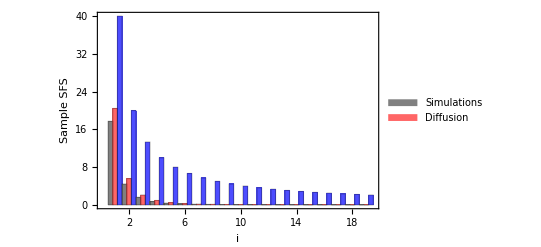

```mathematica
n=20;
N1= 1000;


mu=10^-7;
L=99999;
theta=4N1 mu L;

fun01=Interpolation[Data1s]
fun02=Interpolation[datadiffusion]
list01=Table[(n!)/((n-i)! i!)  NIntegrate[x^i (1-x)^(n-i) fun01[x],{x,0,1}, MaxRecursion->30],{i,1,n-1,1}];
list02=Table[(n!)/((n-i)! i!)  NIntegrate[x^i (1-x)^(n-i) fun02[x],{x,0,1}, MaxRecursion->30],{i,1,n-1,1}];
list03=Table[(n!)/((n-i)! i!)  NIntegrate[x^i (1-x)^(n-i) theta/x,{x,0,1}, MaxRecursion->30],{i,1,n-1,1}];

list6=Table[i,{i,1,n-1,1}];
BarChart[Transpose@{list01,list02, list03},ChartStyle->{ Gray,Lighter[Red,0.4], Lighter[Blue,0.3], Magenta},ChartLabels->{{"","2","","4","","6","","8","","10","","12","","14","","16","","18","", "20","21","22","23","24","25","26","27","28","29","30","31","32","33","34","35","36","37","38","39"},None},Frame->True, FrameLabel->{"i","Sample SFS"},FrameStyle->Thickness[.003],LabelStyle->Directive[Black,Bold,Medium,FontSize->14],BaseStyle->{FontWeight->"Bold",FontSize->14,FontFamily->"Calibri"},ChartLegends-> {"Simulations","Diffusion"}](*{Placed[{"c=0.001"},{0.1,0.7}], Placed[{"c=0.01"},{0.5,0.7}] , Placed[{"c=0.1"},{0.5,0.4}] }]*)
```

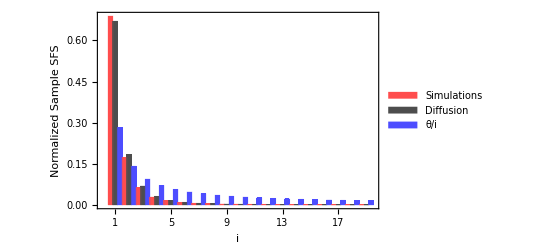

```mathematica
normalizeList[lst_]:=lst/Total[lst]

list01Normalized=normalizeList[list01];
list02Normalized=normalizeList[list02];
list03Normalized=normalizeList[list03];

BarChart[Transpose[{list01Normalized,list02Normalized,list03Normalized}],ChartStyle->{ Lighter[Red,0.3],Lighter[Black,0.3], Lighter[Blue,0.3], Magenta},ChartLabels->{list6,None},Frame->True,FrameLabel->{"i","Normalized Sample SFS"},FrameStyle->Thickness[.003],LabelStyle->Directive[Black,Bold,FontSize->10],BaseStyle->{FontWeight->"Bold",FontSize->8,FontFamily->"Calibri"},ChartLegends->{"Simulations","Diffusion","θ/i"}]
```

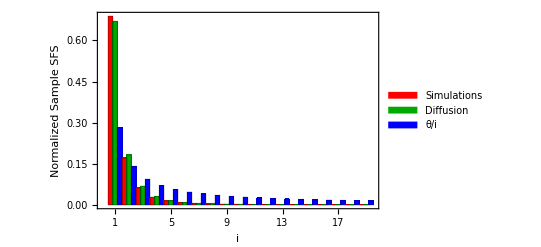

```mathematica
normalizeList[lst_]:=lst/Total[lst]

list01Normalized=normalizeList[list01];
list02Normalized=normalizeList[list02];
list03Normalized=normalizeList[list03];

BarChart[Transpose[{list01Normalized,list02Normalized,list03Normalized}],ChartStyle->{ Red,Darker[Green], Blue},ChartLabels->{list6,None},Frame->True,FrameLabel->{"i","Normalized Sample SFS"},FrameStyle->Thickness[.003],LabelStyle->Directive[Black,Bold,FontSize->12](*,BaseStyle->{FontWeight->"Bold",FontSize->8,FontFamily->"Calibri"}*),ChartLegends->{"Simulations","Diffusion","θ/i"}]
```

```mathematica
p0 Abs[Log[1-pt]]
```

0.0285959

```mathematica
a1=-Graphics-;
```

```mathematica
Style[θ,FontSize->14]
```

θ

```mathematica
θ/x
```

θ/x

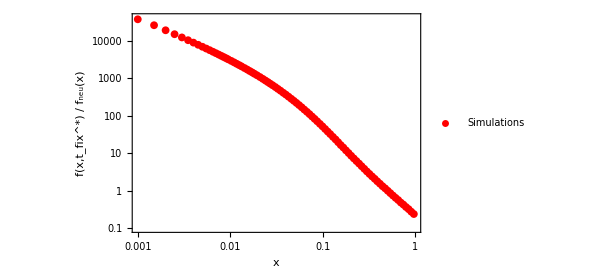
```mathematica
l1=-Graphics-;
```

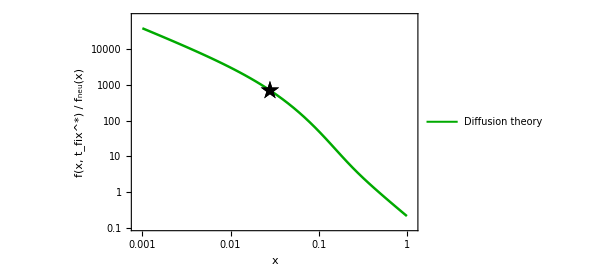
```mathematica
l2=-Graphics-;
```

```mathematica
Show[l1,l2]
```

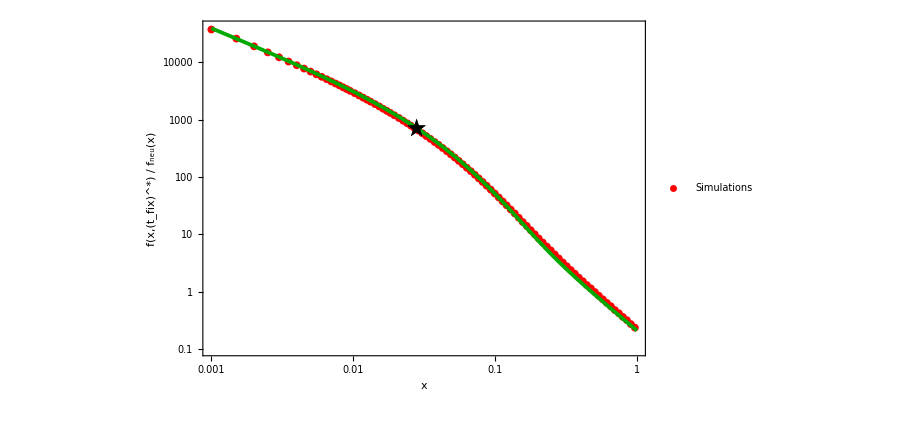

```mathematica
Show[l1,l2]
```

```mathematica
f1=-Graphics-;
```

```mathematica
a1scombined is below for various ns vala section
```

```mathematica
Show[a1sCombined,f1]
```

```mathematica
Show[a1,a2]
```

```mathematica
130 + 380
```

510

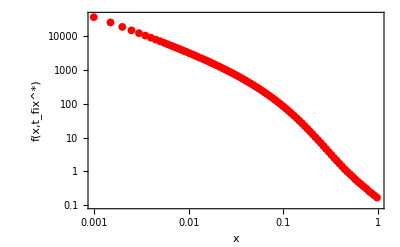
```mathematica
a1sCombined=-Graphics-;
```

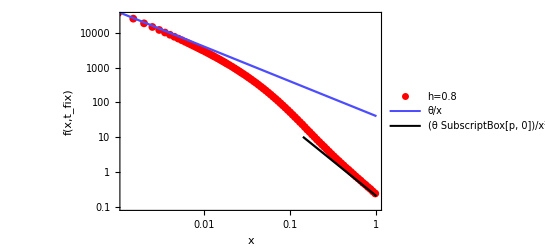

## Figure 2 with various NS final figure and help from inbreeding figure paper file

```mathematica
Quit[]
```

### SImulations Ns = 50

InputStream[…]

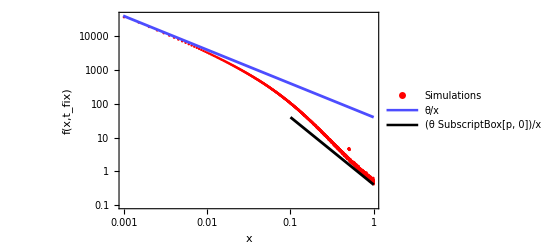

```mathematica
N1=1000;
mu=10^-7;
L=100000;
h=0.5;

sa=(h + (1-h) f);

theta=4 N1 mu L; (* theta= 2 N mu *)
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/hard_sweep/post_fix_Ns_50.txt"]
datas1s=ReadList[s1s,{Number,Number}];

Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];


Data1s=Transpose@{x11s,x21s};

a1s=ListLogLogPlot[{Data1s}, Frame->True, FrameLabel->{"x","f(x,t_fix)"},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red,Magenta,Brown},PlotLegends->{"Simulations", "Diffusion"},PlotRange->{{ 0.001,1},{0.1,40000}}];


a2s=LogLogPlot[theta/(x),{x,0,1},PlotStyle->{Lighter[Blue,0.3],Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\), \(x\)]\)",Medium]}];

a3s=LogLogPlot[theta /(2 1000 2 0.5 0.05 x^2),{x,0.1,1},PlotStyle->{Black,Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\\\ 
   \*SubscriptBox[\(p\), \(0\)]\), SuperscriptBox[\(x\), \(2\)]]\)",Medium]}];

Show[a1s,a2s,a3s]
```

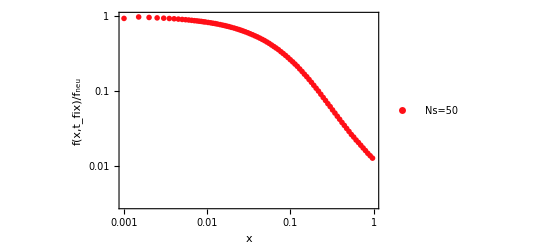

```mathematica
Data1s=Transpose@{x11s,x11s x21s/theta};
(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.001;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{RGBColor[1.,0.06,0.09]},PlotLegends->{"Ns=50"},PlotRange->{{0.001,1},{0.003,1}},PlotMarkers->{"⌚",10}];

(*Show both plots*)
Show[a1sCombined]
```

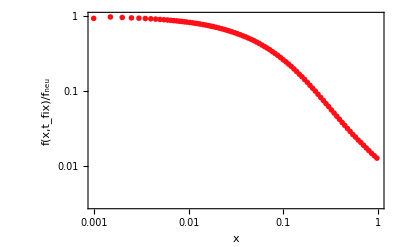
```mathematica
s50=-Graphics-;
```

### Simulations Ns = 100 has star marked

```mathematica
Quit[]
```

InputStream[…]

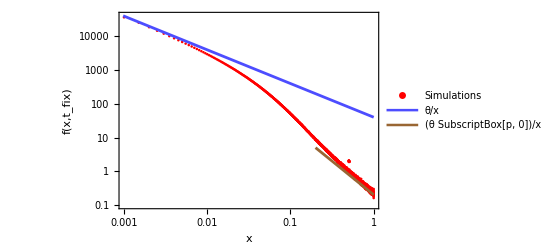

```mathematica
N1=1000;
mu=10^-7;
L=100000;
h=0.5;
sa=(h + (1-h) f);

theta=4 N1 mu L; (* theta= 2 N mu *)
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/hard_sweep/average_data_sweep_Ns_100.txt"]
datas1s=ReadList[s1s,{Number,Number}];

Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];


Data1s=Transpose@{x11s,x21s};

a1s=ListLogLogPlot[{Data1s}, Frame->True, FrameLabel->{"x","f(x,t_fix)"},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red,Magenta,Brown},PlotLegends->{"Simulations", "Diffusion"},PlotRange->{{ 0.001,1},{0.1,40000}}];


a2s=LogLogPlot[theta/(x),{x,0,1},PlotStyle->{Lighter[Blue,0.3],Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\), \(x\)]\)",Medium]}];

a3s=LogLogPlot[theta /(2 1000 2 0.5 0.1 x^2),{x,0.2,1},PlotStyle->{Brown,Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\\\ 
   \*SubscriptBox[\(p\), \(0\)]\), SuperscriptBox[\(x\), \(2\)]]\)",Medium]}];

Show[a1s,a2s,a3s]
```

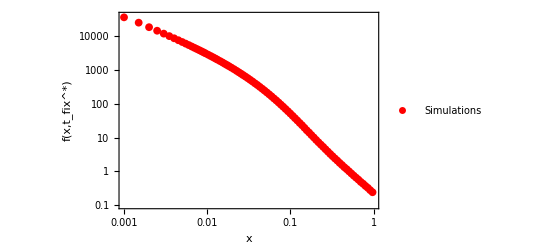

```mathematica
Data1s=Transpose@{x11s,x21s};
(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.001;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

(*a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,(t^*)_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium,FontSize->16],PlotStyle->{
Red},PlotLegends->{"Simulations"},PlotRange->{{ 0.001,1},{0.1,40000}},PlotMarkers->{"●",8}];*)
a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{Style["x",Italic],Style[Row[{Style["f(",Italic],Style["x",Italic],Style[",",Italic],SubsuperscriptBox[Style["t",Italic],Style["fix",Italic],"*"]//DisplayForm,Style[")  ",Italic](*,SubscriptBox[Style["f",Italic],"neu"]//DisplayForm,Style["(x)",Italic]*)}]]},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium,FontSize->16],PlotStyle->{Red},PlotLegends->{"Simulations"},PlotRange->{{0.001,1},{0.1,40000}},PlotMarkers->{"●",8}];





(*Show both plots*)
Show[a1sCombined]
```

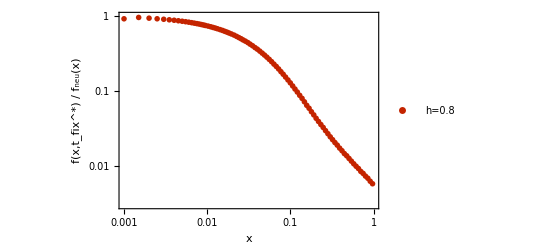

```mathematica
Data1s=Transpose@{x11s,x11s x21s/theta};
(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.001;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium,FontSize->16],PlotStyle->{
RGBColor[0.77,0.14,0.]},PlotLegends->{"h=0.8"},PlotRange->{{0.001,1},{0.003,1}},PlotMarkers->{"\[MathematicaIcon]",8}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{Style["x",Italic],Style[Row[{Style["f(",Italic],Style["x",Italic],Style[",",Italic],SubsuperscriptBox[Style["t",Italic],Style["fix",Italic],"*"]//DisplayForm,Style[") / ",Italic],SubscriptBox[Style["f",Italic],"neu"]//DisplayForm,Style["(x)",Italic]}]]},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium,FontSize->16],PlotStyle->{
RGBColor[0.77,0.14,0.]},PlotLegends->{"h=0.8"},PlotRange->{{0.001,1},{0.003,1}},PlotMarkers->{"\[MathematicaIcon]",8}];


(*Show both plots*)
Show[a1sCombined]
```

```mathematica
RGBColor[0.77,0.14,0.]
```

```mathematica
RGBColor[0.91, 0.14, 0.]
```

```mathematica
RGBColor[1.,0.06,0.09]
```

```mathematica
RGBColor[1., 0.06, 0.3]
```

```mathematica
RGBColor[1,0.41,0.52]
```

RGBColor[1, 0.41, 0.52]

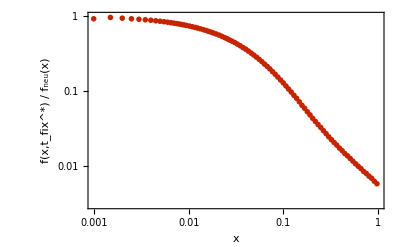
```mathematica
s100=-Graphics-;
```

### Simulations Ns = 10 and has the main figure NS

```mathematica
Quit[]
```

```mathematica
N1=1000;
mu=10^-7;
L=99999;
theta=4 N1 mu L; (* theta= 2 N mu *)
s1s=OpenRead["/Users/user/Desktop/Slim_programs/Sel_sfs_independent/Sweeps_project/N_1000_s_0.01_h_0.5/dist_txt_files/Ns_10_sfs.txt"];
(*e1:1 t:5000000 and theta is 0.100000 *)
datas1s=ReadList[s1s,{Number,Number}];

Close[s1s];

x11s=datas1s[[All,1]];
x21s=datas1s[[All,2]];


Data1s=Transpose@{x11s, x21s};

a1s=ListLogLogPlot[{Data1s}, Frame->True, FrameLabel->{"x","f(x,t_fix)"},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"Diffusion"}];
(*a2s=LogLogPlot[{theta/x, theta/(x^2 2 N1 0.01 0.5)},{x,0,1},Frame->True, FrameLabel->{"x","distribution"},FrameStyle->Thickness[.003], FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"θ/x","(θ SubscriptBox[p, 0])/x^2"}]; *)
a2s=LogLogPlot[theta/x,{x,0,1},PlotStyle->{Lighter[Blue,0.3],Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\), \(x\)]\)",Large]}];

a3s=LogLogPlot[theta/(20 x^2),{x,0.1,1},PlotStyle->{Black,Thickness[0.005]},PlotLegends->{Style["\!\(\*FractionBox[\(θ\\\ 
   \*SubscriptBox[\(p\), \(0\)]\), SuperscriptBox[\(x\), \(2\)]]\)",Large]}];

Show[a1s,a2s,a3s]
```

-Graphics-

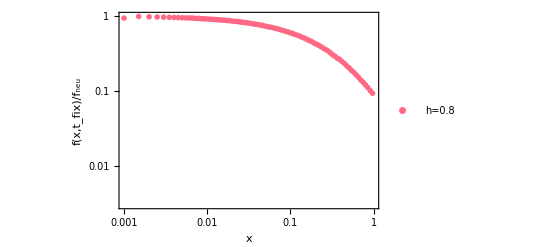

```mathematica
Data1s=Transpose@{x11s,x11s x21s/theta};
(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.001;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];

(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","Distribution of SFS"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];

a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_fix)/f_neu"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{RGBColor[1,0.41,0.52] },PlotLegends->{"h=0.8"},PlotRange->{{0.001,1},{0.003,1}},PlotMarkers->{"♣",8}];

(*Show both plots*)
Show[a1sCombined]
```

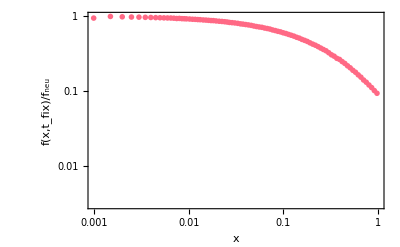
```mathematica
s10=-Graphics-;
```

```mathematica
Text[Style["Ns=10",FontSize->14,FontSlant->"Italic",RGBColor[1,0.41,0.52]]]
```

Ns=10

```mathematica
Show[a1sCombined,s50,s10]
```

```mathematica
Show[s100,s50,s10]
```

```mathematica
sim=-Graphics-;
```

```mathematica
Show[a1sCombined,sim,d10, d100,d50]
```

-Graphics-

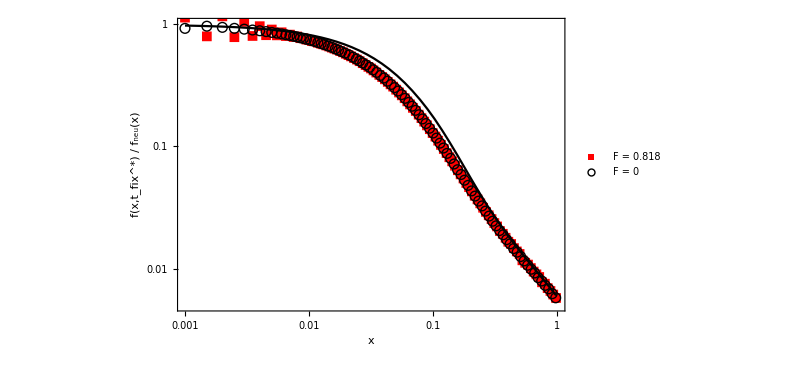

-Graphics-

```mathematica
a1=-Graphics-;
```

```mathematica
below mean t
```

```mathematica
Show[a1,d50,d100,d10]
```

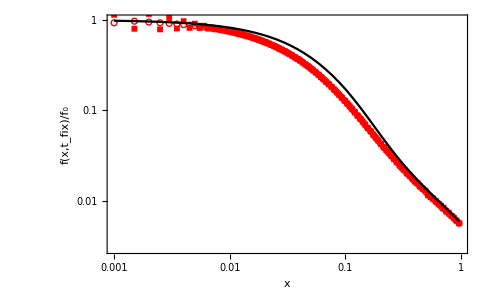

```mathematica
RGBColor[1,0.5,0.5]
RGBColor[0.8,0,0]
RGBColor[0.86,0.08,0.24]
RGBColor[0.7,0.13,0.13]
RGBColor[0.8,0.36,0.36]
```

RGBColor[1, 0.5, 0.5]

RGBColor[0.8, 0, 0]

RGBColor[0.86, 0.08, 0.24]

RGBColor[0.7, 0.13, 0.13]

RGBColor[0.8, 0.36, 0.36]

## Diffusion

```mathematica
d10=-Graphics-;
```

```mathematica
d10=-Graphics-; (*this is new*)
```

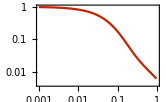
```mathematica
d100=-Graphics-;
```

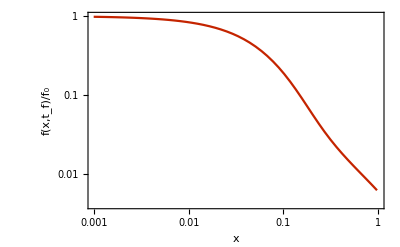
```mathematica
d100=-Graphics-; (* this is mean tfix *)
```

```mathematica
d50=-Graphics-;
```

```mathematica
d50=-Graphics-;(* this is mean tfix *)
```

```mathematica
Data1s=Transpose@{xaxis,xaxis averageGData1/theta};
(*Define logarithmic binning and smoothing function*)
smoothDataLog[data_,numBins_,xThreshold_]:=Module[{filteredData,bins,binnedData,binEdges,binnedX,binnedY,counts,logMin,logMax,logBinEdges},(*Filter data to include only points where x>xThreshold*)filteredData=Select[data,#[[1]]>xThreshold&];
(*Determine the range and width of bins for filtered data*)logMin=Log10[Min[filteredData[[All,1]]]];
logMax=Log10[Max[filteredData[[All,1]]]];
logBinEdges=Range[logMin,logMax,(logMax-logMin)/numBins];
bins=10^logBinEdges;
(*Initialize bins*)binnedX=Table[0,{numBins}];
binnedY=Table[0,{numBins}];
counts=Table[0,{numBins}];
(*Bin the data*)Do[Module[{binIndex},binIndex=Floor[(Log10[filteredData[[i,1]]]-logMin)/((logMax-logMin)/numBins)]+1;
If[binIndex>0&&binIndex<=numBins,binnedX[[binIndex]]+=filteredData[[i,1]];
binnedY[[binIndex]]+=filteredData[[i,2]];
counts[[binIndex]]+=1;]],{i,Length[filteredData]}];
(*Calculate mean values for each bin*)binnedData=Table[If[counts[[i]]>0,{binnedX[[i]]/counts[[i]],binnedY[[i]]/counts[[i]]},Nothing],{i,numBins}];
(*Return the smoothed data*)binnedData];

(*Apply the smoothing function to your data*)
numBins=100;(*Adjust the number of bins as needed*)xThreshold=0.001;(*Threshold for binning*)smoothedData=smoothDataLog[Data1s,numBins,xThreshold];

(*Separate data into two parts:original part (x<=0.5) and smoothed part (x>0.5)*)
originalPart=Select[Data1s,#[[1]]<=xThreshold&];
smoothedPart=Select[smoothedData,#[[1]]>xThreshold&];

(*Combine original and smoothed parts*)
combinedData=Join[originalPart,smoothedPart];
interpolation=Interpolation[combinedData];
(*Plot the original and combined data*)
a1sOriginal=ListLogLogPlot[{Data1s},Frame->True,FrameLabel->{"x","f/f^*"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue},PlotLegends->{"Original Data"},PlotRange->{{0.001,1},{0.01,10000}}];
a1sInterpolated=LogLogPlot[interpolation[x],{x,Min[combinedData[[All,1]]],Max[combinedData[[All,1]]]},PlotStyle->{RGBColor[0.77,0.14,0.]},Frame->True,FrameLabel->{"x","f(x,t_f)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotRange->{{0.001,1},{0.004,1}}];
a1sCombined=ListLogLogPlot[{combinedData},Frame->True,FrameLabel->{"x","f(x,t_f)/f_0"},FrameStyle->Thickness[.003],FrameTicks->Automatic,LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Red},PlotLegends->{"h=0.8"},PlotRange->{{0.001,1},{0.003,1}}(*, PlotMarkers->{"○",10}*), Joined->True];

(*Show both plots*)
Show[a1sInterpolated]
```

```mathematica
a1=-Graphics-;
```

```mathematica
a2=-Graphics-;
```

```mathematica
Show[a1,a2]
```

-Graphics-

```mathematica
Text[Style["Ns=100",FontSize->14,FontSlant->"Italic",RGBColor[0.77,0.14,0.]]]
```

Ns=100